```mathematica
<<HPL`
```

```mathematica
<<HypExp`
```

```mathematica
assmp1={km>0,kp>0,x>0,y>0,kperp>0,Q>0,τ>0,γe>0,1>δ>0,1>θ1>0,Subscript[Ω, 1-2ϵ]>0};
allangle=Subscript[Ω, d_]:>(2 π^(d/2))/Gamma[d/2];
```

#### Plus-dist (subtract divergence at x= 0)

```mathematica
(* ∫_0^1 ⅆx f(x)1/x^(1-λ) = ∫_0^1 ⅆx 1/x^(1-λ) (f(x)-f(0)+f(0))= f(0)∫_0^1 ⅆx/x^(1-λ) + ∫_0^1 ⅆx x^λ/x^1 (f(x)-f(0)) = f(0)∫_0^1 ⅆx/x^(1-λ) + ∫_0^1 ⅆx (∑_n λ^n/(n!)log^n(x))/x (f(x)-f(0))
            = f(0)∫_0^1 ⅆx/x^(1-λ) + ∫_0^1 ⅆx f(x)∑_n λ^n/(n!)Plusdist(n,x) *)

(*Plusdist(n,x) := δ_+^(n)(x) *)

(*x^(-1+a)log(x) = -1/a^2δ(x)+∑_(n=0)^5 a^n/(n!)δ_+^(n+1)(x),   x^(-1+a) = 1/a δ(x)+∑_(n=0)^5 a^n/(n!)δ_+^(n)(x)*)

(* f(x) δ_+^(n)(x) = (log^n(x))/x(f(x)-f(0)) *)

distExpl[x_]:={Log[x] x^(-1+a_)->-1/a^2 diracDelta[x]+Sum[a^n/(n!)PlusDist[n+1,x],{n,0,4}],x^(-1+a_)->1/a diracDelta[x]+Sum[a^n/(n!)PlusDist[n,x],{n,0,4}]};
distRules={a_ diracDelta[b_]:>(a/.b->0),a_ diracDelta'[b_]:>(-D[a,b]/.b->0),a_ PlusDist[n_,b_]:>Log[b]^n/b(a-(a/.b->0))};
DistApply[ex_,z_]:=Collect[ex,{diracDelta[z],diracDelta'[z],PlusDist[_,z]}]/.distRules
distRules2={a_ diracDelta[b_]:>(a/.b->0)diracDelta[b]};
DistApply2[ex_,z_]:=Collect[ex,{diracDelta[z],diracDelta'[z],PlusDist[_,z]}]/.distRules2
CollectColor[ex_]:=Collect[(ex//Expand)/.CF^2->CF2/.CF CA->CFCA/.CF nf TF->CFnfTF,{as,ios,CF,CA,CFCA,CF2,CFnfTF,Lβ,Lδ,Lτ,LQ,Lτδ,LQδ},Expand[Simplify[#]]&]/.CF2->CF^2/.CFCA->CF CA/.CFnfTF->CF nf TF/.Log[a_?NumberQ]:>Log[2](Log[a]/Log[2]//FullSimplify);
distRules3={a_ diracDelta[b_]:>(Normal@Series[a,{b,0,0},Assumptions->b>0]),a_ diracDelta'[b_]:>(-Normal@Series[D[a,b],{b,0,0},Assumptions->b>0]),a_ PlusDist[n_,b_]:>Log[b]^n/b(a-(Normal@Series[a,{b,0,0},Assumptions->b>0]))};
DistApply3[ex_,z_]:=Collect[ex,{diracDelta[z],diracDelta'[z],PlusDist[_,z]}]/.distRules3
```

## 1&2-loop-test

#### 1-loop coft

```mathematica
(*int = (nbar.n1)/(k_- n1.k)=(n1_-)/(k_-((n_+k_-)/2+(n_-k_+)/2+ n_⊥.p_⊥))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ |n_⊥||p_⊥|Cos[θ]))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ δ θ1|k_⊥|Cos[θ]))*)
(*mesuare = 1/2 dk_+dk_-d^(2-2ϵ)k_⊥ δ^+(k^2) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/2|k_⊥|^(1-2ϵ)Subscript[dΩ, 2-2ϵ] dk_+dk_-d|k_⊥| δ^+(|k_⊥|^2-k_+k_-) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/4|k_⊥|^(-2ϵ) 2π Sin^(-2ϵ)[θ] dk_+dk_-δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) |_(|k_⊥|=√(k_+k_-))  *)
(*prefac = 1/(2π)^(3-2ϵ)*)
```

```mathematica
intgrand=2CF*1/4*1/(2π)^(3-2ϵ)*1/km*(2*Sin[θ]^(-2ϵ)*Subscript[Ω, 1-2ϵ])/(δ^2 θ1^2*km+kp-2 θ1 δ kperp Cos[θ])*E^(-km/(Q τ ))*kperp^(-2ϵ)/.kperp->√(km kp);
prefac=CF*(E^EulerGamma/(4π))^ϵ*(4π)^(-2+2 ϵ) Q^(-2 ϵ) δ^(-2 ϵ)  (1/τ)^(2 ϵ) ;

oldvar={kp,km};
newvar={x,y};
old2new={kp->Q δ^2 x/y,km-> Q  x};
jaco = Det@(D[oldvar/.old2new,#]&/@newvar);
constrant = HeavisideTheta[kp/km - δ^2];
InTconstrant=Simplify[#,Assumptions->assmp1]&@(constrant/.old2new/.HeavisideTheta[x_]:>x>0//Reduce)
```

```mathematica
(*Integrate x & Cos[θ]*)
```

```mathematica
Integrate[intgrand*jaco/.old2new//Simplify//PowerExpand,{x,0,∞},GenerateConditions->False]
```

```mathematica
loop1result=Integrate[%,{θ,0,π},Assumptions->{0<y<1,0<θ1<1},GenerateConditions->False]/.allangle
```

```mathematica
(*y need to be int..., we just need ϵ-divergence term !*)
```

```mathematica
(*1st, expand 2F1*)
```

```mathematica
Simplify[#(*/.{Log[x_]:>Log[x//Together],PolyLog[n_,x_]:>PolyLog[n,x//Together]}*),Assumptions->{0<y<1,0<θ1<1}]&@((loop1result//FunctionExpand)/.Hypergeometric2F1[a_,b_,c_,d_]:>HypExp[ Hypergeometric2F1[a,b,c,d],ϵ,4]//Expand)
```

```mathematica
(*2nd, use puls-dist*)
```

```mathematica
loop1ResultWithϵ=(Series[(DistApply[#,y]&@((%/prefac//Expand)/.distExpl[y])),{ϵ,0,4}]//Expand//Normal)/.ϵ^a_:>0/;a>=4
```

```mathematica
(*ϵ^-2*)
Coefficient[  loop1ResultWithϵ//Expand,ϵ,-2]//. a_*Log[x_]+a_*Log[y_]:>a Log[x y//Expand]//Simplify;
Integrate[#,{y,0,1},Assumptions->0<θ1<1]&@%
```

```mathematica
(*ϵ^-1*)
Coefficient[  loop1ResultWithϵ//Expand,ϵ,-1]//. a_*Log[x_]+a_*Log[y_]:>a Log[x y//Expand]//Simplify;
Integrate[#,{y,0,1},Assumptions->0<θ1<1]&@%
```

```mathematica
(*ϵ^0*)
```

```mathematica
Coefficient[ ϵ loop1ResultWithϵ//Expand,ϵ,1]//. a_*Log[x_]+a_*Log[y_]:>a Log[x y//Expand]//Simplify;
Integrate[#,{y,0,1},Assumptions->0<θ1<1]&@%
```

```mathematica
(*ϵ^1*)
Coefficient[  loop1ResultWithϵ//Expand,ϵ,1]//. a_*Log[x_]+a_*Log[y_]:>a Log[x y//Expand]//Simplify
(*Integrate[#,{y,0,1},Assumptions->0<θ1<1]&@%*)
```

```mathematica
NIntegrate[%/.θ1->0,{y,0,1}]
```

```mathematica
-14/3 Zeta[3]//N
```

```mathematica
(*ϵ^2*)
Coefficient[  loop1ResultWithϵ//Expand,ϵ,2]//. a_*Log[x_]+a_*Log[y_]:>a Log[x y//Expand]//Simplify
```

```mathematica
NIntegrate[%/.θ1->0,{y,0,1}]
```

```mathematica
%/π^4//Rationalize
```

```mathematica
Series[E^(-2ϵ Log[τ/μ])*(-2/ϵ^2+2 Log[1-θ1^2]*1/ϵ-π^2/2-2 Log[1-θ1^2]^2-2 PolyLog[2,θ1^2]),{ϵ,0,1}]//Normal
```

#### 2-loop coft (opposite)

```mathematica
r[l1_,l2_]:=l2/l1;
FIT[r_]:=Log[1+r]Log[1+1/r]-4/(1+r)Log[1+r]-ϵ*(π^2/3-3PolyLog[3,-r]-4/(1+r)Log[r]+((4r)/(1+r)+2Log[r])PolyLog[2,-r]+(1/2(Log[r])^2-2*(1-r)/(1+r)Log[r]-4-π^2/6)Log[1+r]);
FGH[r_]:=-2/(3(1+r)^3)*(-2r+(5+9r+6 r^2)Log[1+r])-(2ϵ)/(3(1+r)^3)(16/3 r+(5 π^2)/12(1+r)^3-(31/3+23r+8 r^2)Log[1+r]-1/2(5+3r-3r^2-5r^3)(Log[1+r])^2+(6r+9r^2+5r^3)PolyLog[2,-r]);
FQ[r_]:=4/(3(1+r)^3)(-2r+(1+r)^3 Log[1+r]+Log[r])+(8ϵ)/(3(1+r)^3)(5/3 r+π^2/24(1+r)^3-1/8(1+r)^3(Log[r])^2-(8/3+7r+r^2)Log[1+r]+1/2(r^3-1)((Log[1+r])^2+PolyLog[2,-r]));

Sopp[l1_,l2_]:=(Subscript[α, s]/(2π))^2((E^EulerGamma μ^2)^(2ϵ))/(Gamma[1-ϵ])^2(l1 l2)^(-1-2ϵ)*(CF^2 4/ϵ^2+CF CA((2 π^2)/3+4Zeta[3] ϵ+14/45 π^2 ϵ^2+FIT[r[l1,l2]]+FIT[1/r[l1,l2]]+FGH[r[l1,l2]]+FGH[1/r[l1,l2]])+CF TR nf (FQ[r[l1,l2]]+FQ[1/r[l1,l2]]));
```

```mathematica
SoppCF2=Coefficient[Sopp[ωL,ωR]//Expand,CF^2]
```

```mathematica
Integrate[SoppCF2/.{ωL->ωL/δ,ωR->ωR δ},{ωR,1,∞},Assumptions->{ωL>0,1>δ>0}]
```

```mathematica
DistApply[(SoppCF2/.{ωL->ωL/δ,ωR->ωR δ}//PowerExpand)/.distExpl[ωR],ωR]
```

#### 2-loop coft (all)

CF^2 non-abelian exp theorem

```mathematica
CFloop1=CF/(4π)α0 E^(-2ϵ L)(-2/ϵ^2-π^2/2-14/3 Zeta[3]ϵ-(7 π^4)/48 ϵ^2);
CFloop2=1/(2!)CFloop1^2;
V2F=(CFloop2/(CF/(4π)α0 E^(-2ϵ L))^2//Expand)/.ϵ^a_:>0/;a>=1
```

CF CA & CF TF nf

```mathematica
β0=11/3 CA-4/3 TF nf;
SfCA0[r_]:=8((r(11r^2+21r+12)Log[r])/(3(r+1)^3)+(π^2(r+1)^2+2r)/(3(r+1)^2)+(Log[r+1])^2-Log[r]Log[r+1]-11/3 Log[r+1]);
SfCA1[r_]:=(8(-11r^3-9r^2+9r+11)PolyLog[2,-r])/(3(r+1)^3)+24PolyLog[3,-r]-16PolyLog[2,-r]Log[r]+(4r(11r^2+21r+12)(Log[r])^2)/(3(r+1)^3)-(8r(67r^2+141r+60)Log[r])/(9(r+1)^3)-(4(r^3(11π^2-36Zeta[3])+r^2(-108Zeta[3]+32+21π^2)+4r(-27Zeta[3]+8+3π^2)-36Zeta[3]))/(9(r+1)^3)+(8(-11r^3-9r^2+9r+11)Log[r+1]Log[r])/(3(r+1)^3)-4Log[r+1](Log[r])^2+4/9(134+3π^2)Log[r+1];
SfCA2[r_]:=(8(67r^3+81r^2-81r-67)PolyLog[2,-r])/(9(r+1)^3)-(8(55r^3+117r^2+81r+11)PolyLog[3,-r])/(3(r+1)^3)-(32(11r^3+9r^2-9r-11)PolyLog[3,1/(r+1)])/(3(r+1)^3)-(16(11r^3+9r^2-9r-11))/(3(r+1)^3)PolyLog[2,-r]Log[r+1]+(8(33r^3+75r^2+57r+11))/(3(r+1)^3)PolyLog[2,-r]Log[r]-16PolyLog[4,1/(r+1)]-16PolyLog[4,r/(r+1)]-8PolyLog[2,-r](Log[r])^2+16PolyLog[2,-r]Log[r]Log[r+1]+8PolyLog[3,-r]Log[r]+16PolyLog[3,1/(r+1)]Log[r]+(4(-40(4r^2(27Zeta[3]-2)+r(189Zeta[3]-8)+99Zeta[3])+5 π^2 r(67r^2+147r+66)+33π^4(r+1)^3))/(135(r+1)^3)-(32(12r^2+21r+11))/(9(r+1)^3)(Log[r+1])^3+(4r(11r^2+21r+12)(Log[r])^3)/(9(r+1)^3)-4/3(Log[r])^3Log[r+1]+(16(12r^2+21r+11)Log[r](Log[r+1])^2)/(3(r+1)^3)-(4r(67r^2+141r+60)(Log[r])^2)/(9(r+1)^3)+(16r(193r^2+384r+177)Log[r])/(27(r+1)^3)+(4(-11r^3-9r^2+9r+11)(Log[r])^2Log[r+1])/(3(r+1)^3)-(8(π^2(66r^3+90r^2+9r-33)+2(193r^3+561r^2+561r+193))Log[r+1])/(27(r+1)^3)+(8(67r^3+69r^2-93r+3π^2(r+1)^3-67)Log[r]Log[r+1])/(9(r+1)^3)-4/3(Log[r+1])^4+8(Log[r]Log[r+1])^2+16Zeta[3]Log[r+1]-16Zeta[3]Log[r]+(32r (Log[r+1])^2)/(3(r+1)^2);
Sfnf0[r_]:=(-16(2r(r+1)-2(r+1)^3Log[r+1]+r(2r^2+3r+3)Log[r]))/(3(r+1)^3);
Sfnf1[r_]:=8/(9(r+1)^3)(-12(r^3-1)PolyLog[2,-1/r]-32r^3Log[r+1]+3π^2r^2+20r^2-96r^2Log[r+1]-3(4r^3+3r^2+3r-2)(Log[r])^2+4Log[r](3(r^3-1)Log[r+1]+r(8r^2+21r+3))+3π^2r+20r-96r Log[r+1]-32Log[r+1]+2π^2);




SfCA[r_,ϵ_]:=SfCA0[r]+ϵ SfCA1[r]+ϵ^2 SfCA2[r];
Sfnf[r_,ϵ_]:=Sfnf0[r]+ϵ Sfnf1[r];





SgCA[ϵ_]:=4/ϵ^3+22/(3 ϵ^2)+1/ϵ(134/9-(4 π^2)/3)-(116Zeta[3])/3+(11 π^2)/9+772/27+ϵ((484Zeta[3])/9+4784/81+(67 π^2)/27-(137 π^4)/90);
vCA[ϵ_]:=-4/ϵ^3+(2 π^2)/ϵ+(32Zeta[3])/3-ϵ π^4/30;
Sgnf[ϵ_]:=-8/(3 ϵ^2)-40/(9ϵ)-152/27-(4 π^2)/9+ϵ(-952/81-(20 π^2)/27-176/9 Zeta[3]);



Sf[r_,ϵ_]:=CF CA SfCA[r,ϵ]+CF TF nf Sfnf[r,ϵ]
Sh[ϵ_]:=CF CA SgCA[ϵ]+CF CA vCA[ϵ]+CF TF nf Sgnf[ϵ]
```

```mathematica
S1sym[kl_,kr_]:=(α/(4π))^2 μ^(4ϵ)(1/(kr kl)^(1+2ϵ)Sf[kl/kr,ϵ])
S1r[kl_,kr_]:=(α/(4π))^2 μ^(4ϵ)(1/kl^(1+4ϵ)DiracDelta[kr]Sh[ϵ])
S1l[kr_,kr_]:=(α/(4π))^2 μ^(4ϵ)(1/kr^(1+4ϵ)DiracDelta[kl]Sh[ϵ])
S2r[kl_,kr_]:=-4CF β0 μ^(2ϵ)(α/(4π))^2 (1/kl^(1+2ϵ)DiracDelta[kr])*E^(EulerGamma ϵ)/(ϵ^2 Gamma[1-ϵ])
S2l[kl_,kr_]:=-4CF β0 μ^(2ϵ)(α/(4π))^2 (1/kr^(1+2ϵ)DiracDelta[kl])*E^(EulerGamma ϵ)/(ϵ^2 Gamma[1-ϵ])
S[kl_,kr_]:=S1sym[kr,kl]+S1r[kr,kl]+S1l[kr,kl]+S2r[kr,kl]+S2l[kr,kl]
```

```mathematica
S2l[ωl,ωr]
```

```mathematica
S2r[ωl,ωr]
```

```mathematica
(*S2l is scaleless!*)
S2lint=0;
```

```mathematica
Integrate[S2r[ωl,ωr],{ωr,a,∞},Assumptions->a<0];
S2rint=Integrate[%,{ωl,0,Q δ β},GenerateConditions->False]
```

```mathematica
S1r[ωl,ωr]
```

```mathematica
S1l[ωl,ωr]
```

```mathematica
Integrate[S1r[ωl,ωr],{ωr,a,∞},Assumptions->a<0];
S1rint=Integrate[%,{ωl,0,Q δ β},GenerateConditions->False]
```

```mathematica
(*S1l is scaleless!*)
S1lint=0
```

```mathematica
Solve[{ωl ωr==p,ωl/ωr==r},{ωl,ωr},Assumptions->{p>0,r>0}]
```

```mathematica
jaco=Simplify[Det@(D[{ωl,ωr}/.{ωl-> √(r p),ωr->√(p/r)},#]&/@{r,p}),Assumptions->{p>0,r>0}]
```

```mathematica
Simplify[S1sym[ωl,ωr]*jaco/.{ωl->p √(r/p),ωr->√(p/r)},Assumptions->{p>0,r>0}]//Expand
```

```mathematica
Reduce[{0<p √(r/p)<X,0<√(p/r)},{r,p}]
```

```mathematica
Y>0&&X>0&&((0<r≤X/Y&&0<p<r Y^2)||(r>X/Y&&0<p<X^2/r))/.{X->1,Y->999}
```

```mathematica
ωr->√(p/r)
```

```mathematica
r->{∞,0}
```

```mathematica
p √(r/p)->√(r p)
```

```mathematica
0<r p<Q^2
```

```mathematica
0<p/r<∞
```

```mathematica
jaco
```

```mathematica
?S1sym
```

```mathematica
jaco
```

```mathematica
pre=(α/(4 π))^2 μ^(4 ϵ) X^(-4ϵ)
```

```mathematica
intsymCA=((Simplify[#/(p)^(1+2 ϵ)*jaco//.{ωl ωr->p,ωl/ωr->r},Assumptions->{p>0,r>0}]//Expand)//Simplify)&/@{SfCA0[r],ϵ SfCA1[r],ϵ^2 SfCA2[r],Sfnf0[r], ϵ Sfnf1[r]};
```

```mathematica
intsymCAres=Integrate[%,{p,0,X^2/r}]//Normal;
```

```mathematica
(intsymCAres//PowerExpand)/.distExpl[r]//Expand;
```

```mathematica
intsymCAresϵ=Collect[%,ϵ]/.ϵ^a_:>0/;a>=2;
```

```mathematica
symCAϵm2=DistApply3[#,r]&/@Coefficient[( intsymCAres//PowerExpand)/.distExpl[r],ϵ^-2]
```

```mathematica
symCAϵm1=DistApply3[#,r]&/@Coefficient[( intsymCAres//PowerExpand)/.distExpl[r],ϵ^-1]//Simplify
```

```mathematica
symCAϵ0=DistApply3[#,r]&/@Coefficient[( ϵ intsymCAres//PowerExpand)/.distExpl[r],ϵ]//Simplify
```

```mathematica
symCAϵ1=DistApply3[#,r]&/@Coefficient[( intsymCAres//PowerExpand)/.distExpl[r],ϵ]//Simplify
```

```mathematica
If[Cases[#,r,{0,∞}]=={},#/.{X->1,ϵ->1},NIntegrate[#/.{X->1,ϵ->1},{r,0,∞}]]&/@symCAϵm2
```

```mathematica
symCAϵm2res=FindIntegerNullVector[{1,π^2 ,Zeta[3],π^4,Zeta[5],EulerGamma,#}]&/@%;
{1,π^2 ,Zeta[3],π^4,Zeta[5],EulerGamma}.#[[;;-2]]/(-#[[-1]])&/@%
```

```mathematica
-π^2/(3ϵ^2)+1/ϵ(1/47 (-90+8 EulerGamma-247 π^2+33 π^4+180 Zeta[3]-30 Zeta[5])-2 Zeta[3])+1/159 (-67+3 EulerGamma-157 π^2-2 π^4+60 Zeta[3]+205 Zeta[5])-π^4/10+ϵ((-2878+4211 EulerGamma-11157 π^2+8546 π^4-2915 Zeta[3]-3637 Zeta[5])/3036)
```

```mathematica
If[Cases[#,r,{0,∞}]=={},#/.{X->1,ϵ->1},NIntegrate[#/.{X->1,ϵ->1},{r,0,∞}]]&/@symCAϵm1
```

```mathematica
symCAϵm1res=FindIntegerNullVector[{1,π^2 ,Zeta[3],π^4,Zeta[5],EulerGamma,#}]&/@%;
{1,π^2 ,Zeta[3],π^4,Zeta[5],EulerGamma}.#[[;;-2]]/(-#[[-1]])&/@%
```

```mathematica
(If[Cases[#,r,{0,∞}]=={},#/.{X->1,ϵ->1},NIntegrate[#/.{X->1,ϵ->1},{r,0,∞}]]&/@symCAϵ0)/.b_* 10^a_:>0/;a<=-3
```

```mathematica
symCAϵ0res=FindIntegerNullVector[{1,π^2 ,Zeta[3],π^4,Zeta[5],EulerGamma,#}]&/@%;
{1,π^2 ,Zeta[3],π^4,Zeta[5],EulerGamma}.#[[;;-2]]/(-#[[-1]])&/@%
```

```mathematica
If[Cases[#,r,{0,∞}]=={},#/.{X->1,ϵ->1},NIntegrate[#/.{X->1,ϵ->1},{r,0,∞}]]&/@symCAϵ1
```

```mathematica
symCAϵ1res=FindIntegerNullVector[{1,π^2 ,Zeta[3],π^4,Zeta[5],EulerGamma,#}]&/@%;
{1,π^2 ,Zeta[3],π^4,Zeta[5],EulerGamma}.#[[;;-2]]/(-#[[-1]])&/@%
```

```mathematica
Coefficient[Collect[Series[S2rint/((Q β δ)^(-2 ϵ) μ^(2 ϵ)α^2),{ϵ,0,1}]//Normal,ϵ]//FunctionExpand,CF CA]*(16π^2)//Expand
```

```mathematica
Collect[Coefficient[S1rint/((Q β δ)^(-4 ϵ) μ^(4 ϵ)α^2)//Expand,CF CA],ϵ]*(16π^2)//Expand
```

```mathematica
-π^2/(3ϵ^2)+1/ϵ(1/47 (-90+8 EulerGamma-247 π^2+33 π^4+180 Zeta[3]-30 Zeta[5])-2 Zeta[3])+1/159 (-67+3 EulerGamma-157 π^2-2 π^4+60 Zeta[3]+205 Zeta[5])-π^4/10+ϵ((-2878+4211 EulerGamma-11157 π^2+8546 π^4-2915 Zeta[3]-3637 Zeta[5])/3036)
```

```mathematica
22/(3 ϵ^3)-11/(6 ϵ^3)//Simplify
```

```mathematica
(-67/(18 ϵ^2)-π^2/(6 ϵ^2)+π^2/(3ϵ^2)//Simplify//Expand)
```

```mathematica
-11/(288 ϵ)+(-11/576-193/(432 π^2)+(7 Zeta[3])/(16 π^2))/ϵ-1/ϵ(1/47 (-90+8 EulerGamma-247 π^2+33 π^4+180 Zeta[3]-30 Zeta[5])-2 Zeta[3])//N
```

```mathematica
-211/27-(11π^2)/36+3Zeta[3]//N
```

```mathematica
+(-11/576-193/(432 π^2)+(7 Zeta[3])/(16 π^2))/ϵ//N
```

```mathematica
1/ϵ(1/47 (-90+8 EulerGamma-247 π^2+33 π^4+180 Zeta[3]-30 Zeta[5])-2 Zeta[3])//N
```

```mathematica
-67/1728-299/(324 π^2)+(7 π^2)/288-(121 Zeta[3])/(144 π^2)-(11 Zeta[3])/(72 π^2)//Expand
```

```mathematica
Coefficient[Collect[Series[S2rint/((Q β δ)^(-2 ϵ) μ^(2 ϵ)α^2),{ϵ,0,1}]//Normal,ϵ]//FunctionExpand,CF nf TF]*(16π^2)//Expand
```

```mathematica
Collect[Coefficient[S1rint/((Q β δ)^(-4 ϵ) μ^(4 ϵ)α^2)//Expand,CF nf TF],ϵ]*(16π^2)//Expand
```

```mathematica
8/(3 ϵ^3)-2/(3 ϵ^3)
```

```mathematica
10/(9 ϵ^2)
```

```mathematica
38/(27 ϵ)+(2 π^2)/(9 ϵ)
```

```mathematica
-7.4396483565238025
```

```mathematica
36/27-π^2/9//N
```

#### Hard Function H1(1)

```mathematica
μt2=μ2 E^EulerGamma/(4π)
```

```mathematica
(*ϕint=Subscript[Ω, 3-2ϵ]/intθ*)
```

```mathematica
ϕint=2 π^(1-ϵ)/Gamma[1-ϵ]
```

```mathematica
Integrate[4π*ϕint*(2cf gs^2 μt2^(ϵ))/(2π)^(2-2ϵ)e1^(-1-2ϵ)E^(-e1*n1p/(τ E^EulerGamma))*2/(n1p n1n)*Sin[θ1]^(-2ϵ),{e1,0,∞}]//Normal
```

```mathematica
%/.Sin[θ1]^(-2 ϵ)->(n1n n1p)^(-ϵ)/.{n1p->1-Cos@θ1,n1n->1+Cos@θ1}//PowerExpand
```

```mathematica
%/.{1-Cos[θ1]->y,1+Cos[θ1]->2-y}
```

```mathematica
Solve[θ1hat^2==y/(2-y),y]
```

```mathematica
jaco=D[(2 θ1hat^2)/(1+θ1hat^2),θ1hat]//Simplify
```

```mathematica
(8 cf ⅇ^(-EulerGamma ϵ) gs^2 (2-y)^(-1-ϵ) y^(-1+ϵ) μ2^ϵ τ^(-2 ϵ) Gamma[-2 ϵ])/Gamma[1-ϵ]*jaco/.y->(2 θ1hat^2)/(1+θ1hat^2)//Simplify//PowerExpand
```

#### Hard Function H(2)

```mathematica
(*RR*)
```

```mathematica
intA=2(-4gs^4)(CF^2-(CF CA)/2)μt2^(2ϵ)*1/(km kp qm qp);
intB=-4gs^4μt2^(2ϵ)*1/((kp+qp)(km+qm))*((CF^2-(CF CA)/2)(1/(km kp)+1/(qm qp))+CF^2*(1/(km qp)+1/(qm kp)));
(*VRR*)
intC=-gs^4 CA CF μt2^(2ϵ) *1/((km+qm)Dkq)((km+2qm)/(kp qm)+(qm+2km)/(qp km));
intD=-gs^4 CA CF μt2^(2ϵ) *1/((kp+qp)Dkq)((2kp+qp)/(kp qm)+(2qp+kp)/(qp km));
(*RRV*)
intE=gs^4 CF CA μt2^(2ϵ)*(1/qm-1/km)*(qm-km)/((kp+qp)(km+qm)Dkq);
intF=gs^4 CF CA μt2^(2ϵ)*(1/kp-1/qp)*(kp-qp)/((kp+qp)(km+qm)Dkq);

intG=gs^4 CF CA  μt2^(2ϵ)*1/((km+qm)(kp+qp)Dkq^2)*(qp((d-6)qm-(d+2)km)+kp((d-6)km-(d+2)qm)+16 kDq);
```

```mathematica
intH=gs^4 CF CA  μt2^(2ϵ)*1/((km+qm)^2Dkq^2)*(2(d+2)qm km-(d-6)km^2-(d-6)qm^2);
intI=gs^4 CF CA  μt2^(2ϵ)*1/((kp+qp)^2Dkq^2)*(2(d+2)qp kp-(d-6)kp^2-(d-6)qp^2);
```

```mathematica
intGt=gs^4 CF nf TF  μt2^(2ϵ)*1/((km+qm)(kp+qp)Dkq^2)*4(kp qm+km qp-2 kDq);
intHt=gs^4  CF nf TF μt2^(2ϵ)*1/((kp+qp)^2Dkq^2)*(-8 kp qp);
intIt=gs^4 CF nf TF μt2^(2ϵ)*1/((km+qm)^2Dkq^2)*(-8 km qm);
```

```mathematica
(*only q on shell, VVR*)
intK=-4gs^2 CA CF *1/qm*1/kp*(2qm-km)/(Dkmq Dk (qm-km));
```

#### H(2) integral

```mathematica
(*∫Subscript[dω, R]∫(Subscript[dE, 1] Subscript[dE, 2])/((2π)^4-4ϵ)Subscript[E, 1]^(1-2ϵ)Subscript[E, 2]^(1-2ϵ) Subscript[dΩ, d-1](n1)Subscript[dΩ, d-1](n2)  E^(-Subscript[ω, R]/(τ E^EulerGamma)) θ(p_--p_+)θ(q_--q_+)δ(Subscript[ω, R]-p_+-q_+)*)
```

```mathematica
measure1= Sin[θ1]^(-2ϵ)Sin[θ2]^(-2ϵ)E^(-(e1*n1p+e2 n2p)/(τ E^EulerGamma))*(e1^(1-2ϵ)e2^(1-2ϵ))/(2π)^(2(2-2ϵ));
assum={0<=y1<=1,0<=y2<=1,ϵ∈Reals,CA>0,CF>0,τ>0};
rule={km->e1 n1m,kp->e1 n1p,qm->e2 n2m,qp->e2 n2p};
ruleangle={Dkq->e1 e2 ϕ12 n1m n2m,kDq->1/2 e1 e2 ϕ12 n1m n2m,Sin[θ1]^(-2 ϵ)->(n1m n1p)^(-ϵ),n1p->1-Cos@θ1,n1m->1+Cos@θ1,Sin[θ2]^(-2 ϵ)->(n2m n2p)^(-ϵ),n2p->1-Cos@θ2,n2m->1+Cos@θ2,(1-Cos[θ1])->y1,(1+Cos[θ1])->2-y1,(1-Cos[θ2])->y2,(1+Cos[θ2])->2-y2};
ϕint
```

```mathematica
jaco=D[(2 θ1hat^2)/(1+θ1hat^2),θ1hat]*D[(2 θ2hat^2)/(1+θ2hat^2),θ2hat]
```

```mathematica
intA*measure1*ϕint^2/.rule//.ruleangle//PowerExpand//Simplify;
Integrate[%,{e1,0,∞},GenerateConditions->False]//Simplify;
Integrate[%,{e2,0,∞},GenerateConditions->False]//Simplify;
resultA=%//PowerExpand;
resultA*jaco/.{y1->(2 θ1hat^2)/(1+θ1hat^2),y2->(2 θ2hat^2)/(1+θ2hat^2)}//Simplify//PowerExpand
```

```mathematica
Integrate[((-1)^(-4 ϵ) (CA-2 CF) CF ⅇ^(-2 EulerGamma ϵ) gs^4 θ1hat^(-1+2 ϵ) θ2hat^(-1+2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2)/(π^2 Gamma[1-ϵ]^2),{θ1hat,0,1},{θ2hat,0,1}]
```

```mathematica
Series[(CA CF ⅇ^(-2 EulerGamma ϵ)  Gamma[-2 ϵ]^2)/(4 π^2 ϵ^2 Gamma[1-ϵ]^2),{ϵ,0,1}]//FunctionExpand
```

```mathematica
intB*measure1*ϕint^2/.rule//.ruleangle//Expand//PowerExpand//Simplify;
Integrate[%,{e1,0,∞},GenerateConditions->False,Assumptions->assum]//Simplify;
FullSimplify[%,Assumptions->assum];
Integrate[%,{e2,0,∞},GenerateConditions->False,Assumptions->assum];
resultB=%//PowerExpand;
resultB*jaco/.{y1->(2 θ1hat^2)/(1+θ1hat^2),y2->(2 θ2hat^2)/(1+θ2hat^2)}//Simplify//PowerExpand//Expand
```

```mathematica
intC*measure1/.rule//.ruleangle//Expand//PowerExpand//Simplify;
Integrate[%,{e1,0,∞},GenerateConditions->False,Assumptions->assum]//Simplify;
FullSimplify[%,Assumptions->assum];
Integrate[%,{e2,0,∞},GenerateConditions->False,Assumptions->assum];
resultC=%//PowerExpand;
resultC*jaco/.{y1->(2 θ1hat^2)/(1+θ1hat^2),y2->(2 θ2hat^2)/(1+θ2hat^2)}//Simplify//PowerExpand//Expand
```

```mathematica
intD*measure1/.rule//.ruleangle//Expand//PowerExpand//Simplify;
Integrate[%,{e1,0,∞},GenerateConditions->False,Assumptions->assum]//Simplify;
FullSimplify[%,Assumptions->assum];
Integrate[%,{e2,0,∞},GenerateConditions->False,Assumptions->assum];
resultD=%//PowerExpand;
resultD*jaco/.{y1->(2 θ1hat^2)/(1+θ1hat^2),y2->(2 θ2hat^2)/(1+θ2hat^2)}//Simplify//PowerExpand
```

```mathematica
intE*measure1/.rule//.ruleangle//Expand//PowerExpand//Simplify;
Integrate[%,{e1,0,∞},GenerateConditions->False,Assumptions->assum]//Simplify;
FullSimplify[%,Assumptions->assum];
Integrate[%,{e2,0,∞},GenerateConditions->False,Assumptions->assum];
resultE=%//PowerExpand;
resultE*jaco/.{y1->(2 θ1hat^2)/(1+θ1hat^2),y2->(2 θ2hat^2)/(1+θ2hat^2)}//Simplify//PowerExpand
```

```mathematica
intF*measure1/.rule//.ruleangle//Expand//PowerExpand//Simplify;
Integrate[%,{e1,0,∞},GenerateConditions->False,Assumptions->assum]//Simplify;
FullSimplify[%,Assumptions->assum];
Integrate[%,{e2,0,∞},GenerateConditions->False,Assumptions->assum];
resultF=%//PowerExpand;
resultF*jaco/.{y1->(2 θ1hat^2)/(1+θ1hat^2),y2->(2 θ2hat^2)/(1+θ2hat^2)}//Simplify//PowerExpand
```

```mathematica
%/.(-2+(2 θ1hat^2)/(1+θ1hat^2))^(2 ϵ)->(-2/(1+θ1hat^2))^(2 ϵ)//Expand//PowerExpand//PowerExpand//Simplify
```

```mathematica
intG
```

```mathematica
intG*measure1/.rule//.ruleangle//Expand//PowerExpand//Simplify
```

```mathematica
Integrate[%,{e1,0,∞},GenerateConditions->False,Assumptions->assum]//Simplify
```

```mathematica
%//PowerExpand
```

```mathematica
Integrate[%,{e2,0,∞},GenerateConditions->False,Assumptions->assum]
```

```mathematica
intG*measure1/.rule//.ruleangle//Expand//PowerExpand//Simplify;
Integrate[%,{e1,0,∞},GenerateConditions->False,Assumptions->assum]//Simplify;
FullSimplify[%,Assumptions->assum];
Integrate[%,{e2,0,∞},GenerateConditions->False,Assumptions->assum];
resultG=%//PowerExpand;
resultG*jaco/.{y1->(2 θ1hat^2)/(1+θ1hat^2),y2->(2 θ2hat^2)/(1+θ2hat^2)}//Simplify//PowerExpand
```

```mathematica
intH
```

```mathematica
intH*measure1/.rule//.ruleangle//Expand//PowerExpand//Simplify;
Integrate[%,{e1,0,∞},GenerateConditions->False,Assumptions->assum]//Simplify;
FullSimplify[%,Assumptions->assum];
Integrate[%,{e2,0,∞},GenerateConditions->False,Assumptions->assum];
resultH=%//PowerExpand;
resultH*jaco/.{y1->(2 θ1hat^2)/(1+θ1hat^2),y2->(2 θ2hat^2)/(1+θ2hat^2)}//Simplify//PowerExpand
```

#### H(2) use result

```mathematica
vca=-4/ϵ^3+(2π^2)/ϵ+(32Zeta[3])/3-ϵ*π^4/30;
```

```mathematica
(Integrate[vca/kr^(1+4ϵ)E^(- kr/(τ E^EulerGamma)),{kr,0,∞}]/τ^(-4ϵ))//Normal
```

```mathematica
Series[%,{ϵ,0,1}]//FunctionExpand//Simplify
```

```mathematica
gca=4/ϵ^3+22/(3ϵ^2)+1/ϵ(134/9-(4π^2)/3)-(116Zeta[3])/3+(11π^2)/9+772/27+((484Zeta[3])/9+4784/81+(67π^2)/27-(137π^4)/90)ϵ;
(Integrate[gca/kr^(1+4ϵ)E^(- kr/(τ E^EulerGamma)),{kr,0,∞}]/τ^(-4ϵ))//Normal;
Series[%,{ϵ,0,1}]//FunctionExpand//Simplify
```

```mathematica
(Integrate[((11/3)*4/(ϵ^2 Gamma[1-ϵ]))/kr^(1+2ϵ)E^(- kr/(τ E^EulerGamma)),{kr,0,∞}]/τ^(-2ϵ))//Normal
```

```mathematica
Series[%,{ϵ,0,1}]//FunctionExpand//Simplify
```

#### Hard Function generator

```mathematica
gsorder=4
```

```mathematica
{0,0,0,0,1}/.{{a_,b_,c_,d_,e_}:>0/;(e==0&&a+b!=c+d)||(e==1&&(a+b!=c+d+1)||(a+b+1!=c+d))}
```

```mathematica
{a,b,c,d,e}/.FindInstance[{a+b+c+d+e==4,a>=0,b>=0,c>=0,d>=0,e>=0,a+b>=1,c+d>=1},{a,b,c,d,e},Integers,2000]/.{{a_,b_,c_,d_,e_}:>0/;(e==0&&a+b!=c+d),{a_,b_,c_,d_,e_}:>0/;(e==1&&((a+b!=c+d+1)))}
```

```mathematica
Not@True
```

```mathematica
True||False
```

```mathematica
Solve[a+b+c+d+e==4]
```

```mathematica
wilsonp={a1,a2}
wilsonn={}
wilsondagp={}
wilsondagn={d1,d2}
blob={}
```

```mathematica
Binomial
```

```mathematica
Element
```

```mathematica
And[MemberQ[wilsondagn,a1],MemberQ[wilsonp,a2]]
```

```mathematica
Table[{wilsonp[[i]],Delete[wilsonp,i]},{i,1,3}]
```

```mathematica
Table[{wilsonp[[ii]],wilsondagn[[kk]]},{ii,1,2},{kk,1,2}]//Flatten
```

```mathematica
DirectedEdge[#1,#2]&[wilsonp,wilsondagn]
```

```mathematica
Graph[{a1->d2,a2->d1,a1->a2,d1->d2},VertexLabels->"Name"]
```

```mathematica
AcyclicGraphQ[Graph[{a1, d1, a2, d2}, {DirectedEdge[a1, d1], DirectedEdge[a2, d2]}]]
```

```mathematica
WeaklyConnectedGraphQ@%
```

```mathematica
DirectedEdge[#1,#2]
```

```mathematica
tb->ta
```

#### 1-loop coft with p_T

```mathematica
(*int = (nbar.n1)/(k_- n1.k) e^(-i x_⊥·k_⊥)=(n1_-)/(k_-((n_+k_-)/2+(n_-k_+)/2+ n_⊥.p_⊥))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ |n_⊥||p_⊥|Cos[θ]))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ δ θ1|k_⊥|Cos[θ]))*)
(*mesuare = 1/2 dk_+dk_-d^(2-2ϵ)k_⊥ δ^+(k^2) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/2|k_⊥|^(1-2ϵ)Subscript[dΩ, 2-2ϵ] dk_+dk_-d|k_⊥| δ^+(|k_⊥|^2-k_+k_-) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/4|k_⊥|^(-2ϵ) 2π Sin^(-2ϵ)[θ] dk_+dk_-δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) |_(|k_⊥|=√(k_+k_-))  *)
(*prefac = 1/(2π)^(3-2ϵ)*)
```

```mathematica
intgrand=2/(kp km)*1/((kp+km)/2)^α


oldvar={kp,km,Cos[θ]};
newvar={kt,y,t};
old2new={kp->kt √y,km-> kt/√y,Cos[θ]->1-2t};
jaco = Det@(D[oldvar/.old2new,#]&/@newvar);
```

```mathematica
Reduce[((kp-km)/.old2new)>=0,{kt,y}]
```

```mathematica
2/(kp km)*1/((kp+km)/2)^α*1/(2kt)*Sin[θ]^(-1-2ϵ)*E^(I kt bt Cos[θ])*jaco*kt^(1-2ϵ)/.{kp->kt √y,km-> kt/√y,Cos[θ]->1-2t,Sin[θ]->√(4t tb)}//Simplify//PowerExpand
```

```mathematica
(*f -> -ⅈ bt (-1+2 t)+ⅇ^-EulerGamma xm √y*)
```

```mathematica
%/.ⅇ^(ⅈ bt kt (-1+2 t)-ⅇ^-EulerGamma kt xm √y)->E^(- kt f)
```

```mathematica
Integrate[%,{kt,0,∞}]//Normal
```

```mathematica
1/(kp km)*1/(kp+km)^α*1/(2kt)*Sin[θ]^(-1-2ϵ)*E^(-I kt bt Cos[θ])*jaco*kt^(1-2ϵ)//.{kp->kt √y,km-> kt/√y,Cos[θ]->1-2t,Sin[θ]->√(4t tb)}//Simplify//PowerExpand
```

```mathematica
Integrate[%/.ⅇ^(ⅈ bt kt (-1+2 t))->E^(-kt f),{kt,0,∞}]
```

```mathematica
Normal@%/.{f->(1-2t)bt I}
```

```mathematica
Integrate[%,{y,0,1}]
```

```mathematica
Integrate[(1-2t)^(α+2ϵ)t^(-1/2-ϵ)(1-t)^(-1/2-ϵ),{t,0,1}]
```

```mathematica
(2^(-2 ϵ) (ⅈ bt )^(α+2 ϵ) Gamma[-α-2 ϵ] Hypergeometric2F1[α/2,α,(2+α)/2,-1])/α*(Gamma[1/2-ϵ] (((-1)^(α+2 ϵ) 2^(-1/2+ϵ) Cos[π ϵ] Gamma[-1/2-α-ϵ] Gamma[1+α+2 ϵ] Hypergeometric2F1[1/2-ϵ,1/2+ϵ,3/2+α+ϵ,1/2])/π+((-2)^(α+2 ϵ) π^(3/2) Sec[π (α+ϵ)])/(Gamma[1/2-α/2] Gamma[1+α] Gamma[1/2-α/2-ϵ]))+(2^(-1/2+ϵ) ⅇ^(ⅈ π ϵ) π Gamma[1+α+2 ϵ] Hypergeometric2F1[1/2-ϵ,1/2+ϵ,3/2+α+ϵ,1/2] (1-ⅈ Tan[π ϵ]))/(Gamma[1/2+ϵ] Gamma[3/2+α+ϵ]))//Expand
```

```mathematica
%/.{Hypergeometric2F1[α/2,α,(2+α)/2,-1] ->HypExp[Hypergeometric2F1[α/2,α,(2+α)/2,-1] ,α,1],Hypergeometric2F1[1/2-ϵ,1/2+ϵ,3/2+α+ϵ,1/2]->F}
```

```mathematica
Series[%/.bt->1,{α,0,1}]//Normal;
```

```mathematica
Series[%,{ϵ,0,1}]//Normal
```

```mathematica
Series[%2810*E^(2EulerGamma ϵ)*(4π)^ϵ//Expand//FunctionExpand,{ϵ,0,1}]//Normal//Expand
```

```mathematica
((-1)^(α+2 ϵ) 2^(-1/2-ϵ) (ⅈ bt)^(α+2 ϵ) F Cos[π ϵ] Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Gamma[-1/2-α-ϵ] Gamma[1+α+2 ϵ])/(π α)+(2^(-1/2-ϵ) (ⅈ bt)^(α+2 ϵ) ⅇ^(ⅈ π ϵ) F π Gamma[-α-2 ϵ] Gamma[1+α+2 ϵ])/(α Gamma[1/2+ϵ] Gamma[3/2+α+ϵ])+((-1)^(α+2 ϵ) 2^α (ⅈ bt)^(α+2 ϵ) π^(3/2) Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Sec[π (α+ϵ)])/(α Gamma[1/2-α/2] Gamma[1+α] Gamma[1/2-α/2-ϵ])-(ⅈ 2^(-1/2-ϵ) (ⅈ bt)^(α+2 ϵ) ⅇ^(ⅈ π ϵ) F π Gamma[-α-2 ϵ] Gamma[1+α+2 ϵ] Tan[π ϵ])/(α Gamma[1/2+ϵ] Gamma[3/2+α+ϵ])//.{Hypergeometric2F1[α/2,α,(2+α)/2,-1] ->HypExp[Hypergeometric2F1[α/2,α,(2+α)/2,-1] ,α,1],F->π/(2 √2),I bt->1,(-1)^(α+2ϵ)->E^(I π α),E^(I π ϵ):>Cos[π ϵ]+ I Sin[π ϵ],E^(I π α):>Cos[π α]+ I Sin[π α]}//Expand
```

```mathematica
%/.{I->0}
```

```mathematica
Series[%*E^(- EulerGamma(ϵ+α))*1/(√π Gamma[1/2-ϵ]),{α,0,1}]//Normal
```

```mathematica
Series[%,{ϵ,0,1}]//Normal
```

```mathematica
%//FunctionExpand
```

#### 2-loop coft with p_T(test)

```mathematica
rapidyreg=1/((qp+qm)^α(kp+km)^α);
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify
```

```mathematica
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b)}
```

```mathematica
(*def v1 is left , v2 is right*)
```

```mathematica
angleselect={qt->qtm{1,0,0,0},
kt->ktm{Cos[θkq],Sin[θkq],0,0},
v1->{Cos[θq],Sin[θq]Cos[θ5],Sin[θq]Sin[θ5],0},
Δv->-2Cos[Δθ]{Cos[Δθ]Cos[θq],Cos[Δθ]Cos[θ5]Sin[θq],Cos[Δθ]Sin[θ5]Sin[θq],Sin[Δθ]},v2->v1+Δv(*,Cos[Δθ]->-√((1-Cos[θ12])/2)*)};
```

```mathematica
v1.v2//.angleselect/.Cos[Δθ]->-√((1-Cos[θ12])/2)//Simplify
```

```mathematica
{v1.v1,v2.v2}//.angleselect//Simplify
```

```mathematica
(kt.v2//.angleselect//Simplify//TrigExpand)//Simplify
```

```mathematica
inttest=2048 π^4 CF TF nf*(2kDq (km+qm)(kp+qp)-(km qp-kp qm)^2)/((km+qm)^2(kp+qp)^2(2kDq)^2) //.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2}//Simplify
```

```mathematica
jaco=1/4*Det@Table[D[para[[i,2]],{pt,a,b,y}[[k]]],{i,1,4},{k,1,4}]
```

```mathematica
intmeasure=(16 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ)*(2π)^(-8+4ϵ);
```

```mathematica
obmeasure1=-2 π^2*rapidyreg*1/(2 kt)*1/(2 qt)*E^(I bt (qt Cos[θq]+kt Cos[θk]));
```

```mathematica
intg1=intmeasure*obmeasure1*jaco/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify
```

```mathematica
intg2=((inttest/.{qt->√(qm qp),kt->√(km kp)}/.para//Expand//PowerExpand//Simplify)//.anglepara//Simplify)
```

```mathematica
intg3=intg1*intg2//Simplify//PowerExpand
```

```mathematica
intg4=Integrate[intg3,{pt,0,∞}]//Normal
```

```mathematica
secpara={a->1-u(1-v),tkq->(u^2v)/(1-u(1-v))}
```

```mathematica
secjac=Det@Table[D[secpara[[k,2]],{u,v}[[j]]],{k,1,2},{j,1,2}]//Simplify
```

```mathematica
(*just a test !*)
```

```mathematica
intg5=secjac*(intg4)//.secpara//PowerExpand//Simplify
```

```mathematica
intgtest=-2CF nf TF Gamma[-4ϵ-2α]/(π^(3/2)Gamma[-ϵ]Gamma[1/2-ϵ])*(a^(-2ϵ)b^(-2ϵ-α)y^(-1-2n ϵ+(n+1)α)(a+b)^(2(ϵ+α))(1+a b)^(2(ϵ+α)))/((a+b+a(1+a b)y)^α(a(a+b)+(1+a b)y)^α)*(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)t5^(-1-ϵ)t5b^(-1-ϵ)*((128a)/((a+b)^2(1+a b)^2)*((b(1-a^2)^2)/(((1-a)^2+4a tkq)^2)-((a+b)(1+a b))/((1-a)^2+4a tkq)))*secjac//.secpara//PowerExpand//Simplify
```

```mathematica
(*consist without -f^(2(α+2ϵ))*2^(5-2ϵ)π^(-2ϵ)*)
```

```mathematica
((intgtest/.n->0)/intg5//Simplify)/.{(1+u (-1+v))/(1+b+b u (-1+v))+y/(1+b+u (-1+v))->(1+b-2 u-b u+u^2+2 u v+b u v-2 u^2 v+u^2 v^2+y+b y-b u y+b u v y)/((1+b-u+u v) (1+b-b u+b u v)),1/(1+b+b u (-1+v))+(y+u (-1+v) y)/(1+b+u (-1+v))->(1+b-u+u v+y+b y-u y-2 b u y+b u^2 y+u v y+2 b u v y-2 b u^2 v y+b u^2 v^2 y)/((1+b-u+u v) (1+b-b u+b u v))}//PowerExpand//Simplify
```

```mathematica
t5rule10={t5->1/2 t5p,t5b->1-1/2 t5p};
t5rule20={t5->1-1/2 t5p,t5b->1/2 t5p};

t5rule1=Flatten@{t5rule10,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule10//Simplify)[[1,2]]};
t5rule2=Flatten@{t5rule20,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule20//Simplify)[[1,2]]};

(*we need map int4 to a cubic*)
cubicmap[int_,a_]:=int+1/a^2(int/.a->1/a);
extractpower[int_,α_,n_]:=If[n==0,(Collect[int,α]/.α^a_:>0),(Collect[int,α]/.α^a_:>0/;a!=n)-(Collect[int,α]/.α^a_:>0)]
```

```mathematica
(qt Cos[θq]+kt Cos[θk]/.{qt->√(qm qp),kt->√(km kp)}//.anglepara//.para//PowerExpand)/.{tkqb->1-tkq,tqb->1-tq}//Simplify
```

```mathematica
f[u_,v_,tq_,tkq_,t5p_,b_]:=Evaluate@%
```

```mathematica
int41=1/2*intg4//.t5rule1
```

```mathematica
int42=1/2 intg4//.t5rule2
```

```mathematica
int5=Flatten@{Table[(cubicmap[#,y]&/@(cubicmap[#,b]&/@cubicmap[int41,a]))[[j]],{j,1,8}],Table[(cubicmap[#,y]&/@(cubicmap[#,b]&/@cubicmap[int42,a]))[[j]],{j,1,8}]};
```

```mathematica
int5[[1]]*secjac//.secpara//PowerExpand//Simplify
```

```mathematica
int5[[4]]
```

```mathematica
f[u_,v_,tq_,tkq_,t5p_,b_]:=Evaluate@(Evaluate@(Cases[%,___^(2(α+2ϵ)),{0,∞}][[1]]/.g___^(2(α+2ϵ)):>g)//.anglepara//.secpara//.t5rule1/.{tkqb->1-tkq,tqb->1-tq})
```

```mathematica
f[u,v,tq,tkq,t5p,b]
```

```mathematica
int5[[4]]/.g___^(2(α+2ϵ)):>ff^(2(α+2ϵ))/.(a__+b__)^c__:>(a+b//Together)^c//PowerExpand
```

```mathematica
(%*secjac//.secpara//PowerExpand//Simplify)/.(-((-2+t5p) t5p))^(-1-ϵ)->(2-t5p)^(-1-ϵ) t5p^(-1-ϵ)
```

```mathematica
Series[DistApply[%/(CF nf TF 2^(2-ϵ)π^(-3/2+2 ϵ) Gamma[-2 (α+2 ϵ)]/(Gamma[1/2-ϵ] Gamma[-ϵ]))/.ff->fabs[u,v,tq,tkq,t5p,b]/.distExpl[y],y],{α,0,0}]//Normal;
DistApply[%/.distExpl[u],u];
DistApply[%/.distExpl[t5p],t5p];
intN42=Series[%,{ϵ,0,0}]//Normal;
```

```mathematica
extractpower[extractpower[intN42,α,-1],ϵ,-1]
```

```mathematica
Integrate[extractpower[extractpower[intN42,α,-1],ϵ,-2]/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1}]
```

```mathematica
AbsoluteTiming@NIntegrate[(extractpower[extractpower[intN42,α,-1],ϵ,-2]/.fabs[u_,v_,tq_,tkq_,t5p_,b_]:>Abs@(f[u,v,tq,tkq,t5p,b]/(I bt))/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq}),{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

```mathematica
int42calc=int42*secjac//.secpara//PowerExpand//Simplify
```

```mathematica
int42calc=int42calc/.{(-1+2 tq+b (-1+(2 (tq+tq u (-1+v)-2 (-1+t5p) √tkqb √tq √tqb u √(1+u (-1+v)) √v+u^2 v-2 tq u^2 v))/(1+u (-1+v))))^(2 (α+2 ϵ)) ->((fabs[u,v,tq,tkq,t5p,b]))^(2 (α+2 ϵ)) ,ⅈ^(2 (α+2 ϵ))->Cos[π/2(2 (α+2 ϵ))]};
```

```mathematica
Series[DistApply[int42calc/(Cos[π/2(2 (α+2 ϵ))] bt^(2 (α+2 ϵ))CF nf TF 2^(2-ϵ)π^(-3/2+2 ϵ) Gamma[-2 (α+2 ϵ)]/(Gamma[1/2-ϵ] Gamma[-ϵ]))/.distExpl[y],y],{α,0,0}]//Normal;
DistApply[%/.distExpl[u],u];
DistApply[%/.distExpl[t5p],t5p];
intN42=Series[%,{ϵ,0,0}]//Normal;
```

```mathematica
AbsoluteTiming@NIntegrate[(extractpower[extractpower[intN42,α,-1],ϵ,-1]/.fabs[u_,v_,tq_,tkq_,t5p_,b_]:>Abs@(-1+2 tq+b (-1+1/(1+u (-1+v))2 (tq+tq u (-1+v)-2 (-1+t5p) √tkqb √tq √tqb u √(1+u (-1+v)) √v+u^2 v-2 tq u^2 v)))/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq}),{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

```mathematica
π^2/12//N
```

```mathematica
FindIntegerNullVector[{1,π^2 ,Zeta[3],5.460812680772598}]/FindIntegerNullVector[{1,π^2 ,Zeta[3],5.460812680772598}][[-1]]//N//Rationalize
```

```mathematica
-1810/3274
```

```mathematica
-2734/1637//N
```

```mathematica
1.68//Rationalize
```

```mathematica
-73043017590213/6086917801078//N
```

```mathematica
π^2-6Zeta[2]
```

```mathematica
Transpose@{0,0,1,0,0,-6,0,0,0,0}.{1,π,π^2 ,π^3,π^4,Zeta[2],Zeta[3],Zeta[4],Zeta[5],0.6418265988715649}
```

#### 2-loop coft with p_T

```mathematica
rapidyreg=1/(((qp+qm)/2)^α((kp+km)/2)^α);
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify
```

```mathematica
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b)}
```

```mathematica
(*def v1 is left , v2 is right*)
```

```mathematica
angleselect={qt->qtm{1,0,0,0},
kt->ktm{Cos[θkq],Sin[θkq],0,0},
v1->{Cos[θq],Sin[θq]Cos[θ5],Sin[θq]Sin[θ5],0},
Δv->-2Cos[Δθ]{Cos[Δθ]Cos[θq],Cos[Δθ]Cos[θ5]Sin[θq],Cos[Δθ]Sin[θ5]Sin[θq],Sin[Δθ]},v2->v1+Δv(*,Cos[Δθ]->-√((1-Cos[θ12])/2)*)};
```

```mathematica
v1.v2//.angleselect/.Cos[Δθ]->-√((1-Cos[θ12])/2)//Simplify
```

```mathematica
{v1.v1,v2.v2}//.angleselect//Simplify
```

```mathematica
(kt.v2//.angleselect//Simplify//TrigExpand)//Simplify
```

```mathematica
int2R=(intA+intB+intC+intD+intE+intF+intG+intH+intI+intGt+intHt+intIt)/(gs^4 μt2^(2 ϵ))//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2}//Simplify
```

```mathematica
jaco=1/4*Det@Table[D[para[[i,2]],{pt,a,b,y}[[k]]],{i,1,4},{k,1,4}]
```

```mathematica
intmeasure=(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])(4 tkl tklb)^(-1/2-ϵ)(4 tl tlb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ)*(2π)^(-8-4ϵ);
```

```mathematica
obmeasure1=-2 π^2*rapidyreg*1/(2 kt)*1/(2 qt)*E^(I qt bl Cos[θq])*E^(I kt br (- Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])));
```

```mathematica
intmeasure*obmeasure1*jaco/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify
```

```mathematica
((int2R/.{qt->√(qm qp),kt->√(km kp)}/.para//Expand//PowerExpand//Simplify)//.anglepara//Simplify)/.nf->0
```

```mathematica
%185*%186//PowerExpand
```

```mathematica
-5-2 α+2 (2-ϵ)-2 ϵ//Expand
```

```mathematica
Series[Series[Series[( fl +x fr)^(2(α+2ϵ)),{α,0,0}],{ϵ,0,2}],{x,1,2}]//Normal
```

```mathematica
Series[Series[Series[( fl +x fr)^(2(α+2ϵ)),{α,0,0}],{ϵ,0,2}],{x,0,2}]//Normal
```

```mathematica
Series[Series[Series[( fl +x fr)^(2(α+2ϵ)),{α,0,0}],{ϵ,0,2}],{x,∞,2}]//Normal
```

#### phase constrain

```mathematica
Reduce[{km>=0,kp>=0,qm>=0,qp>=0,pt>=0,a>=0,b>=0,km/kp>=1,qp/qm>=1}//.para,{a,b,y}]
```

```mathematica
Table[(a^2+a b)/(1+a b),{a}
```

```mathematica
(a^2+a b)/(1+a b)/((a+b)/(a+a^2 b))//Simplify
```

```mathematica
y->(a^2+a b)/(1+a b)yp
```

```mathematica
Reduce[1≤yp≤1/a^2,yp]
```

```mathematica
Integrate[1/y^(1+2ϵ),{y,x,1}]
```

```mathematica
{a^2,1}
```

```mathematica
kt^(-2ϵ) qt^(-2ϵ)jaco*rapidyreg/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify
```

```mathematica
(a/(1+a b)+y/(a+b))(1/(1+a b)+(a y)/(a+b))//Together//FullSimplify
```

```mathematica
%^-α 2^(-1+2 α) a^(1-2 ϵ) b^(1-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) pt^(3-2 α-4 ϵ) y^(-1+α) //PowerExpand//Simplify
```

```mathematica
intmeasure*obmeasure1*jaco
```

```mathematica
intmeasure
```

```mathematica
obmeasure1
```

```mathematica
jaco
```

```mathematica
qp-qm/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify//Simplify
```

```mathematica
bl qt.v1+br kt.v2//.angleselect/.{ktm->kt,qtm->qt}/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify//FullSimplify
```

```mathematica
anglepara
```

```mathematica
((bl-2 bl tq)/(√((a+b)(1+a b)))+(b br (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ])/(√((a+b) (1+a b))))*√((a+b) (1+a b))//FullSimplify
```

### 2-loop CACF

#### calc

```mathematica
matrixsquare=Collect[intA+intH+intI+2(intB+intC+intD+intE+intF+intG),CF CA]/.CF^2->0/.CF CA->1/.gs->1/.μt2->1/.d->4-2ϵ//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2}
```

```mathematica
rapidyreg=1/(((qp+qm)/2)^α((kp+km)/2)^α);
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify
```

```mathematica
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b)}
```

```mathematica
(*def v1 is left , v2 is right*)
```

```mathematica
angleselect={qt->qtm{1,0,0,0},
kt->ktm{Cos[θkq],Sin[θkq],0,0},
v1->{Cos[θq],Sin[θq]Cos[θ5],Sin[θq]Sin[θ5],0},
Δv->-2Cos[Δθ]{Cos[Δθ]Cos[θq],Cos[Δθ]Cos[θ5]Sin[θq],Cos[Δθ]Sin[θ5]Sin[θq],Sin[Δθ]},v2->v1+Δv(*,Cos[Δθ]->-√((1-Cos[θ12])/2)*)};
```

```mathematica
jaco=Det@Table[D[para[[i,2]],{pt,a,b,y}[[k]]],{i,1,4},{k,1,4}]
```

```mathematica
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
```

```mathematica
obmeasure1=rapidyreg*1/kt*1/qt*E^(I qt bl Cos[θq])*E^(I kt br (- Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])));
```

```mathematica
intmeasure*obmeasure1*jaco/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify
```

```mathematica
soft=matrixsquare*intmeasure*obmeasure1*jaco/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal
```

```mathematica
soft=%;
```

```mathematica
jacoy=-D[(a(a+b))/(1+a b)(1/y)/(1/y+a^2-1),y]//Simplify
```

```mathematica
jacoy*(soft/.y->(a(a+b))/(1+a b)(1/y)/(1/y+a^2-1))
```

```mathematica
soft2=(1/a^2(%/.a->1/a)/.{(m__)^n__:>(Together@m)^n,-1+1/a^2->Together@(-1+1/a^2)}//PowerExpand)//Simplify
```

```mathematica
frule={bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]->f};
fruleinv={f->bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]};
```

```mathematica
soft2=soft2/.frule
```

```mathematica
(*drop -1^α term*)
```

```mathematica
soft21=1/((1+a^2+a (-2+4 tkq))^2) ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) a^α (1-a^2) b^(-1-α-2 ϵ) (a+b)^(-2+α+2 ϵ) (1+a b)^(-2+α+2 ϵ) (a+b+a^2 b+a b^2)^(-α-2 ϵ) f^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) ((-1+a^2 (-1+y)-y)(-1+a^2 (-1+y)-y))^-α (a^2 (1-y)+y)^(-1+α) (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) Gamma[-2 (α+2 ϵ)];
```

```mathematica
secpara={a->1-u(1-v),tkq->(u^2v)/(1-u(1-v))}
```

```mathematica
secjac=-Det@Table[D[secpara[[k,2]],{u,v}[[j]]],{k,1,2},{j,1,2}]//Simplify
```

```mathematica
soft31=secjac*soft21/.{(m__)^n__:>(Together@m)^n}/.secpara//PowerExpand//Simplify
```

```mathematica
soft32=secjac*(1/b^2(soft21/.b->1/b))/.{(m__)^n__:>(Together@m)^n}/.secpara//PowerExpand//Simplify
```

```mathematica
soft3=soft31+soft32;
```

```mathematica
t5rule10={t5->1/2 t5p,t5b->1-1/2 t5p};
t5rule20={t5->1-1/2 t5p,t5b->1/2 t5p};

t5rule1=Flatten@{t5rule10,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule10//Simplify)[[1,2]]};
t5rule2=Flatten@{t5rule20,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule20//Simplify)[[1,2]]};

(*we need map int4 to a cubic*)
cubicmap[int_,a_]:=int+1/a^2(int/.a->1/a);
extractpower[int_,α_,n_]:=If[n==0,(Collect[int,α]/.α^a_:>0),(Collect[int,α]/.α^a_:>0/;a!=n)-(Collect[int,α]/.α^a_:>0)]
```

```mathematica
{f/.fruleinv/.t5rule1,f/.fruleinv/.t5rule2}
```

```mathematica
f1[u_,v_,tq_,tkq_,t5p_,b_]:= (-1+2 tq)+b x (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) 
f2[u_,v_,tq_,tkq_,t5p_,b_]:=  (-1+2 tq)+b x (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))
```

```mathematica
soft41=soft3/.{tkqb->1-tkq,tqb->1-tq}/.t5rule1/.f->bl √(f1[u,v,tq,tkq,t5p,b]^2)//Normal
```

```mathematica
soft42=soft3/.{tkqb->1-tkq,tqb->1-tq}/.t5rule2/.f->bl √(f2[u,v,tq,tkq,t5p,b]^2)//Normal
```

```mathematica
soft5factor=I^(2(α+2ϵ))2^(2(α-3ϵ))Gamma[-2(α+2ϵ)] bl^(2(α+2ϵ))
```

```mathematica
soft5=((soft41+soft42)/soft5factor//Simplify)//.{b^(-1-α-2 ϵ) (1+b^(2 (α+2 ϵ))) ->b^(-1-α-2 ϵ)+b^(-1+α+2 ϵ),(-((-2+t5p) t5p))^(-1-ϵ)->((2-t5p))^(-1-ϵ) t5p^(-1-ϵ)}
```

#### limit1

```mathematica
soft5/(b^(-1-α-2 ϵ)+b^(-1+α+2 ϵ))
```

```mathematica
Series[%,{α,0,0}]//Normal
```

```mathematica
%*(Series[(b^(-1-α-2 ϵ)+b^(-1+α+2 ϵ))/.distExpl[b],{α,0,0}]//Normal)
```

```mathematica
DistApply[%,b]
```

```mathematica
Series[%,{x,0,1}]//Normal
```

```mathematica
DistApply[%/.distExpl[t5p],t5p]
```

```mathematica
Series[%,{ϵ,0,2}]//Normal
```

```mathematica
limit1intgrand=%//Normal;
```

```mathematica
Integrate[extractpower[extractpower[limit1intgrand,α,-1],ϵ,-2]/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1}]
```

```mathematica
extractpower[limit1intgrand,α,-1]
```

```mathematica
extractpower[extractpower[limit1intgrand,α,0],ϵ,-2]
```

```mathematica
extractpower[extractpower[limit1intgrand,α,0],ϵ,-1]
```

```mathematica
(*ϵ^-1*)
```

```mathematica
l1ϵm1=Coefficient[x extractpower[extractpower[limit1intgrand,α,0],ϵ,-1],x]
```

```mathematica
(*ϵ^-1 x*)
```

```mathematica
l1ϵm1x=Coefficient[extractpower[extractpower[limit1intgrand,α,0],ϵ,-1],x]
```

```mathematica
(*ϵ^0 *)
```

```mathematica
l1ϵ0=Coefficient[x extractpower[extractpower[limit1intgrand,α,0],ϵ,0],x];
```

```mathematica
(*ϵ^0 x *)
```

```mathematica
l1ϵ0x1=Coefficient[ extractpower[extractpower[limit1intgrand,α,0],ϵ,0],x];
```

```mathematica
NIntegrate[l1ϵm1/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

```mathematica
NIntegrate[l1ϵm1x/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

```mathematica
NIntegrate[l1ϵ0/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

```mathematica
NIntegrate[l1ϵ0x1/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0.001,1},{v,0.001,1},{u,0.001,1},{y,0.001,1},{tkq,0.001,1},{tq,0.001,1},{t5p,0.001,1}]
```

#### limit2

```mathematica
soft5/(b^(-1-α-2 ϵ)+b^(-1+α+2 ϵ));
```

```mathematica
Series[%,{α,0,0}]//Normal;
```

```mathematica
%*(Series[(b^(-1-α-2 ϵ)+b^(-1+α+2 ϵ))/.distExpl[b],{α,0,0}]//Normal);
```

```mathematica
DistApply[%,b];
```

```mathematica
DistApply[%/.distExpl[t5p],t5p];
```

```mathematica
Series[%,{ϵ,0,0}]//Normal;
```

```mathematica
res=%;
```

```mathematica
resxexpand=res/.bl->1/.{Log[√((-1+2 tq+b (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)]+Log[√((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)]->1/2 (Log[b^2 (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2 ]+4Log[x]+Log[b^2 (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2 ])}
```

```mathematica
l2intlogx=Coefficient[resxexpand,Log[x]]
l2int=resxexpand/.Log[x]->0
```

```mathematica
extractpower[l2int,α,-1]
```

```mathematica
extractpower[extractpower[l2int,α,0],ϵ,-2]
```

```mathematica
extractpower[extractpower[l2int,α,0],ϵ,-1]
```

```mathematica
(*ϵ^-1*)
```

```mathematica
l2ϵm1= extractpower[extractpower[l2int,α,0],ϵ,-1]
```

```mathematica
(*ϵ^0 *)
```

```mathematica
l2ϵ0=extractpower[extractpower[l2int,α,0],ϵ,0];
```

```mathematica
(*ϵ^-1 log x*)
```

```mathematica
l2ϵm1logx= extractpower[extractpower[l2intlogx,α,0],ϵ,-1];
```

```mathematica
(*ϵ^0 logx*)
```

```mathematica
l2ϵ0logx= extractpower[extractpower[l2intlogx,α,0],ϵ,0]
```

```mathematica
NIntegrate[l2ϵm1/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

```mathematica
NIntegrate[l2ϵ0/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

```mathematica
NIntegrate[l1ϵ0/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

```mathematica
NIntegrate[l2ϵ0logx/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0.001,1},{v,0.001,1},{u,0.001,1},{y,0.001,1},{tkq,0.001,1},{tq,0.001,1},{t5p,0.001,1}]
```

```mathematica
extractpower[res/.{bl->1,x->-1},ϵ,0]
```

```mathematica
soft5/.x->0
```

### 1-2tq singularity?

#### 2-loop coft with p_T(test)

```mathematica
rapidyreg=1/((qp+qm)^α(kp+km)^α);
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify
```

```mathematica
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b)}
```

```mathematica
(*def v1 is left , v2 is right*)
```

```mathematica
angleselect={qt->qtm{1,0,0,0},
kt->ktm{Cos[θkq],Sin[θkq],0,0},
v1->{Cos[θq],Sin[θq]Cos[θ5],Sin[θq]Sin[θ5],0},
Δv->-2Cos[Δθ]{Cos[Δθ]Cos[θq],Cos[Δθ]Cos[θ5]Sin[θq],Cos[Δθ]Sin[θ5]Sin[θq],Sin[Δθ]},v2->v1+Δv(*,Cos[Δθ]->-√((1-Cos[θ12])/2)*)};
```

```mathematica
v1.v2//.angleselect/.Cos[Δθ]->-√((1-Cos[θ12])/2)//Simplify
```

```mathematica
{v1.v1,v2.v2}//.angleselect//Simplify
```

```mathematica
(kt.v2//.angleselect//Simplify//TrigExpand)//Simplify
```

```mathematica
inttest=2048 π^4 CF TF nf*(2kDq (km+qm)(kp+qp)-(km qp-kp qm)^2)/((km+qm)^2(kp+qp)^2(2kDq)^2) //.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2}//Simplify
```

```mathematica
jaco=1/4*Det@Table[D[para[[i,2]],{pt,a,b,y}[[k]]],{i,1,4},{k,1,4}]
```

```mathematica
intmeasure=(16 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ)*(2π)^(-8+4ϵ);
```

```mathematica
obmeasure1=-2 π^2*rapidyreg*1/(2 kt)*1/(2 qt)*E^(I bt (qt Cos[θq]));
```

```mathematica
intg1=intmeasure*obmeasure1*jaco/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify
```

```mathematica
intg2=((inttest/.{qt->√(qm qp),kt->√(km kp)}/.para//Expand//PowerExpand//Simplify)//.anglepara//Simplify)
```

```mathematica
intg3=intg1*intg2//Simplify//PowerExpand
```

```mathematica
intg4=Integrate[intg3,{pt,0,∞}]//Normal
```

```mathematica
secpara={a->1-u(1-v),tkq->(u^2v)/(1-u(1-v))}
```

```mathematica
secjac=Det@Table[D[secpara[[k,2]],{u,v}[[j]]],{k,1,2},{j,1,2}]//Simplify
```

```mathematica
(*just a test !*)
```

```mathematica
intg5=secjac*(intg4)//.secpara//PowerExpand//Simplify
```

```mathematica
intgtest=-2CF nf TF Gamma[-4ϵ-2α]/(π^(3/2)Gamma[-ϵ]Gamma[1/2-ϵ])*(a^(-2ϵ)b^(-2ϵ-α)y^(-1-2n ϵ+(n+1)α)(a+b)^(2(ϵ+α))(1+a b)^(2(ϵ+α)))/((a+b+a(1+a b)y)^α(a(a+b)+(1+a b)y)^α)*(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)t5^(-1-ϵ)t5b^(-1-ϵ)*((128a)/((a+b)^2(1+a b)^2)*((b(1-a^2)^2)/(((1-a)^2+4a tkq)^2)-((a+b)(1+a b))/((1-a)^2+4a tkq)))*secjac//.secpara//PowerExpand//Simplify
```

```mathematica
(*consist without -f^(2(α+2ϵ))*2^(5-2ϵ)π^(-2ϵ)*)
```

```mathematica
((intgtest/.n->0)/intg5//Simplify)/.{(1+u (-1+v))/(1+b+b u (-1+v))+y/(1+b+u (-1+v))->(1+b-2 u-b u+u^2+2 u v+b u v-2 u^2 v+u^2 v^2+y+b y-b u y+b u v y)/((1+b-u+u v) (1+b-b u+b u v)),1/(1+b+b u (-1+v))+(y+u (-1+v) y)/(1+b+u (-1+v))->(1+b-u+u v+y+b y-u y-2 b u y+b u^2 y+u v y+2 b u v y-2 b u^2 v y+b u^2 v^2 y)/((1+b-u+u v) (1+b-b u+b u v))}//PowerExpand//Simplify
```

```mathematica
t5rule10={t5->1/2 t5p,t5b->1-1/2 t5p};
t5rule20={t5->1-1/2 t5p,t5b->1/2 t5p};

t5rule1=Flatten@{t5rule10,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule10//Simplify)[[1,2]]};
t5rule2=Flatten@{t5rule20,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule20//Simplify)[[1,2]]};

(*we need map int4 to a cubic*)
cubicmap[int_,a_]:=int+1/a^2(int/.a->1/a);
extractpower[int_,α_,n_]:=If[n==0,(Collect[int,α]/.α^a_:>0),(Collect[int,α]/.α^a_:>0/;a!=n)-(Collect[int,α]/.α^a_:>0)]
```

```mathematica
(qt Cos[θq]/.{qt->√(qm qp),kt->√(km kp)}//.anglepara//.para//PowerExpand)/.{tkqb->1-tkq,tqb->1-tq}//Simplify
```

```mathematica
f[u_,v_,tq_,tkq_,t5p_,b_]:=Evaluate@%
```

```mathematica
int41=1/2*intg4//.t5rule1
```

```mathematica
int42=1/2 intg4//.t5rule2
```

```mathematica
int5=Flatten@{Table[(cubicmap[#,y]&/@(cubicmap[#,b]&/@cubicmap[int41,a]))[[j]],{j,1,8}],Table[(cubicmap[#,y]&/@(cubicmap[#,b]&/@cubicmap[int42,a]))[[j]],{j,1,8}]};
```

```mathematica
int5[[1]]*secjac//.secpara//PowerExpand//Simplify
```

```mathematica
int5[[4]]
```

```mathematica
f[u_,v_,tq_,tkq_,t5p_,b_]:=Evaluate@(Evaluate@(Cases[%,___^(2(α+2ϵ)),{0,∞}][[1]]/.g___^(2(α+2ϵ)):>g)//.anglepara//.secpara//.t5rule1/.{tkqb->1-tkq,tqb->1-tq})
```

```mathematica
f[u,v,tq,tkq,t5p,b]
```

```mathematica
int5[[4]]/.g___^(2(α+2ϵ)):>ff^(2(α+2ϵ))/.(a__+b__)^c__:>(a+b//Together)^c//PowerExpand
```

```mathematica
(%*secjac//.secpara//PowerExpand//Simplify)/.(-((-2+t5p) t5p))^(-1-ϵ)->(2-t5p)^(-1-ϵ) t5p^(-1-ϵ)
```

```mathematica
Series[DistApply[%/(CF nf TF 2^(2-ϵ)π^(-3/2+2 ϵ) Gamma[-2 (α+2 ϵ)]/(Gamma[1/2-ϵ] Gamma[-ϵ]))/.ff->fabs[u,v,tq,tkq,t5p,b]/.distExpl[y],y],{α,0,0}]//Normal;
DistApply[%/.distExpl[u],u];
DistApply[%/.distExpl[t5p],t5p];
intN42=Series[%,{ϵ,0,0}]//Normal;
```

```mathematica
extractpower[extractpower[intN42,α,-1],ϵ,-1]
```

```mathematica
(extractpower[extractpower[intN42,α,-1],ϵ,-1]/.fabs[u_,v_,tq_,tkq_,t5p_,b_]:>Abs@(f[u,v,tq,tkq,t5p,b]/(I bt))/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq})
```

```mathematica
(extractpower[extractpower[intN42,α,-1],ϵ,-1]/.fabs[u_,v_,tq_,tkq_,t5p_,b_]:>Abs@(f[u,v,tq,tkq,t5p,b]/(I bt))/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq})
```

```mathematica
(extractpower[extractpower[intN42,α,-1],ϵ,-1])
```

```mathematica
NIntegrate[((1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2) (2 Log[b]-4 Log[1+b]+Log[1-tkq]+Log[1-tq]+Log[tq]+Log[v]-4 Log[Abs[(√a pt (1-2 tq))/(√(a+b) √(1+a b) bt)]]))/(4 (1+b)^4 √(1-tkq) √(1-tq) √tq √v (1+v)^3),{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

```mathematica
Integrate[extractpower[extractpower[intN42,α,-1],ϵ,-2]/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1}]
```

```mathematica
Log[fabs[0,v,tq,tkq,0,b]]/.fabs[u_,v_,tq_,tkq_,t5p_,b_]:>Abs@(f[u,v,tq,tkq,t5p,b]/(I bt))
```

```mathematica
AbsoluteTiming@NIntegrate[(extractpower[extractpower[intN42,α,-1],ϵ,-1]/.fabs[u_,v_,tq_,tkq_,t5p_,b_]:>Abs@(f[u,v,tq,tkq,t5p,b]/(I bt))/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq}),{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

```mathematica
AbsoluteTiming@NIntegrate[(extractpower[extractpower[intN42,α,-1],ϵ,0]/.fabs[u_,v_,tq_,tkq_,t5p_,b_]:>Abs@(f[u,v,tq,tkq,t5p,b]/(I bt))/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq}),{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

### 2-loop CF nf TF

#### calc

```mathematica
matrixsquare=1/(2(kDq)^2)((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2}
```

```mathematica
rapidyreg=1/(((qp+qm)/2)^α((kp+km)/2)^α);
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify
```

```mathematica
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b)}
```

```mathematica
(*def v1 is left , v2 is right*)
```

```mathematica
angleselect={qt->qtm{1,0,0,0},
kt->ktm{Cos[θkq],Sin[θkq],0,0},
v1->{Cos[θq],Sin[θq]Cos[θ5],Sin[θq]Sin[θ5],0},
Δv->-2Cos[Δθ]{Cos[Δθ]Cos[θq],Cos[Δθ]Cos[θ5]Sin[θq],Cos[Δθ]Sin[θ5]Sin[θq],Sin[Δθ]},v2->v1+Δv(*,Cos[Δθ]->-√((1-Cos[θ12])/2)*)};
```

```mathematica
jaco=Det@Table[D[para[[i,2]],{pt,a,b,y}[[k]]],{i,1,4},{k,1,4}]
```

```mathematica
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
```

```mathematica
obmeasure1=rapidyreg*1/kt*1/qt*E^(I qt bl Cos[θq])*E^(I kt br (- Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])));
```

```mathematica
intmeasure*obmeasure1*jaco/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify
```

```mathematica
soft=matrixsquare*intmeasure*obmeasure1*jaco/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify
```

```mathematica
1+a^2+a (-2+4 tkq) //FullSimplify
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal
```

```mathematica
soft=%;
```

```mathematica
jacoy=-D[(a(a+b))/(1+a b)(1/y)/(1/y+a^2-1),y]//Simplify
```

```mathematica
jacoy*(soft/.y->(a(a+b))/(1+a b)(1/y)/(1/y+a^2-1))
```

```mathematica
soft2=(1/a^2(%/.a->1/a)/.{(m__)^n__:>(Together@m)^n,-1+1/a^2->Together@(-1+1/a^2)}//PowerExpand)//Simplify
```

```mathematica
frule={bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]->f};
fruleinv={f->bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]};
```

```mathematica
soft2=soft2/.frule
```

```mathematica
(*drop -1^α term*)
```

```mathematica
soft21=1/((a+b)^2 (1+a^2+a (-2+4 tkq))^2) ⅈ^(2 (α+2 ϵ)) 2^(2 (-1+α-3 ϵ)) a^(2-2 ϵ) (1-a^2) b^(-α-2 ϵ) (1/a+b)^(-α-2 ϵ) (1+a b)^(-2+α+2 ϵ) f^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a^2 (2-y)+y)^-α (1+a^2 (1-y)+y)^-α (a^2 (1-y)+y)^(-1+α) Gamma[-2 (α+2 ϵ)];
```

```mathematica
secpara={a->1-u(1-v),tkq->(u^2v)/(1-u(1-v))}
```

```mathematica
secjac=-Det@Table[D[secpara[[k,2]],{u,v}[[j]]],{k,1,2},{j,1,2}]//Simplify
```

```mathematica
soft31=secjac*soft21/.{(m__)^n__:>(Together@m)^n}/.secpara//PowerExpand//Simplify
```

```mathematica
soft32=secjac*(1/b^2(soft21/.b->1/b))/.{(m__)^n__:>(Together@m)^n}/.secpara//PowerExpand//Simplify
```

```mathematica
soft3=soft31+soft32;
```

```mathematica
t5rule10={t5->1/2 t5p,t5b->1-1/2 t5p};
t5rule20={t5->1-1/2 t5p,t5b->1/2 t5p};

t5rule1=Flatten@{t5rule10,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule10//Simplify)[[1,2]]};
t5rule2=Flatten@{t5rule20,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule20//Simplify)[[1,2]]};

(*we need map int4 to a cubic*)
cubicmap[int_,a_]:=int+1/a^2(int/.a->1/a);
extractpower[int_,α_,n_]:=If[n==0,(Collect[int,α]/.α^a_:>0),(Collect[int,α]/.α^a_:>0/;a!=n)-(Collect[int,α]/.α^a_:>0)]
```

```mathematica
{f/.fruleinv/.t5rule1,f/.fruleinv/.t5rule2}
```

```mathematica
f1[u_,v_,tq_,tkq_,t5p_,b_]:= (-1+2 tq)+b x (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) 
f2[u_,v_,tq_,tkq_,t5p_,b_]:=  (-1+2 tq)+b x (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))
```

```mathematica
soft41=soft3/.{tkqb->1-tkq,tqb->1-tq}/.t5rule1/.f->bl √(f1[u,v,tq,tkq,t5p,b]^2)//Normal
```

```mathematica
soft42=soft3/.{tkqb->1-tkq,tqb->1-tq}/.t5rule2/.f->bl √(f2[u,v,tq,tkq,t5p,b]^2)//Normal
```

```mathematica
soft5factor=I^(2(α+2ϵ))2^(2(α-3ϵ))Gamma[-2(α+2ϵ)] bl^(2(α+2ϵ))
```

```mathematica
soft5=((soft41+soft42)/soft5factor//Simplify)//.{b^(-α-2 ϵ) (1+b^(2 (α+2 ϵ))) ->b^(-α-2 ϵ)+b^(+α+2 ϵ),(-((-2+t5p) t5p))^(-1-ϵ)->((2-t5p))^(-1-ϵ) t5p^(-1-ϵ)}
```

#### limit1

```mathematica
soft5/(b^(α-2 ϵ)+b^(+α+2 ϵ));
```

```mathematica
Series[%,{α,0,0}]//Normal;
```

```mathematica
%*(Series[(b^(-α-2 ϵ)+b^(+α+2 ϵ))/.distExpl[b],{α,0,0}]//Normal);
```

```mathematica
DistApply[%,b];
```

```mathematica
DistApply[%/.distExpl[t5p],t5p];
```

```mathematica
Series[%,{ϵ,0,0}]//Normal;
```

```mathematica
res=%;
```

```mathematica
Series[Log[ √((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)],{x,0,1}]//Normal
```

```mathematica
Series[Log[√((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)],{x,0,1}]//Normal
```

```mathematica
resxexpand=res/.bl->1//.{Log[√((-1+2 tq+b (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)]->((b-2 b tkq-2 b tq+4 b tkq tq+4 b √(-((-1+tkq) tkq)) √(-((-1+tq) tq))) x)/(-1+2 tq)+Log[√((-1+2 tq)^2)],Log[√((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)]->((b-2 b tkq-2 b tq+4 b tkq tq+4 b √(-((-1+tkq) tkq)) √(-((-1+tq) tq))) x)/(-1+2 tq)+Log[√((-1+2 tq)^2)]}
```

```mathematica
l1intlogx=Coefficient[resxexpand,x];
l1int=resxexpand/.x->0;
```

```mathematica
extractpower[l1int,α,-1]
```

```mathematica
extractpower[extractpower[l1int,α,0],ϵ,-2]
```

```mathematica
extractpower[extractpower[l1int,α,0],ϵ,-1]
```

```mathematica
(*ϵ^-1*)
```

```mathematica
l1ϵm1= extractpower[extractpower[l1int,α,0],ϵ,-1]
```

```mathematica
(*ϵ^0 *)
```

```mathematica
l1ϵ0=extractpower[extractpower[l1int,α,0],ϵ,0];
```

```mathematica
(*ϵ^-1 log x*)
```

```mathematica
l1ϵm1logx= extractpower[extractpower[l1intlogx,α,0],ϵ,-1];
```

```mathematica
(*ϵ^0 logx*)
```

```mathematica
l1ϵ0logx= extractpower[extractpower[l1intlogx,α,0],ϵ,0];
```

```mathematica
NIntegrate[l1ϵm1/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

```mathematica
NIntegrate[l1ϵ0/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

```mathematica
NIntegrate[l1ϵm1logx/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

```mathematica
NIntegrate[l1ϵ0logx//Simplify/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,0.49},{t5p,0,1}]
```

```mathematica
1-2tq=Cos[θq]
```

#### limit2

```mathematica
soft5/(b^(α-2 ϵ)+b^(+α+2 ϵ));
```

```mathematica
Series[%,{α,0,0}]//Normal;
```

```mathematica
%*(Series[(b^(-α-2 ϵ)+b^(+α+2 ϵ))/.distExpl[b],{α,0,0}]//Normal);
```

```mathematica
DistApply[%,b];
```

```mathematica
DistApply[%/.distExpl[t5p],t5p]
```

```mathematica
Series[%,{ϵ,0,0}]//Normal;
```

```mathematica
res=%;
```

```mathematica
Series[Log[ √((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)],{x,∞,0}]//Normal
```

```mathematica
Series[Log[√((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)],{x,∞,0}]//Normal
```

```mathematica
resxexpand=res/.bl->1//.{Log[√((-1+2 tq+b (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)]->1/2 Log[b^2 (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2]+Log[x],Log[√((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)]->1/2 Log[b^2 (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2 ]+Log[x]}
```

```mathematica
l2intlogx=Coefficient[resxexpand,Log[x]];
l2int=resxexpand/.Log[x]->0;
```

```mathematica
extractpower[l2int,α,-1]
```

```mathematica
extractpower[extractpower[l2int,α,0],ϵ,-2]
```

```mathematica
extractpower[extractpower[l2int,α,0],ϵ,-1]
```

```mathematica
(*ϵ^-1*)
```

```mathematica
l2ϵm1= extractpower[extractpower[l2int,α,0],ϵ,-1]
```

```mathematica
(*ϵ^0 *)
```

```mathematica
l2ϵ0=extractpower[extractpower[l2int,α,0],ϵ,0];
```

```mathematica
(*ϵ^-1 log x*)
```

```mathematica
l2ϵm1logx= extractpower[extractpower[l2intlogx,α,0],ϵ,-1];
```

```mathematica
(*ϵ^0 logx*)
```

```mathematica
l2ϵ0logx= extractpower[extractpower[l2intlogx,α,0],ϵ,0];
```

```mathematica
NIntegrate[l2ϵm1/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

```mathematica
NIntegrate[l2ϵ0/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

```mathematica
NIntegrate[l2ϵm1logx/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

```mathematica
NIntegrate[l2ϵ0logx/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0.001,1},{v,0.001,1},{u,0.001,1},{y,0.001,1},{tkq,0.001,1},{tq,0.001,1},{t5p,0.001,1}]
```

## new calc try

### some function

```mathematica
PowerExpandass=PowerExpand[#,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}]&;
```

```mathematica
paratrans[expr_]:=Block[{jaco},
jaco=Det@Table[D[para[[i,2]],{pt,a,b,y}[[k]]],{i,1,4},{k,1,4}];
jaco*expr//.anglepara//.{qt->√(qm qp),kt->√(km kp)}//.para
];
```

```mathematica
abytrans[expr_,y_,down_,up_]:=Block[{},
If[down===0&&(up===∞)==False,1/up*(expr/.y->y/up),
If[(down===0)==False&&(up===∞)==False,
-D[up*(1/y)/(1/y-(down-up)/down),y]*(expr/.y->up*(1/y)/(1/y-(down-up)/down)),
If[(down===0)==False&&(up===∞),1/(down y^2)*(expr/.y->(1/y)/down),
If[(down===0)&&(up===∞),expr+1/y^2(expr/.y->1/y)]]]]]
```

```mathematica
uvtrans[expr_,a_,tkq_,tkqb_]:=Block[{secjac,secpara},
secpara={a->1-u(1-v),tkq->(u^2v)/(1-u(1-v))};

secjac=Det@Table[D[secpara[[k,2]],{u,v}[[j]]],{k,1,2},{j,1,2}]//Simplify;

-secjac*(expr//.tkqb->1-tkq//.secpara)]
```

```mathematica
t5trans[expr_]:=Block[{},
t5rule10={t5->1/2 t5p,t5b->1-1/2 t5p};
t5rule20={t5->1-1/2 t5p,t5b->1/2 t5p};

t5rule1=Flatten@{t5rule10,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule10//Simplify)[[1,2]]};
t5rule2=Flatten@{t5rule20,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule20//Simplify)[[1,2]]};

1/2*(expr//.t5rule10//.t5rule1)+1/2(expr//.t5rule20//.t5rule2)

]
```

```mathematica
togethersimply[expr_]:=expr/.(a__)^b__:>(Together@a)^b;
```

```mathematica
cubicmap[int_,a_]:=int+1/a^2(int/.a->1/a);
extractpower[int_,α_,n_]:=If[n==0,(Collect[int,α]/.α^a_:>0),(Collect[int,α]/.α^a_:>0/;a!=n)-(Collect[int,α]/.α^a_:>0)]
```

### new calc use function cf nf tf

#### calc powerexpand

```mathematica
matrixsquare=1/(2(kDq)^2)((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
```

```mathematica
rapidyreg=1/(((qp+qm)/2)^α((kp+km)/2)^α);
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify;
```

```mathematica
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b)};
```

```mathematica
(*def v1 is left , v2 is right*)
```

```mathematica
angleselect={qt->qtm{1,0,0,0},
kt->ktm{Cos[θkq],Sin[θkq],0,0},
v1->{Cos[θq],Sin[θq]Cos[θ5],Sin[θq]Sin[θ5],0},
Δv->-2Cos[Δθ]{Cos[Δθ]Cos[θq],Cos[Δθ]Cos[θ5]Sin[θq],Cos[Δθ]Sin[θ5]Sin[θq],Sin[Δθ]},v2->v1+Δv(*,Cos[Δθ]->-√((1-Cos[θ12])/2)*)};
```

```mathematica
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
```

```mathematica
obmeasure1=rapidyreg*1/kt*1/qt*E^(I qt bl Cos[θq])*E^(I kt br (- Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])));
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//PowerExpand//togethersimply//PowerExpand//Simplify;
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)]//PowerExpand//Simplify;
```

```mathematica
soft2=abytrans[%,a,1,∞]//PowerExpand//togethersimply//Simplify//togethersimply//PowerExpand//Simplify;
```

```mathematica
soft3=abytrans[soft2,b,0,∞]//PowerExpand//togethersimply//Simplify//togethersimply//PowerExpand//Simplify;
```

```mathematica
soft4=uvtrans[soft3,a,tkq,tkqb]//Simplify;
```

```mathematica
soft5=t5trans[soft4]//Simplify;
```

```mathematica
soft5factor=I^(2(α+2ϵ))2^(2(α-3ϵ))Gamma[-2(α+2ϵ)] bl^(2(α+2ϵ));
```

```mathematica
soft6=soft5/soft5factor/.{br->(x bl)/Cos[2Δθ]}/.{I->1,bl->1}/.(f__)^(2(α+2ϵ)):>(√(f^2))^(2(α+ϵ))//Simplify;
```

```mathematica
soft6/.tqb->1-tq/.{a->0.2,b->0.3,t5p->0.4,u->0.3,v->0.4,x->1,y->0.2,tq->0.4,ϵ->0.01,α->0.001}
```

#### calc nopower expand

```mathematica
matrixsquare=1/(2(kDq)^2)((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
```

```mathematica
rapidyreg=1/(((qp+qm)/2)^α((kp+km)/2)^α);
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify
```

```mathematica
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b)}
```

```mathematica
(*def v1 is left , v2 is right*)
```

```mathematica
angleselect={qt->qtm{1,0,0,0},
kt->ktm{Cos[θkq],Sin[θkq],0,0},
v1->{Cos[θq],Sin[θq]Cos[θ5],Sin[θq]Sin[θ5],0},
Δv->-2Cos[Δθ]{Cos[Δθ]Cos[θq],Cos[Δθ]Cos[θ5]Sin[θq],Cos[Δθ]Sin[θ5]Sin[θq],Sin[Δθ]},v2->v1+Δv(*,Cos[Δθ]->-√((1-Cos[θ12])/2)*)};
```

```mathematica
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
```

```mathematica
obmeasure1=rapidyreg*1/kt*1/qt*E^(I qt bl Cos[θq])*E^(I kt br (- Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])));
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)];
```

```mathematica
soft2=abytrans[%,a,1,∞];
```

```mathematica
soft3=abytrans[soft2,b,0,∞];
```

```mathematica
soft4=uvtrans[soft3,a,tkq,tkqb];
```

```mathematica
soft5=t5trans[soft4];
```

```mathematica
soft5factor=I^(2(α+2ϵ))2^(2(α-3ϵ))Gamma[-2(α+2ϵ)] bl^(2(α+2ϵ))
```

```mathematica
ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) bl^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]
```

```mathematica
soft6=soft5/soft5factor/.{br->(x bl)/Cos[2Δθ]}/.{I->1,bl->1}/.(f__)^(2(α+2ϵ)):>(√(f^2))^(2(α+ϵ));
```

```mathematica
soft6/.tqb->1-tq/.{a->0.2,b->0.3,t5p->0.4,u->0.3,v->0.4,x->1,y->0.2,tq->0.4,ϵ->0.01,α->0.001}
```

#### number

```mathematica
int=Simplify[soft6,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
int//PowerExpand
```

```mathematica
intexpand=Series[Series[DistApply[int/.distExpl[t5p],t5p],{α,0,0}],{ϵ,0,0}]//Normal;
```

```mathematica
extractpower[intexpand,α,-1]
```

```mathematica
ϵm1=extractpower[extractpower[intexpand,α,0],ϵ,-1]
```

```mathematica
ϵ0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
NIntegrate[ϵm1/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

```mathematica
limit1=Series[ϵ0,{x,0,1}]//Normal;
```

```mathematica
l1ϵ0x0=Coefficient[x limit1,x];
```

```mathematica
NIntegrate[l1ϵ0x0/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

```mathematica
l1ϵ0x1=Coefficient[limit1,x];
```

```mathematica
NIntegrate[l1ϵ0x1/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

```mathematica
(*x-expansion divergence*)
```

```mathematica
FindIntegerNullVector[{1,π^2,4.587834711219875}]/FindIntegerNullVector[{1,π^2,4.587834711219875}][[-1]]//N//Rationalize
```

```mathematica
NIntegrate[ϵ0/.{tqb->1-tq,ϵ->1,α->1,x->-0.3},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

```mathematica
NIntegrate[ϵm1/.{tqb->1-tq,ϵ->1,α->1,x->-1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

```mathematica
ϵm1
```

```mathematica
soft5factor
```

### new calc use function CF CA

#### calc nopower expand

```mathematica
matrixsquare=4/(km kp qm qp)+(4 (1/(km kp)+1/(qm qp)))/((km+qm) (kp+qp))+(-km^2 (-2-2 ϵ)-qm^2 (-2-2 ϵ)+2 km qm (6-2 ϵ))/((km+qm)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)+(-kp^2 (-2-2 ϵ)-qp^2 (-2-2 ϵ)+2 kp qp (6-2 ϵ))/((kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)-(2 ((km+2 qm)/(kp qm)+(2 km+qm)/(km qp)))/((km+qm) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (-1/km+1/qm) (-km+qm))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (1/kp-1/qp) (kp-qp))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))-(2 ((2 kp+qp)/(kp qm)+(kp+2 qp)/(km qp)))/((kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (qp (qm (-2-2 ϵ)-km (6-2 ϵ))+kp (km (-2-2 ϵ)-qm (6-2 ϵ))+8 (kp qm+km qp-2 kt qt Cos[θkq])))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])^2);
```

```mathematica
rapidyreg=1/(((qp+qm)/2)^α((kp+km)/2)^α);
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify
```

```mathematica
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b)}
```

```mathematica
(*def v1 is left , v2 is right*)
```

```mathematica
angleselect={qt->qtm{1,0,0,0},
kt->ktm{Cos[θkq],Sin[θkq],0,0},
v1->{Cos[θq],Sin[θq]Cos[θ5],Sin[θq]Sin[θ5],0},
Δv->-2Cos[Δθ]{Cos[Δθ]Cos[θq],Cos[Δθ]Cos[θ5]Sin[θq],Cos[Δθ]Sin[θ5]Sin[θq],Sin[Δθ]},v2->v1+Δv(*,Cos[Δθ]->-√((1-Cos[θ12])/2)*)};
```

```mathematica
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
```

```mathematica
obmeasure1=rapidyreg*1/kt*1/qt*E^(I qt bl Cos[θq])*E^(I kt br (- Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])));
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)];
```

```mathematica
soft2=abytrans[%,a,1,∞];
```

```mathematica
soft3=abytrans[soft2,b,0,∞];
```

```mathematica
soft4=uvtrans[soft3,a,tkq,tkqb];
```

```mathematica
soft5=t5trans[soft4];
```

```mathematica
soft5factor=I^(2(α+2ϵ))2^(2(α-3ϵ))Gamma[-2(α+2ϵ)] bl^(2(α+2ϵ))
```

```mathematica
ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) bl^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]
```

```mathematica
soft6=soft5/soft5factor/.{br->(x bl)/Cos[2Δθ]}/.{I->1,bl->1}/.(f__)^(2(α+2ϵ)):>(√(f^2))^(2(α+ϵ));
```

```mathematica
soft6/.tqb->1-tq/.{a->0.2,b->0.3,t5p->0.4,u->0.3,v->0.4,x->1,y->0.2,tq->0.4,ϵ->0.01,α->0.001}
```

#### number

```mathematica
int=Simplify[soft6,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
int/.{(1/b)^ff_:>b^-ff,(b+b u (-1+v))^ff_:>b^ff(1+u (-1+v))^ff}/.b^(-α-2 ϵ+2 (α+2 ϵ)) ->b^(α+2 ϵ)//Simplify
```

```mathematica
int=%;
```

```mathematica
intexpand=Series[DistApply[DistApply[int/.distExpl[b],b]/.distExpl[t5p],t5p]/.α->0,{ϵ,0,0}]//Normal;
```

```mathematica
extractpower[intexpand,α,-1]
```

```mathematica
ϵm2=extractpower[extractpower[intexpand,α,0],ϵ,-2]
```

```mathematica
ϵm1=extractpower[extractpower[intexpand,α,0],ϵ,-1];
```

```mathematica
ϵ0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
NIntegrate[ϵm2/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

```mathematica
FindIntegerNullVector[{1,π,π^2,Zeta[3],-32.469601617531005}]/FindIntegerNullVector[{1,π,π^2,Zeta[3],-32.469601617531005}][[-1]]//N//Rationalize
```

#### 1-loop

```mathematica
(*int = (nbar.n1)/(k_- n1.k) e^(-i x_⊥·k_⊥)=(n1_-)/(k_-((n_+k_-)/2+(n_-k_+)/2+ n_⊥.p_⊥))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ |n_⊥||p_⊥|Cos[θ]))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ δ θ1|k_⊥|Cos[θ]))*)
(*mesuare = 1/2 dk_+dk_-d^(2-2ϵ)k_⊥ δ^+(k^2) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/2|k_⊥|^(1-2ϵ)Subscript[dΩ, 2-2ϵ] dk_+dk_-d|k_⊥| δ^+(|k_⊥|^2-k_+k_-) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/4|k_⊥|^(-2ϵ) 2π Sin^(-2ϵ)[θ] dk_+dk_-δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) |_(|k_⊥|=√(k_+k_-))  *)
(*prefac = 1/(2π)^(3-2ϵ)*)
```

```mathematica
intgrand=2/(kp km)*1/(kp+km)^α


oldvar={kp,km,Cos[θ]};
newvar={kt,y,t};
old2new={kp->kt √y,km-> kt/√y,Cos[θ]->1-2t};
jaco = Det@(D[oldvar/.old2new,#]&/@newvar);
```

```mathematica
Reduce[((kp-km)/.old2new)>=0,{kt,y}]
```

```mathematica
(*numfac=(E^EulerGamma/(4π))^ϵ(2π)^(-4+2ϵ)(-2π)Gamma[-α-2ϵ]Cos[π/2*(α+2ϵ)]*(2 π^((1-2ϵ)/2))/Gamma[(1-2ϵ)/2]*1/2;*)
```

```mathematica
2/(kp km)*1/(kp+km)^α*1/(2kt)*Sin[θ]^(-1-2ϵ)*E^(I kt bt Cos[θ])*jaco*kt^(1-2ϵ)/.{kp->kt √y,km-> kt/√y,Cos[θ]->1-2t,Sin[θ]->√(4t tb)}//Simplify//PowerExpand
```

```mathematica
Integrate[%,{kt,0,∞}]//Normal
```

```mathematica
numfac=(4π)^-ϵ E^(-EulerGamma(ϵ+α))(2π)^(-4+2ϵ)(-2π)Gamma[-α-2ϵ]Cos[π/2*(α+2ϵ)]*(2 π^((1-2ϵ)/2))/Gamma[(1-2ϵ)/2]*1/2;
```

```mathematica
4^-ϵ t^(-1/2-ϵ) ((-1+2 t))^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α
```

```mathematica
Series[%/.distExpl[y],{α,0,-1}]//Normal;
```

```mathematica
DistApply[%,y]
```

```mathematica
Integrate[%/.{tb->1-t,(-1+2t)->(1-2t)},{t,0,1/2}]+Integrate[%/.{tb->1-t,(-1+2t)->(2t-1)},{t,1/2,1}]//Normal
```

```mathematica
Series[%,{ϵ,0,1}]//FunctionExpand//Normal
```

```mathematica
Series[numfac*%,{α,0,0}]//Normal
```

```mathematica
Series[%,{ϵ,0,0}]//Normal//FunctionExpand//Simplify//Expand
```

```mathematica
abytrans[4^-ϵ t^(-1/2-ϵ) ((-1+2 t))^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α ,y,1,∞]/.(a__)^c_:>(Together@a)^c//PowerExpand
```

```mathematica
Series[%/.distExpl[y],{α,0,-1}]//Normal;
DistApply[%,y];
Integrate[%/.{tb->1-t,(-1+2t)->(1-2t)},{t,0,1/2}]+Integrate[%/.{tb->1-t,(-1+2t)->(2t-1)},{t,1/2,1}]//Normal;
Series[%,{ϵ,0,1}]//FunctionExpand//Normal;
Series[numfac*%,{α,0,0}]//Normal;
Series[%,{ϵ,0,0}]//Normal//FunctionExpand//Simplify//Expand
```

#### 1-loop(L_ϵ)

```mathematica
(*int = (nbar.n1)/(k_- n1.k) e^(-i x_⊥·k_⊥)=(n1_-)/(k_-((n_+k_-)/2+(n_-k_+)/2+ n_⊥.p_⊥))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ |n_⊥||p_⊥|Cos[θ]))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ δ θ1|k_⊥|Cos[θ]))*)
(*mesuare = 1/2 dk_+dk_-d^(2-2ϵ)k_⊥ δ^+(k^2) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/2|k_⊥|^(1-2ϵ)Subscript[dΩ, 2-2ϵ] dk_+dk_-d|k_⊥| δ^+(|k_⊥|^2-k_+k_-) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/4|k_⊥|^(-2ϵ) 2π Sin^(-2ϵ)[θ] dk_+dk_-δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) |_(|k_⊥|=√(k_+k_-))  *)
(*d|k_⊥| Subscript[dk, T] dy δ(|k_⊥|^2-Subscript[k, T]^2) -> d|k_⊥| Subscript[dk, T] dy 1/(2 Subscript[k, T])δ(|k_⊥|-Subscript[k, T])*)
(*prefac = 1/(2π)^(3-2ϵ)*)
```

```mathematica
intgrand=2/(kp km)*1/(kp+km)^α


oldvar={kp,km,Cos[θ]};
newvar={kt,y,t};
old2new={kp->kt √y,km-> kt/√y,Cos[θ]->1-2t};
jaco = Det@(D[oldvar/.old2new,#]&/@newvar);
```

```mathematica
Reduce[((kp-km)/.old2new)>=0,{kt,y}]
```

```mathematica
(*numfac=(E^EulerGamma/(4π))^ϵ(2π)^(-4+2ϵ)(-2π)Gamma[-α-2ϵ]Cos[π/2*(α+2ϵ)]*(2 π^((1-2ϵ)/2))/Gamma[(1-2ϵ)/2]*1/2;*)
```

```mathematica
2/(kp km)*1/(kp+km)^α*1/(2kt)*Sin[θ]^(-1-2ϵ)*E^(I kt bt Cos[θ])*jaco*kt^(1-2ϵ)/.{kp->kt √y,km-> kt/√y,Cos[θ]->1-2t,Sin[θ]->√(4t tb)}//Simplify//PowerExpand
```

```mathematica
Integrate[%,{kt,0,∞}]//Normal
```

```mathematica
numfac=(E^EulerGamma/(4π))^ϵ(2 E^-EulerGamma)^(α+2ϵ)E^((α/2+ϵ)Lϵ)(2π)^(-4+2ϵ)(-2π)Gamma[-α-2ϵ]Cos[π/2*(α+2ϵ)]*(2 π^((1-2ϵ)/2))/Gamma[(1-2ϵ)/2]*1/2;
```

```mathematica
4^-ϵ t^(-1/2-ϵ) ((-1+2 t))^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α
```

```mathematica
Series[%/.distExpl[y],{α,0,0}]//Normal;
```

```mathematica
DistApply[%,y]
```

```mathematica
Series[%,{ϵ,0,0}]//Normal
```

```mathematica
Integrate[%/.{tb->1-t,(-1+2t)->(1-2t)},{t,0,1/2}]+Integrate[%/.{tb->1-t,(-1+2t)->(2t-1)},{t,1/2,1}]//Normal
```

```mathematica
Series[numfac*%,{α,0,0}]//Normal//FunctionExpand//Simplify
```

```mathematica
Series[%,{ϵ,0,0}]//Normal//FunctionExpand//Simplify//Expand
```

```mathematica
abytrans[4^-ϵ t^(-1/2-ϵ) ((-1+2 t))^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α ,y,1,∞]/.(a__)^c_:>(Together@a)^c//PowerExpand
Series[%/.distExpl[y],{α,0,0}]//Normal
DistApply[%,y]
Series[%,{ϵ,0,0}]//FunctionExpand//Normal
Integrate[%/.{tb->1-t,(-1+2t)->(1-2t)},{t,0,1/2}]+Integrate[%/.{tb->1-t,(-1+2t)->(2t-1)},{t,1/2,1}]//Normal
Series[numfac*%,{α,0,0}]//Normal//FunctionExpand//Simplify
Series[%,{ϵ,0,0}]//Normal//FunctionExpand//Simplify//Expand
```

```mathematica
(1/192+L1^2/(32 π^2)+L1/(8 π^2 α)-1/(16 π^2 ϵ^2)+1/(8 π^2 α ϵ)+1/192+L2^2/(32 π^2)+L2/(8 π^2 α)-1/(16 π^2 ϵ^2)+1/(8 π^2 α ϵ))*4 π^2//Simplify//Expand
```

## Aborted Algorithm

### CF^2 - phase1 (x-num)

```mathematica
matrixsquare=-16/(km kp qm qp);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-(kt.v2*br))*E^(-(qt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->(bl x)/Cos[2Δθ] }
```

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

```mathematica
(abytrans[abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)],a,1,∞]//Simplify)/.(1/(√((a+b) (1+a b)))√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))->(√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))((a+b)(1+a b))^(-(α+2ϵ))//PowerExpand//Simplify
```

```mathematica
PowerExpand[PowerExpand[1/x*(%/.b->b/x)//togethersimply,x],{a,b}]
```

```mathematica
%/.x->1;
```

```mathematica
soft2=%;
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
(*do not have k·q pole, uvtrans will break a pole structure!!!!*)
(*soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];*)
soft5=Simplify[t5trans[soft3],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

#### number

```mathematica
numfac=(numfac/.x->1)*x^(α+2ϵ)
(*Lϵ -> Lx + Lϵ, Lx = Log x*)
numfac=numfac/.x->1;
```

```mathematica
PowerExpand[soft5/.((a-a y+a^3 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α ->a^α((1- y+a^2 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α //Expand,{b,t5p}]//Simplify//PowerExpand
```

```mathematica
(* soft2 has a^(-1+α)(1-y+a^2 y)^(-1+α) double α pole!!!!!! which do not be regularized by θ(...)θ(...) *)
```

```mathematica
Integrate[a^(-1+α) (-1+a^2)(1+(-1+a^2) y)^(-1+α) (2+(-1+a^2) y)^-α (1-y+a^2 (1+y))^-α ,{y,0,1}]//Normal
```

```mathematica
%/.AppellF1[a_,b1_,b2_,c_,x_,y_]:>Gamma[c]/(Gamma[c-a]Gamma[a])t^(a-1)(1-t)^(c-a-1)(1-x t)^-b1(1-y t)^-b2//Simplify//togethersimply//PowerExpand//Expand
```

```mathematica
Integrate[%,{a,0,1}]//Normal
```

```mathematica
%/.Hypergeometric2F1[α_,β_,γ_,z_]:>(Gamma[γ]Gamma[β-α])/(Gamma[β]Gamma[γ-α])(-z)^-α Hypergeometric2F1[α,α+1-γ,α-β+1,1/z]+(Gamma[γ]Gamma[α-β])/(Gamma[α]Gamma[γ-β])(-z)^-β Hypergeometric2F1[β,β+1-γ,β-α+1,1/z]/;z===-1/t//PowerExpand//Expand
```

```mathematica
aypole=%;
```

```mathematica
%(PowerExpand[soft5/.((a-a y+a^3 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α ->a^α((1- y+a^2 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α //Expand,{b,t5p}]//Simplify)/.{1+(-1+a^2) y->1,(2+(-1+a^2) y)->1,(1-y+a^2 (1+y))->1,a^(-1+α) ->1,(-1+a^2)->1}
```

```mathematica
numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{bl->1}/.distExpl[t]/.distExpl[b]/.distExpl[t5p];
Series[%,{α,0,0},{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[%,t],b],t5p];
intexpand=%;
```

```mathematica
allnIntCF2[intexpand,{-2,0},{-4,0}]
```

### CF^2 - phase2 (x-num debug!!!)

```mathematica
matrixsquare=-16/(km kp qm qp);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-(qt.v2*br))*E^(-(kt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,bl->(br Cos[2Δθ])/x }/.Cos[2Δθ]->1
```

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{kp-km>=0//.para,qm-qp>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

```mathematica
(abytrans[soft,y,(a (a+b))/(1+a b),(a+b)/(a+a^2 b)]//Simplify)/.(1/(√((a+b) (1+a b)))√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))->(√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))((a+b)(1+a b))^(-(α+2ϵ))//Simplify
```

```mathematica
(PowerExpand[PowerExpand[x*(%/.b->b x)//togethersimply,x],{a,b,x}]//Simplify)
```

```mathematica
%//PowerExpand
```

```mathematica
%%//.{(a+b x)->1,(1+a b x)->1}//Simplify//PowerExpand
```

```mathematica
%/.x->1;
soft2=%;
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
(*do not have k·q pole, uvtrans will break a pole structure!!!!*)
(*soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];*)
soft5=Simplify[t5trans[soft3],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft5
```

#### number

```mathematica
numfac=(numfac/.x->1)*x^(-α-2ϵ)
(*Lϵ -> -Lx + Lϵ, Lx = Log x*)
numfac=numfac/.x->1;
```

```mathematica
PowerExpand[soft5/.((a-a y+a^3 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α ->a^α((1- y+a^2 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α //Expand,{b,t5p}]//Simplify
```

```mathematica
%/.(-a^3 (-1+y)+a y)^(-1+α)->(-a^2 (-1+y)+ y)^(-1+α)a^(-1+α)
```

```mathematica
(* soft2 has a^(-1+α)(1-y+a^2 y)^(-1+α) double α pole!!!!!! which do not be regularized by θ(...)θ(...) *)
```

```mathematica
Integrate[a^(-1+α) (-1+a^2)(a^2 (1-y)+y)^(-1+α) ((a^2 (2-y)+y) (1+a^2 (1-y)+y))^-α,{y,0,1},Assumptions->0<a<1]
```

```mathematica
PowerExpand[%/.AppellF1[a_,b1_,b2_,c_,x_,y_]:>Gamma[c]/(Gamma[c-a]Gamma[a])t^(a-1)(1-t)^(c-a-1)(1-x t)^-b1(1-y t)^-b2//Simplify//togethersimply//Simplify//Expand//togethersimply,a]//PowerExpand
```

```mathematica
(*1st term*)
```

```mathematica
Integrate[-(2^(1-α) a^(-1+α) (1-2 t)^(-1+α) t^-α (1-a^2-2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α]),{a,0,1},Assumptions->0<t<1]//Normal
```

```mathematica
%/.Hypergeometric2F1[α_,β_,γ_,z_]:>(Gamma[γ]Gamma[β-α])/(Gamma[β]Gamma[γ-α])(-z)^-α Hypergeometric2F1[α,α+1-γ,α-β+1,1/z]+(Gamma[γ]Gamma[α-β])/(Gamma[α]Gamma[γ-β])(-z)^-β Hypergeometric2F1[β,β+1-γ,β-α+1,1/z]//Simplify//PowerExpand
```

```mathematica
1/2(%/.t->(1-tp)/2)
```

```mathematica
(%+(%/.tp->-tp)//Expand)/.(-tp)^c_:>(-1)^c tp^c
```

```mathematica
DistApply[Series[%/.distExpl[tp],{α,0,0}],tp]//Normal
```

```mathematica
(*deal with double-pole*)
```

```mathematica
(a^(-1+α) (1-a^2)^-α (-1+a^2)^α (1+a^2)^(1-α) t^-α (1-t-a^2 t)^(-1+α) (-1+a^2+t+a^2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α])
```

```mathematica
Solve[tp==1-(a^2+1)t,t]
Solve[(1-tp)/(1+a^2)==0,tp]
Solve[(1-tp)/(1+a^2)==1,tp]
```

```mathematica
1/(1+a^2)*((a^(-1+α) (1-a^2)^-α (-1+a^2)^α (1+a^2)^(1-α) t^-α (1-t-a^2 t)^(-1+α) (-1+a^2+t+a^2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α])/.t->(1-tp)/(1+a^2))//Simplify
```

```mathematica
(abytrans[√tp(%/.a->√tp a),a,0,1/(√tp)]//PowerExpand//Simplify//PowerExpand)+(abytrans[(%/.tp->-tp),tp,0,a^2]//PowerExpand//Simplify//PowerExpand)
```

```mathematica
Integrate[(a^(-1+α) (1-tp)^-α tp^(-1+α) (-a^2+tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α]),{a,0,1}]-(a^(-1+α) tp^(-1+α) (1+tp)^-α (1+a^2 tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α])//Normal
```

```mathematica
%/.Hypergeometric2F1[α_,β_,γ_,z_]:>(Gamma[γ]Gamma[β-α])/(Gamma[β]Gamma[γ-α])(-z)^-α Hypergeometric2F1[α,α+1-γ,α-β+1,1/z]+(Gamma[γ]Gamma[α-β])/(Gamma[α]Gamma[γ-β])(-z)^-β Hypergeometric2F1[β,β+1-γ,β-α+1,1/z]//Simplify
```

```mathematica
(%/.(-1)^(1-2 α) ->-1/.(-1+tp)^-α ->(-1)^-α(1-tp)^-α /.(-1/tp)^c_:>(-1)^c tp^-c//Expand)/.(-((-1+tp) tp))^c_:>(((1-tp) ))^c tp^c
```

```mathematica
DistApply[DistApply[Series[%/.distExpl[tp]/.distExpl[a],{α,0,0}],tp],a]
```

```mathematica
(*??? why iπ can not cancel? agree with phase1 aypole*)
```

```mathematica
Integrate[π^2/6-(ⅈ π)/tp-2/α^2+(ⅈ π)/α+Log[-1+tp]/tp-Log[1+tp]/tp+((ⅈ π)/α+(-Log[1-tp]+Log[1+tp])/tp),{tp,0,1}]

(*cancel iπ but NGL and sign is not true*)
Integrate[π^2/6-(ⅈ π)/tp-2/α^2+(ⅈ π)/α+Log[-1+tp]/tp-Log[1+tp]/tp-((ⅈ π)/α+(-Log[1-tp]+Log[1+tp])/tp),{tp,0,1}]
```

```mathematica
(*test, same to phase1*)
Integrate[a^(-1+α) (-1+a^2)(a^2 (1-y)+y)^(-1+α) ((a^2 (2-y)+y) (1+a^2 (1-y)+y))^-α,y];
Limit[%,y->1]-Limit[%,y->0]
```

```mathematica
aypole=π^2/6-2/α^2;
%(PowerExpand[soft5/.(-a^3 (-1+y)+a y)^(-1+α) ->(-a^2 (-1+y)+ y)^(-1+α)  a^(-1+α)//Expand,{b,t5p}]//Simplify)/.(-a^3 (-1+y)+a y)^(-1+α) ->(-a^2 (-1+y)+ y)^(-1+α)  a^(-1+α)/.{(-a^2 (-1+y)+y)^(-1+α) ((-a^2 (-2+y)+y) (1-a^2 (-1+y)+y))^-α->1}/.{a^(-1+α) ->1,-1+a^2->1}
```

```mathematica
numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{br->1}/.distExpl[t]/.distExpl[b]/.distExpl[t5p];
Series[%,{α,0,0},{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[%,t],b],t5p];
intexpand=%;
```

```mathematica
allnIntCF2[intexpand,{-2,0},{-4,0}]
```

### CF^2- phase4

```mathematica
matrixsquare=-16/(km kp qm qp);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-((kt+qt).v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1 }
```

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{kp-km>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]
```

```mathematica
soft21=Simplify[abytrans[soft,y,(a+b)/(a+a^2 b),∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft22=Simplify[abytrans[Simplify[abytrans[soft,y,(a^2+a b)/(1+a b),∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}]//togethersimply,a,1,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft2=PowerExpand[soft21+soft22,y]//Simplify;
```

```mathematica
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft5=Simplify[t5trans[soft4],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

#### number

```mathematica
soft5
```

```mathematica
PowerExpand[soft5//Expand//togethersimply,y];
PowerExpand[%,{u,t5p,b}];
```

```mathematica
DistApply[Series[numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{poley->y,bl->1}/.distExpl[y]/.distExpl[b],{α,0,0}]//Normal,y];
```

```mathematica
Series[%/.distExpl[t5p]/.distExpl[u],{ϵ,0,0}]//Normal;
```

```mathematica
DistApply[DistApply[DistApply[%,t5p],u],b];
intexpand=%;
```

```mathematica
ϵα1m3=extractpower[extractpower[intexpand,α,-1],ϵ,-3];
ϵα1m2=extractpower[extractpower[intexpand,α,-1],ϵ,-2];
ϵα1m1=extractpower[extractpower[intexpand,α,-1],ϵ,-1];
ϵα1m0=extractpower[extractpower[intexpand,α,-1],ϵ,0];
ϵα0m4=extractpower[extractpower[intexpand,α,0],ϵ,-4];
ϵα0m3=extractpower[extractpower[intexpand,α,0],ϵ,-3];
ϵα0m2=extractpower[extractpower[intexpand,α,0],ϵ,-2];
ϵα0m1=extractpower[extractpower[intexpand,α,0],ϵ,-1];
ϵα0m0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
ϵα1m3
```

```mathematica
intexpand/.tqb->1-tq/.{tq->0.3,u->0.4,v->0.3,y->0.2,b->0.2,t5p->0.2}//Expand
```

```mathematica
allnInt[intexpand,{-1,0},{-4,0}]
```

```mathematica
{0.00008020298599828099/(α ϵ^3),0.0001470387946620199/(α ϵ^2),(0.00016040597199656198 Lϵ)/(α ϵ^2),0.000030359893010523573/(α ϵ),(0.0002940775893240398 Lϵ)/(α ϵ),(0.00016040597199656198 Lϵ^2)/(α ϵ),0.00013827425126120073/α,(0.000060719786021047145 Lϵ)/α,(0.0002940775893240398 Lϵ^2)/α,(0.00010693731466437517 Lϵ^3)/α,-0.00008020298599828099/ϵ^4,-0.00007351940424206036/ϵ^3,-(0.00008020298599828099 Lϵ)/ϵ^3,-0.00004472834420019671/ϵ^2,-(6.122492314341859*^-13 Lϵ)/ϵ^2,-0.00031308617435779076/ϵ,-(0.0000621459102069932 Lϵ)/ϵ,(0.00014703880798292568 Lϵ^2)/ϵ,(0.000053468657332187586 Lϵ^3)/ϵ,-0.0012946535680351766,-0.00045026218089977253 Lϵ,-0.00003064291011520612 Lϵ^2,0.00019605156245021822 Lϵ^3,0.000053468657332187586 Lϵ^4}*1024 π^4
```

```mathematica
(*nInt[ϵα1m3]
nInt[ϵα1m2]
nInt[ϵα1m1]
nInt[ϵα1m0]
nInt[ϵα0m4]
nInt[ϵα0m3]
nInt[ϵα0m2]
nInt[ϵα0m1]
nInt[ϵα0m0]*)
```

## Full 2-loop

### some function

```mathematica
PowerExpandass=PowerExpand[#,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals,x>0}]&;
```

```mathematica
paratrans[expr_]:=Block[{jaco},
jaco=Det@Table[D[para[[i,2]],{pt,a,b,y}[[k]]],{i,1,4},{k,1,4}];
jaco*expr//.anglepara//.{qt->√(qm qp),kt->√(km kp)}//.para
];
```

```mathematica
abytrans[expr_,y_,down_,up_]:=Block[{},
If[down===0&&(up===∞)==False,up*(expr/.y->up y),
If[(down===0)==False&&(up===∞)==False,
-D[up*(1/y)/(1/y-(down-up)/down),y]*(expr/.y->up*(1/y)/(1/y-(down-up)/down)),
If[(down===0)==False&&(up===∞),down/y^2*(expr/.y->down(1/y)),
If[(down===0)&&(up===∞),expr+1/y^2(expr/.y->1/y)]]]]]
```

```mathematica
uvtrans[expr_,a_,tkq_,tkqb_]:=Block[{secjac,secpara},
secpara={a->1-u(1-v),tkq->(u^2v)/(1-u(1-v))};

secjac=Det@Table[D[secpara[[k,2]],{u,v}[[j]]],{k,1,2},{j,1,2}]//Simplify;

-secjac*(expr//.tkqb->1-tkq//.secpara)]
```

```mathematica
t5trans[expr_]:=Block[{},
t5rule10={t5->1/2 t5p,t5b->1-1/2 t5p};
t5rule20={t5->1-1/2 t5p,t5b->1/2 t5p};

t5rule1=Flatten@{t5rule10,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule10//Simplify)[[1,2]]};
t5rule2=Flatten@{t5rule20,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule20//Simplify)[[1,2]]};

1/2*(expr//.t5rule10//.t5rule1)+1/2(expr//.t5rule20//.t5rule2)

]
t6trans[expr_]:=Block[{},
t6rule10={t6->1/2 t6p,t6b->1-1/2 t6p};
t6rule20={t6->1-1/2 t6p,t6b->1/2 t6p};
1/2*(expr//.t6rule10)+1/2(expr//.t6rule20)

]
```

```mathematica
togethersimply[expr_]:=expr/.(a__)^b__:>(Together@a)^b;
```

```mathematica
cubicmap[int_,a_]:=int+1/a^2(int/.a->1/a);
(*extractpower[int_,α_,n_]:=If[n==0,(Collect[int,α]/.α^a_:>0),(Collect[int,α]/.α^a_:>0/;a!=n)-(Collect[int,α]/.α^a_:>0)]*)
extractpower[int_,α_,n_]:=If[n==0,Collect[int,α]/.{α^a_:>0,α:>0},If[n==1,Coefficient[int,α],(Collect[int,α]/.α^a_:>0/;a≠n)-(Collect[int,α]/.α^a_:>0)]]
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Cos[θ6]->1-2t6,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b),Sin[θ6]->√(4t6 t6b)}
angleselect={qt->qtm({{1, 0, 0}, {0, Cos[ϕq], -Sin[ϕq]}, {0, Sin[ϕq], Cos[ϕq]}}).({{Cos[θq], -Sin[θq], 0}, {Sin[θq], Cos[θq], 0}, {0, 0, 1}}).{1,0,0},kt->ktm({{1, 0, 0}, {0, Cos[ϕq], -Sin[ϕq]}, {0, Sin[ϕq], Cos[ϕq]}}).({{Cos[θq], -Sin[θq], 0}, {Sin[θq], Cos[θq], 0}, {0, 0, 1}}).{Cos[θkq],Sin[θkq]Cos[ϕk],Sin[θkq]Sin[ϕk]},v1->{1,0,0},v2->{Cos[θLR],Sin[θLR],0}}/.{ϕq->θ5,ϕk->θ6};
```

```mathematica
nInt[expr_]:=Block[{coef},coef=CoefficientList[expr,Lϵ];Plus@@ParallelTable[Lϵ^(i-1)NIntegrate[coef[[i]]/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}],{i,1,Length@coef}]];
```

```mathematica
allnInt[expr_,{αlow_,αhi_},{ϵlow_,ϵhi_}]:=Block[{aa,bb,cc,αi,ϵi},
intgrandtable={};
For[αi=αlow,αi<=αhi,αi++,
For[ϵi=ϵlow,ϵi<=ϵhi,ϵi++,
aa=extractpower[extractpower[expr,α,αi],ϵ,ϵi];
bb=CoefficientList[aa,Lϵ];
cc=Table[{α^αi ϵ^ϵi Lϵ^(kk-1),bb[[kk]]},{kk,1,Length@bb}];
intgrandtable=Join[intgrandtable,cc]
]
];
ParallelTable[
intgrandtable[[j,1]]NIntegrate[intgrandtable[[j,2]]/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1},WorkingPrecision->32,PrecisionGoal->16],{j,1,Length@intgrandtable}]]


allnIntCF2[expr_,{αlow_,αhi_},{ϵlow_,ϵhi_}]:=Block[{aa,bb,cc,αi,ϵi},
intgrandtable={};
For[αi=αlow,αi<=αhi,αi++,
For[ϵi=ϵlow,ϵi<=ϵhi,ϵi++,
aa=extractpower[extractpower[expr,α,αi],ϵ,ϵi];
bb=CoefficientList[aa,Lϵ];
cc=Table[{α^αi ϵ^ϵi Lϵ^(kk-1),bb[[kk]]},{kk,1,Length@bb}];
intgrandtable=Join[intgrandtable,cc]
]
];
ParallelTable[
intgrandtable[[j,1]]NIntegrate[intgrandtable[[j,2]]/.{tqb->1-tq,tkqb->1-tkq,ϵ->1,α->1},{a,0,1},{tkq,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1},{t,0,1},{t6p,0,1},WorkingPrecision->32,PrecisionGoal->16],{j,1,Length@intgrandtable}]]
```

```mathematica
allnIntCF1[expr_,{αlow_,αhi_},{ϵlow_,ϵhi_}]:=Block[{aa,bb,cc,αi,ϵi},intgrandtable={};For[αi=αlow,αi≤αhi,αi++,For[ϵi=ϵlow,ϵi≤ϵhi,ϵi++,aa=extractpower[extractpower[expr,α,αi],ϵ,ϵi];bb=CoefficientList[aa,Lϵ];cc=Table[{α^αi ϵ^ϵi Lϵ^(kk-1),bb⟦kk⟧},{kk,1,Length[bb]}];intgrandtable=Join[intgrandtable,cc]]];ParallelTable[intgrandtable⟦j,1⟧ NIntegrate[intgrandtable⟦j,2⟧/.{tb->1-t,ϵ->1,α->1},{t,0,1},{y,0,1}],{j,1,Length[intgrandtable]}]]
```

```mathematica
uvtranssecdec[expr_,t_,tkq_,tkqb_]:=Block[{secjac,secpara},secpara={t->(1-u (1-v))^2/y,tkq->(u^2 v)/(1-u (1-v))};secjac=Simplify[Det[Table[D[secpara⟦k,2⟧, {u,v}⟦j⟧],{k,1,2},{j,1,2}]]];-secjac (expr//.tkqb->1-tkq//.secpara)]
```

### CF nf TF - phase1 (do not expand x before para)

```mathematica
matrixsquare=2/(kDq)^2((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π I)^2;
```

#### 1st phase space

```mathematica
(E^(-(kt.v2*br))*E^(-(qt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->(bl x)/Cos[2Δθ] }
```

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

```mathematica
abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)];
```

```mathematica
1/x*(%/.b->b/x)//Simplify
```

```mathematica
Collect[Simplify[%,{a>=1,b>=0,y>=0,x>=0}],x]//Simplify//togethersimply//Simplify//Normal
```

```mathematica
(*nf/CA ~ x/b, CA ~ x^(α+2ϵ) b^(-1-ϵ) , x->0 , nf->0, int b divergence!*)
```

```mathematica
Series[func1/func2,{x,0,1}]//PowerExpand//Simplify
```

```mathematica
xfactor=x^(1+α+2ϵ);
```

```mathematica
(%%/.x->1)
```

```mathematica
soft2=abytrans[%,a,1,∞];
```

```mathematica
soft3=abytrans[soft2,b,0,∞];
```

```mathematica
soft4=uvtrans[soft3,a,tkq,tkqb];
```

```mathematica
soft5=t5trans[soft4];
```

#### number

```mathematica
int=Simplify[soft5,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
int=int/.(1/a__)^b__:>a^-b;
```

```mathematica
int=(t5p^(-1-ϵ) 2^(1-4 ϵ) ((b u)/(1+u (-1+v)))^(-2 ϵ) (2+u (-1+v)) (-1+v) ((-2+t5p)  tq tqb (-1+u) v (1+u v))^-ϵ (1+(-1+1/(1+u (-1+v))^2) y)^α ((2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))^(-2 α) (b^(2+4 ϵ) ((bl (-1/b+(2 tq)/b+1/(b+b u (-1+v))(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)-2 (-1+t5p) √(-tq tqb (-1+u) v (1+u v))))))^(2 (α+2 ϵ))+(bl (-1/b+(2 tq)/b+1/(b+b u (-1+v))(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)+2 (-1+t5p) √(-tq tqb (-1+u) v (1+u v))))))^(2 (α+2 ϵ))) ((b (2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))/(1+u (-1+v)))^α+((bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 b (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))+(bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 b (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))) (((2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))/(b+b u (-1+v)))^α) Gamma[-2 (α+2 ϵ)])/(b^2 (-2+t5p) (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)));
```

```mathematica
intexpand=Series[Series[DistApply[numfac int/.distExpl[t5p],t5p],{α,0,0}],{ϵ,0,0}]//Normal
```

```mathematica
extractpower[intexpand,α,-1]
```

```mathematica
ϵm1=extractpower[extractpower[intexpand,α,0],ϵ,-1]
```

```mathematica
ϵ0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
NIntegrate[ϵm1/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

### CF CA - phase1 (do not expand x before para)

```mathematica
matrixsquare=4/(km kp qm qp)+(4 (1/(km kp)+1/(qm qp)))/((km+qm) (kp+qp))+(-km^2 (-2-2 ϵ)-qm^2 (-2-2 ϵ)+2 km qm (6-2 ϵ))/((km+qm)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)+(-kp^2 (-2-2 ϵ)-qp^2 (-2-2 ϵ)+2 kp qp (6-2 ϵ))/((kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)-(2 ((km+2 qm)/(kp qm)+(2 km+qm)/(km qp)))/((km+qm) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (-1/km+1/qm) (-km+qm))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (1/kp-1/qp) (kp-qp))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))-(2 ((2 kp+qp)/(kp qm)+(kp+2 qp)/(km qp)))/((kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (qp (qm (-2-2 ϵ)-km (6-2 ϵ))+kp (km (-2-2 ϵ)-qm (6-2 ϵ))+8 (kp qm+km qp-2 kt qt Cos[θkq])))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])^2);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π I)^2;
```

#### 1st phase space

```mathematica
(E^(-(kt.v2*br))*E^(-(qt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->(bl x)/Cos[2Δθ] }
```

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

```mathematica
abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)];
```

```mathematica
1/x*(%/.b->b/x)//Simplify
```

```mathematica
Collect[Simplify[%,{a>=1,b>=0,y>=0,x>=0}],x]//Simplify//togethersimply//Simplify//Normal
```

```mathematica
%//PowerExpand
```

```mathematica
Simplify[Series[%,{x,0,0}]//Normal,{a>=1,b>=0,y>=0,x>=0}]
```

```mathematica
xfactor=x^(α+2ϵ);
```

```mathematica
(%%/.x->1)
```

```mathematica
soft2=abytrans[%,a,1,∞];
```

```mathematica
soft3=abytrans[soft2,b,0,∞];
```

```mathematica
soft4=uvtrans[soft3,a,tkq,tkqb];
```

```mathematica
soft5=t5trans[soft4];
```

#### number

```mathematica
int=Simplify[soft5,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
int=int/.(1/a__)^b__:>a^-b;
```

```mathematica
int=-((4^(1-2 ϵ) b^(-1-2 ϵ) t5p^(-1-ϵ)(2+u (-1+v)) (-1+v) (((-2+t5p)  tq tqb (-1+u) u^2 v (1+u v))/(1+u (-1+v))^2)^-ϵ (-1+u-u v+2 u^2 v) (((bl (-1+b+2 tq-2 b tq-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))+(bl (-1+b+2 tq-2 b tq-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))) ((1+(-1+1/(1+u (-1+v))^2) y)/(b (1+u (-1+v)) (2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2)))^α+b^(4 ϵ) ((bl (-1+1/b+2 tq-(2 tq)/b-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))+(bl (-1+1/b+2 tq-(2 tq)/b-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))) ((b (1+(-1+1/(1+u (-1+v))^2) y))/((1+u (-1+v)) (2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2)))^α) Gamma[-2 (α+2 ϵ)])/((-2+t5p) (1+u (-1+v)) (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))));
```

```mathematica
PowerExpand[(int//Simplify//togethersimply)/.(ff__)^(2(α+2ϵ)):>(√(ff^2))^(2(α+2ϵ)),b]//Expand
```

```mathematica
DistApply[%/.distExpl[b],b]//Simplify
```

```mathematica
intexpand=Series[Series[DistApply[DistApply[%/.distExpl[t5p],t5p]/.distExpl[b],b],{α,0,0}],{ϵ,0,0}]//Normal;
```

```mathematica
extractpower[intexpand,α,-1]
```

```mathematica
ϵm2=extractpower[extractpower[intexpand,α,0],ϵ,-2]
```

```mathematica
ϵm1=extractpower[extractpower[intexpand,α,0],ϵ,-1];
```

```mathematica
ϵ0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
NIntegrate[ϵm2/.{tqb->1-tq,ϵ->1,α->1,bl->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1},AccuracyGoal->3,WorkingPrecision->20]
```

```mathematica
NIntegrate[ϵm1/.{tqb->1-tq,ϵ->1,α->1,bl->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

```mathematica
NIntegrate[ϵ0/.{tqb->1-tq,ϵ->1,α->1,bl->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

### CF nf TF - phase2 (do not expand x before para)

```mathematica
matrixsquare=2/(kDq)^2((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π I)^2;
```

#### 1st phase space

```mathematica
(E^(-(kt.v2*br))*E^(-(qt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->(bl x)/Cos[2Δθ] }
```

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

```mathematica
abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)];
```

```mathematica
1/x*(%/.b->b/x)//Simplify
```

```mathematica
Collect[Simplify[%,{a>=1,b>=0,y>=0,x>=0}],x]//Simplify//togethersimply//Simplify//Normal
```

```mathematica
(*nf/CA ~ x/b, CA ~ x^(α+2ϵ) b^(-1-ϵ) , x->0 , nf->0, int b divergence!*)
```

```mathematica
Series[func1/func2,{x,0,1}]//PowerExpand//Simplify
```

```mathematica
xfactor=x^(1+α+2ϵ);
```

```mathematica
(%%/.x->1)
```

```mathematica
soft2=abytrans[%,a,1,∞];
```

```mathematica
soft3=abytrans[soft2,b,0,∞];
```

```mathematica
soft4=uvtrans[soft3,a,tkq,tkqb];
```

```mathematica
soft5=t5trans[soft4];
```

#### number

```mathematica
int=Simplify[soft5,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
int=int/.(1/a__)^b__:>a^-b;
```

```mathematica
int=(t5p^(-1-ϵ) 2^(1-4 ϵ) ((b u)/(1+u (-1+v)))^(-2 ϵ) (2+u (-1+v)) (-1+v) ((-2+t5p)  tq tqb (-1+u) v (1+u v))^-ϵ (1+(-1+1/(1+u (-1+v))^2) y)^α ((2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))^(-2 α) (b^(2+4 ϵ) ((bl (-1/b+(2 tq)/b+1/(b+b u (-1+v))(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)-2 (-1+t5p) √(-tq tqb (-1+u) v (1+u v))))))^(2 (α+2 ϵ))+(bl (-1/b+(2 tq)/b+1/(b+b u (-1+v))(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)+2 (-1+t5p) √(-tq tqb (-1+u) v (1+u v))))))^(2 (α+2 ϵ))) ((b (2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))/(1+u (-1+v)))^α+((bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 b (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))+(bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 b (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))) (((2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))/(b+b u (-1+v)))^α) Gamma[-2 (α+2 ϵ)])/(b^2 (-2+t5p) (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)));
```

```mathematica
intexpand=Series[Series[DistApply[numfac int/.distExpl[t5p],t5p],{α,0,0}],{ϵ,0,0}]//Normal
```

```mathematica
extractpower[intexpand,α,-1]
```

```mathematica
ϵm1=extractpower[extractpower[intexpand,α,0],ϵ,-1]
```

```mathematica
ϵ0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
NIntegrate[ϵm1/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

### CF CA -phase2 (do not expand x before para)

```mathematica
matrixsquare=4/(km kp qm qp)+(4 (1/(km kp)+1/(qm qp)))/((km+qm) (kp+qp))+(-km^2 (-2-2 ϵ)-qm^2 (-2-2 ϵ)+2 km qm (6-2 ϵ))/((km+qm)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)+(-kp^2 (-2-2 ϵ)-qp^2 (-2-2 ϵ)+2 kp qp (6-2 ϵ))/((kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)-(2 ((km+2 qm)/(kp qm)+(2 km+qm)/(km qp)))/((km+qm) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (-1/km+1/qm) (-km+qm))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (1/kp-1/qp) (kp-qp))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))-(2 ((2 kp+qp)/(kp qm)+(kp+2 qp)/(km qp)))/((kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (qp (qm (-2-2 ϵ)-km (6-2 ϵ))+kp (km (-2-2 ϵ)-qm (6-2 ϵ))+8 (kp qm+km qp-2 kt qt Cos[θkq])))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])^2);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π I)^2;
```

#### 1st phase space

```mathematica
(E^(-(kt.v2*br))*E^(-(qt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->(bl x)/Cos[2Δθ] }
```

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

```mathematica
abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)];
```

```mathematica
1/x*(%/.b->b/x)//Simplify
```

```mathematica
Collect[Simplify[%,{a>=1,b>=0,y>=0,x>=0}],x]//Simplify//togethersimply//Simplify//Normal
```

```mathematica
%//PowerExpand
```

```mathematica
Simplify[Series[%,{x,0,0}]//Normal,{a>=1,b>=0,y>=0,x>=0}]
```

```mathematica
xfactor=x^(α+2ϵ);
```

```mathematica
(%%/.x->1)
```

```mathematica
soft2=abytrans[%,a,1,∞];
```

```mathematica
soft3=abytrans[soft2,b,0,∞];
```

```mathematica
soft4=uvtrans[soft3,a,tkq,tkqb];
```

```mathematica
soft5=t5trans[soft4];
```

#### number

```mathematica
int=Simplify[soft5,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
int=int/.(1/a__)^b__:>a^-b;
```

```mathematica
int=-((4^(1-2 ϵ) b^(-1-2 ϵ) t5p^(-1-ϵ)(2+u (-1+v)) (-1+v) (((-2+t5p)  tq tqb (-1+u) u^2 v (1+u v))/(1+u (-1+v))^2)^-ϵ (-1+u-u v+2 u^2 v) (((bl (-1+b+2 tq-2 b tq-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))+(bl (-1+b+2 tq-2 b tq-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))) ((1+(-1+1/(1+u (-1+v))^2) y)/(b (1+u (-1+v)) (2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2)))^α+b^(4 ϵ) ((bl (-1+1/b+2 tq-(2 tq)/b-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))+(bl (-1+1/b+2 tq-(2 tq)/b-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))) ((b (1+(-1+1/(1+u (-1+v))^2) y))/((1+u (-1+v)) (2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2)))^α) Gamma[-2 (α+2 ϵ)])/((-2+t5p) (1+u (-1+v)) (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))));
```

```mathematica
PowerExpand[(int//Simplify//togethersimply)/.(ff__)^(2(α+2ϵ)):>(√(ff^2))^(2(α+2ϵ)),b]//Expand
```

```mathematica
DistApply[%/.distExpl[b],b]//Simplify
```

```mathematica
intexpand=Series[Series[DistApply[DistApply[%/.distExpl[t5p],t5p]/.distExpl[b],b],{α,0,0}],{ϵ,0,0}]//Normal;
```

```mathematica
extractpower[intexpand,α,-1]
```

```mathematica
ϵm2=extractpower[extractpower[intexpand,α,0],ϵ,-2]
```

```mathematica
ϵm1=extractpower[extractpower[intexpand,α,0],ϵ,-1];
```

```mathematica
ϵ0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
NIntegrate[ϵm2/.{tqb->1-tq,ϵ->1,α->1,bl->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

```mathematica
NIntegrate[ϵm1/.{tqb->1-tq,ϵ->1,α->1,bl->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

```mathematica
NIntegrate[ϵ0/.{tqb->1-tq,ϵ->1,α->1,bl->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

### CF nf TF - phase1 (x-num)

```mathematica
matrixsquare=2/(kDq)^2((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π I)^2;
```

#### 1st phase space

```mathematica
(E^(-(kt.v2*br))*E^(-(qt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->(bl x)/Cos[2Δθ] }
```

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

```mathematica
abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)];
```

```mathematica
1/x*(%/.b->b/x)//Simplify
```

```mathematica
Collect[Simplify[%,{a>=1,b>=0,y>=0,x>=0}],x]//Simplify//togethersimply//Simplify//Normal
```

```mathematica
(*nf/CA ~ x/b, CA ~ x^(α+2ϵ) b^(-1-ϵ) , x->0 , nf->0, int b divergence!*)
```

```mathematica
Series[func1/func2,{x,0,1}]//PowerExpand//Simplify
```

```mathematica
xfactor=x^(1+α+2ϵ);
```

```mathematica
(%%/.x->1)
```

```mathematica
soft2=abytrans[%,a,1,∞];
```

```mathematica
soft3=abytrans[soft2,b,0,∞];
```

```mathematica
soft4=uvtrans[soft3,a,tkq,tkqb];
```

```mathematica
soft5=t5trans[soft4];
```

#### number

```mathematica
int=Simplify[soft5,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
int=int/.(1/a__)^b__:>a^-b;
```

```mathematica
int=(t5p^(-1-ϵ) 2^(1-4 ϵ) ((b u)/(1+u (-1+v)))^(-2 ϵ) (2+u (-1+v)) (-1+v) ((-2+t5p)  tq tqb (-1+u) v (1+u v))^-ϵ (1+(-1+1/(1+u (-1+v))^2) y)^α ((2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))^(-2 α) (b^(2+4 ϵ) ((bl (-1/b+(2 tq)/b+1/(b+b u (-1+v))(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)-2 (-1+t5p) √(-tq tqb (-1+u) v (1+u v))))))^(2 (α+2 ϵ))+(bl (-1/b+(2 tq)/b+1/(b+b u (-1+v))(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)+2 (-1+t5p) √(-tq tqb (-1+u) v (1+u v))))))^(2 (α+2 ϵ))) ((b (2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))/(1+u (-1+v)))^α+((bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 b (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))+(bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 b (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))) (((2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))/(b+b u (-1+v)))^α) Gamma[-2 (α+2 ϵ)])/(b^2 (-2+t5p) (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)));
```

```mathematica
intexpand=Series[Series[DistApply[numfac int/.distExpl[t5p],t5p],{α,0,0}],{ϵ,0,0}]//Normal
```

```mathematica
extractpower[intexpand,α,-1]
```

```mathematica
ϵm1=extractpower[extractpower[intexpand,α,0],ϵ,-1]
```

```mathematica
ϵ0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
NIntegrate[ϵm1/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

### CF nf TF - phase3

```mathematica
matrixsquare=2/(kDq)^2((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-((kt+qt).v2*br))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->br/Cos[2Δθ] }
```

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qm-qp>=0//.para,pt>0,a>0,b>0,y>0}]
```

```mathematica
soft21=Simplify[abytrans[soft,y,0,(a(a+b))/(1+a b)],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft22=Simplify[abytrans[Simplify[abytrans[soft,y,0,(a+b)/(a+a^2 b)],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}]//togethersimply,a,1,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft2=PowerExpand[soft21+soft22,y]/.y^(-1+α_):>poley^(-1+α);
```

```mathematica
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft5=Simplify[t5trans[soft4],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

#### number

```mathematica
PowerExpand[soft5,{u,t5p}];
```

```mathematica
DistApply[Series[numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{poley->y,br->1}/.distExpl[y],{α,0,0}]//Normal,y];
```

```mathematica
Series[%/.distExpl[t5p]/.distExpl[u],{ϵ,0,0}];
```

```mathematica
DistApply[DistApply[%,t5p],u];
```

```mathematica
intexpand=%;
```

```mathematica
soft5//PowerExpand
```

```mathematica
allnInt[intexpand,{-1,0},{-3,0}]
```

### CF nf TF - phase4

```mathematica
matrixsquare=2/(kDq)^2((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-((kt+qt).v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1 }
```

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{kp-km>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]
```

```mathematica
soft21=Simplify[abytrans[soft,y,(a+b)/(a+a^2 b),∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft22=Simplify[abytrans[Simplify[abytrans[soft,y,(a^2+a b)/(1+a b),∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}]//togethersimply,a,1,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft2=PowerExpand[soft21+soft22,y]/.y^(-1+α_):>poley^(-1+α);
```

```mathematica
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft5=Simplify[t5trans[soft4],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

#### number

```mathematica
PowerExpand[soft5,{u,t5p}];
```

```mathematica
PowerExpand[%,poley];
```

```mathematica
DistApply[Series[numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{poley->y,bl->1}/.distExpl[y],{α,0,0}]//Normal,y];
```

```mathematica
Series[%/.distExpl[t5p]/.distExpl[u],{ϵ,0,0}];
```

```mathematica
DistApply[DistApply[%,t5p],u];
```

```mathematica
intexpand=%;
```

```mathematica
allnInt[intexpand,{-1,0},{-3,0}]
```

### CFCA - phase3

```mathematica
matrixsquare=4/(km kp qm qp)+(4 (1/(km kp)+1/(qm qp)))/((km+qm) (kp+qp))+(-km^2 (-2-2 ϵ)-qm^2 (-2-2 ϵ)+2 km qm (6-2 ϵ))/((km+qm)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)+(-kp^2 (-2-2 ϵ)-qp^2 (-2-2 ϵ)+2 kp qp (6-2 ϵ))/((kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)-(2 ((km+2 qm)/(kp qm)+(2 km+qm)/(km qp)))/((km+qm) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (-1/km+1/qm) (-km+qm))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (1/kp-1/qp) (kp-qp))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))-(2 ((2 kp+qp)/(kp qm)+(kp+2 qp)/(km qp)))/((kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (qp (qm (-2-2 ϵ)-km (6-2 ϵ))+kp (km (-2-2 ϵ)-qm (6-2 ϵ))+8 (kp qm+km qp-2 kt qt Cos[θkq])))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])^2);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-((kt+qt).v2*br))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->br/Cos[2Δθ] }
```

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qm-qp>=0//.para,pt>0,a>0,b>0,y>0}]
```

```mathematica
soft21=Simplify[abytrans[soft,y,0,(a^2+a b)/(1+a b)],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft22=Simplify[abytrans[Simplify[abytrans[soft,y,0,(a+b)/(a+a^2 b)],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}]//togethersimply,a,1,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft2=PowerExpand[soft21+soft22,y]/.y^(-1+α_):>poley^(-1+α);
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft5=Simplify[t5trans[soft4],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft4
```

#### number

```mathematica
PowerExpand[soft5,{u,t5p,b}];
PowerExpand[%,poley];
%/.b^(-1-4 α-2 ϵ)->1/.b^(c_ α):>b^(-1-4 α-2 ϵ+c α//Simplify)
```

```mathematica
PowerExpand[soft5,{u,t5p,b}];
PowerExpand[%,poley];
%/.b^(-1-4 α-2 ϵ)->1/.b^(c_ α):>b^(-1-4 α-2 ϵ+c α//Simplify) ;
DistApply[Series[numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{poley->y,br->1}/.distExpl[y]/.distExpl[b],{α,0,0}]//Normal,y];
Series[%/.distExpl[t5p]/.distExpl[u],{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[%,t5p],u],b];
intexpand=%;
```

```mathematica
ϵα1m3=extractpower[extractpower[intexpand,α,-1],ϵ,-3];
ϵα1m2=extractpower[extractpower[intexpand,α,-1],ϵ,-2];
ϵα1m1=extractpower[extractpower[intexpand,α,-1],ϵ,-1];
ϵα1m0=extractpower[extractpower[intexpand,α,-1],ϵ,0];
ϵα0m4=extractpower[extractpower[intexpand,α,0],ϵ,-4];
ϵα0m3=extractpower[extractpower[intexpand,α,0],ϵ,-3];
ϵα0m2=extractpower[extractpower[intexpand,α,0],ϵ,-2];
ϵα0m1=extractpower[extractpower[intexpand,α,0],ϵ,-1];
ϵα0m0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
intexpand/.tqb->1-tq/.{tq->0.3,u->0.4,v->0.3,y->0.2,b->0.2,t5p->0.2}//Expand
```

```mathematica
allnInt[intexpand,{-1,0},{-4,0}]
```

```mathematica
(*nInt[ϵα1m3]
nInt[ϵα1m2]
nInt[ϵα1m1]
nInt[ϵα1m0]
nInt[ϵα0m4]
nInt[ϵα0m3]
nInt[ϵα0m2]
nInt[ϵα0m1]
nInt[ϵα0m0]*)
```

### CFCA - phase4

```mathematica
matrixsquare=4/(km kp qm qp)+(4 (1/(km kp)+1/(qm qp)))/((km+qm) (kp+qp))+(-km^2 (-2-2 ϵ)-qm^2 (-2-2 ϵ)+2 km qm (6-2 ϵ))/((km+qm)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)+(-kp^2 (-2-2 ϵ)-qp^2 (-2-2 ϵ)+2 kp qp (6-2 ϵ))/((kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)-(2 ((km+2 qm)/(kp qm)+(2 km+qm)/(km qp)))/((km+qm) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (-1/km+1/qm) (-km+qm))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (1/kp-1/qp) (kp-qp))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))-(2 ((2 kp+qp)/(kp qm)+(kp+2 qp)/(km qp)))/((kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (qp (qm (-2-2 ϵ)-km (6-2 ϵ))+kp (km (-2-2 ϵ)-qm (6-2 ϵ))+8 (kp qm+km qp-2 kt qt Cos[θkq])))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])^2);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-((kt+qt).v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1 }
```

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{kp-km>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]
```

```mathematica
soft21=Simplify[abytrans[soft,y,(a+b)/(a+a^2 b),∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft22=Simplify[abytrans[Simplify[abytrans[soft,y,(a^2+a b)/(1+a b),∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}]//togethersimply,a,1,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft2=PowerExpand[soft21+soft22,y]/.y^(-1+α_):>poley^(-1+α);
```

```mathematica
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft5=Simplify[t5trans[soft4],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

#### number

```mathematica
PowerExpand[soft5,{u,t5p,b}];
PowerExpand[%,poley];
%/.b^(-1-4 α-2 ϵ)->1/.b^(c_ α):>b^(-1-4 α-2 ϵ+c α//Simplify) ;
DistApply[Series[numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{poley->y,bl->1}/.distExpl[y]/.distExpl[b],{α,0,0}]//Normal,y];
Series[%/.distExpl[t5p]/.distExpl[u],{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[%,t5p],u],b];
intexpand=%;
```

```mathematica
ϵα1m3=extractpower[extractpower[intexpand,α,-1],ϵ,-3];
ϵα1m2=extractpower[extractpower[intexpand,α,-1],ϵ,-2];
ϵα1m1=extractpower[extractpower[intexpand,α,-1],ϵ,-1];
ϵα1m0=extractpower[extractpower[intexpand,α,-1],ϵ,0];
ϵα0m4=extractpower[extractpower[intexpand,α,0],ϵ,-4];
ϵα0m3=extractpower[extractpower[intexpand,α,0],ϵ,-3];
ϵα0m2=extractpower[extractpower[intexpand,α,0],ϵ,-2];
ϵα0m1=extractpower[extractpower[intexpand,α,0],ϵ,-1];
ϵα0m0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
intexpand/.tqb->1-tq/.{tq->0.3,u->0.4,v->0.3,y->0.2,b->0.2,t5p->0.2}//Expand
```

```mathematica
allnInt[intexpand,{-1,0},{-4,0}]
```

```mathematica
{0.00008020298599828099/(α ϵ^3),0.0001470387946620199/(α ϵ^2),(0.00016040597199656198 Lϵ)/(α ϵ^2),0.000030359893010523573/(α ϵ),(0.0002940775893240398 Lϵ)/(α ϵ),(0.00016040597199656198 Lϵ^2)/(α ϵ),0.00013827425126120073/α,(0.000060719786021047145 Lϵ)/α,(0.0002940775893240398 Lϵ^2)/α,(0.00010693731466437517 Lϵ^3)/α,-0.00008020298599828099/ϵ^4,-0.00007351940424206036/ϵ^3,-(0.00008020298599828099 Lϵ)/ϵ^3,-0.00004472834420019671/ϵ^2,-(6.122492314341859*^-13 Lϵ)/ϵ^2,-0.00031308617435779076/ϵ,-(0.0000621459102069932 Lϵ)/ϵ,(0.00014703880798292568 Lϵ^2)/ϵ,(0.000053468657332187586 Lϵ^3)/ϵ,-0.0012946535680351766,-0.00045026218089977253 Lϵ,-0.00003064291011520612 Lϵ^2,0.00019605156245021822 Lϵ^3,0.000053468657332187586 Lϵ^4}*1024 π^4
```

```mathematica
(*nInt[ϵα1m3]
nInt[ϵα1m2]
nInt[ϵα1m1]
nInt[ϵα1m0]
nInt[ϵα0m4]
nInt[ϵα0m3]
nInt[ϵα0m2]
nInt[ϵα0m1]
nInt[ϵα0m0]*)
```

### CF^2- phase3

```mathematica
matrixsquare=-16/(km kp qm qp);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)(4 t6 t6b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(-2ϵ))/(Gamma[-ϵ]Gamma[-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-((kt+qt).v2*br))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1 ,br Cos[2 Δθ]->br}
```

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
soft=soft/.(1/(√(a+b) √(1+a b))√a br ((1-2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+2 t6) √tkq √tkqb √tq √tqb)) Cos[θLR]+2 (b (√tkq √tkqb (-4 √t5 √t5b √t6 √t6b+(-1+2 t6) (-1+2 tq)+t5 (-2+4 t6+4 tq-8 t6 tq))+(1-2 t5) √tq √tqb+2 (-1+2 t5) tkq √tq √tqb)+(1-2 t5) √tq √tqb) Sin[θLR]))^(2 (α+2 ϵ))->(((1-2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+2 t6) √tkq √tkqb √tq √tqb)) Cos[θLR]+2 (b (√tkq √tkqb (-4 √t5 √t5b √t6 √t6b+(-1+2 t6) (-1+2 tq)+t5 (-2+4 t6+4 tq-8 t6 tq))+(1-2 t5) √tq √tqb+2 (-1+2 t5) tkq √tq √tqb)+(1-2 t5) √tq √tqb) Sin[θLR]))^(2 (α+2 ϵ))a^(α+2ϵ)(a+b)^(-(α+2ϵ))(1+a b)^(-(α+2ϵ))br^(2(α+2ϵ))
```

```mathematica
Reduce[{km-kp>=0//.para,qm-qp>=0//.para,pt>0,a>0,b>0,y>0}]
```

```mathematica
soft21=Simplify[abytrans[soft,y,0,(a^2+a b)/(1+a b)],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=t6p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft22=Simplify[abytrans[Simplify[abytrans[soft,y,0,(a+b)/(a+a^2 b)],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=t6p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}]//togethersimply,a,1,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=t6p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft2=PowerExpand[soft21+soft22,y];
```

```mathematica
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
(*do not have k·q pole, uvtrans will break a pole structure!!!!*)
```

```mathematica
(*soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];*)
```

```mathematica
soft5=Simplify[t6trans[t5trans[soft3]],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=t6p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

#### number

```mathematica
PowerExpand[soft5//Expand//togethersimply,y];
(*Simplify[%,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,0<=tqb<=1,0<=tq<=1,0<=tkqb<=1,0<=tkq<=1,ϵ∈Reals,α∈Reals}];*)
((PowerExpand[%,{tkq,a,b,t5p,t6p,y}]//Simplify)/.(f_/(√((a+b) (1+a b))))^(2(α+2ϵ)):>(Abs@f)^(2(α+2ϵ))(a+b)^(-(α+2ϵ)) (1+a b)^(-(α+2ϵ))/.(1/((a+b) (1+a b)))^(-2 ϵ) ->(a+b)^(2 ϵ)(1+a b)^(2 ϵ) /.(((a+b) (1+a b))/((1+y) (1+a^2 y)))^α ->(a+b)^α (1+a b)^α(1+y)^-α (1+a^2 y)^-α //Expand//Simplify)/.(-((-2+t5p) t5p))^(-1-ϵ) ->(-((-2+t5p) ))^(-1-ϵ)t5p^(-1-ϵ)/.(-((-2+t6p) t6p))^(-1-ϵ) ->(-((-2+t6p) ))^(-1-ϵ)t6p^(-1-ϵ);



numfac (%/.x__^(2(α+2ϵ)):>(Abs@x)^(2(α+2ϵ)))/.{br->1}/.distExpl[y]/.distExpl[a]/.distExpl[b]/.distExpl[t5p]/.distExpl[t6p];
Series[%,{α,0,0},{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[DistApply[DistApply[%,y],a],b],t5p],t6p];
intexpand=%;
```

```mathematica
allnIntCF2[intexpand/.θLR->π,{-2,0},{-4,0}]
```

```mathematica
allnIntCF2[intexpand/.θLR->2/3 π,{-2,0},{-4,0}]
```

```mathematica
-((Plus@@%/.a_:>0/;Abs@a<=10^-6)*1024 π^4)*4/.Lϵ^a_:>1/2 Lϵ^a/.Lϵ->1/2 Lϵ//N//Expand
```

```mathematica
-((Plus@@%/.a_:>0/;Abs@a<=10^-6)*1024 π^4)*4/.Lϵ^a_:>1/2 Lϵ^a/.Lϵ->1/2 Lϵ//N//Expand
```

```mathematica
-((Plus@@%/.a_:>0/;Abs@a<=10^-6)*1024 π^4)*2/.Lϵ^a_:>1/2 Lϵ^a/.Lϵ->1/2 Lϵ//N//Expand
```

```mathematica
(L1^2/8+L2^2/8+π^2/24+L1/(2 α)+L2/(2 α)-1/(2 ϵ^2)+1/(α ϵ))^2*64/.L2->0//Expand
```

### CF^2- phase4

```mathematica
matrixsquare=-16/(km kp qm qp);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)(4 t6 t6b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(-2ϵ))/(Gamma[-ϵ]Gamma[-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-((kt+qt).v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1 }
```

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
soft=soft/.((√a bl ((-1+b (-1+2 tkq)) (-1+2 tq)+4 b (-1+2 t6) √tkq √tkqb √tq √tqb))/(√(a+b) √(1+a b)))^(2 (α+2 ϵ))->((-1+b (-1+2 tkq)) (-1+2 tq)+4 b (-1+2 t6) √tkq √tkqb √tq √tqb)^(2 (α+2 ϵ))a^(α+2ϵ) bl^(2(α+2ϵ)) (a+b)^(-(α+2ϵ))(1+a b)^(-(α+2ϵ))
```

```mathematica
Reduce[{kp-km>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]
```

```mathematica
soft21=Simplify[abytrans[soft,y,(a+b)/(a+a^2 b),∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft22=Simplify[abytrans[Simplify[abytrans[soft,y,(a^2+a b)/(1+a b),∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}]//togethersimply,a,1,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft2=PowerExpand[soft21+soft22,y];
```

```mathematica
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
(*do not have k·q pole, uvtrans will break a pole structure!!!!*)
```

```mathematica
(*soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];*)
```

```mathematica
soft5=Simplify[t6trans[t5trans[soft3]],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

#### number

```mathematica
PowerExpand[soft5//Expand//togethersimply,y];
(*Simplify[%,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,0<=tqb<=1,0<=tq<=1,0<=tkqb<=1,0<=tkq<=1,ϵ∈Reals,α∈Reals}];*)
((PowerExpand[%,{tkq,a,b,t5p,t6p,y}]//Simplify)/.(f_/(√((a+b) (1+a b))))^(2(α+2ϵ)):>(Abs@f)^(2(α+2ϵ))(a+b)^(-(α+2ϵ)) (1+a b)^(-(α+2ϵ))/.(1/((a+b) (1+a b)))^(-2 ϵ) ->(a+b)^(2 ϵ)(1+a b)^(2 ϵ) /.(((a+b) (1+a b))/((1+y) (1+a^2 y)))^α ->(a+b)^α (1+a b)^α(1+y)^-α (1+a^2 y)^-α //Expand//Simplify)/.(-((-2+t5p) t5p))^(-1-ϵ) ->(-((-2+t5p) ))^(-1-ϵ)t5p^(-1-ϵ)/.(-((-2+t6p) t6p))^(-1-ϵ) ->(-((-2+t6p) ))^(-1-ϵ)t6p^(-1-ϵ);



numfac (%/.x__^(2(α+2ϵ)):>(Abs@x)^(2(α+2ϵ)))/.{bl->1}/.distExpl[y]/.distExpl[a]/.distExpl[b]/.distExpl[t5p]/.distExpl[t6p];
Series[%,{α,0,0},{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[DistApply[DistApply[%,y],a],b],t5p],t6p];
intexpand=%;
```

```mathematica
allnIntCF2[intexpand,{-2,0},{-4,0}]
```

```mathematica
-((Plus@@%/.a_:>0/;Abs@a<=10^-6)*1024 π^4)*2/.Lϵ^a_:>1/2 Lϵ^a/.Lϵ->1/2 Lϵ//N//Expand
```

```mathematica
(L1^2/8+L2^2/8+π^2/24+L1/(2 α)+L2/(2 α)-1/(2 ϵ^2)+1/(α ϵ))^2*64/.L2->0//Expand
```

### CF^2 - phase1 (x-num)

```mathematica
matrixsquare=-16/(km kp qm qp);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-(kt.v2*br))*E^(-(qt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->(bl x)/Cos[2Δθ] }
```

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

```mathematica
(abytrans[abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)],a,1,∞]//Simplify)/.(1/(√((a+b) (1+a b)))√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))->(√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))((a+b)^(-(α+2ϵ))(1+a b)^(-(α+2ϵ)))//FullSimplify//togethersimply
```

```mathematica
PowerExpand[PowerExpand[1/x*(%/.b->b/x)//togethersimply,x],{a,b}]
```

```mathematica
%
```

```mathematica
1/(a^2+y-a^2 y)2^(1-6 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (bl  Abs@(1-b+2 b tkq-2 tq+2 b tq-4 b tkq tq-4 b √tkq √tkqb √tq √tqb+8 b t5 √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) (a+b/x)^(-α-2ϵ) (1+(a b)/x)^(-α-2ϵ)x^(-α-2 ϵ) (a b+x)^(2 ϵ) (b+a x)^(2 ϵ) (a b+x)^α(b+a x)^-α (a^2+y-a^2 y)^-α (2 a^2+y-a^2 y)^-α(b+a x)^α (a^2+y-a^2 y)^α (1+a^2+y-a^2 y)^-α(b+a x)^α (a^2+y-a^2 y)^α Gamma[-2 (α+2 ϵ)]//togethersimply//PowerExpand
```

```mathematica
%/.x->1;
```

```mathematica
soft2=%;
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
(*do not have k·q pole, uvtrans will break a pole structure!!!!*)
(*soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];*)
soft5=Simplify[t5trans[soft3],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

#### number

```mathematica
numfac=(numfac/.x->1)*x^(α+2ϵ)
(*Lϵ -> Lx + Lϵ, Lx = Log x*)
numfac=numfac/.x->1;
```

```mathematica
(* θ(a^2-y) + θ(y-a^2) -> y=a^2 t , a = √(y t)*)
```

```mathematica
sector1=(PowerExpand[(a^2(soft5/.y->a^2 t))//Simplify,{a,b,t}]//Simplify)/.(-((-2+t5p) t5p tkq))^(-1-ϵ)->((2-t5p)^(-1-ϵ) t5p^(-1-ϵ) tkq^(-1-ϵ))/.((-2+(-1+a^2) t) (-1+a^4 t-a^2 (1+t)))^-α ->((2+(1-a^2) t) (1-a^4 t+a^2 (1+t)))^-α
```

```mathematica
sector2=PowerExpand[((√y)/(2 √t)(soft5/.a->√(y t)))//Simplify,{t,y,b}]/.{t^a_:>t^(Expand@a),y^a_:>y^(Expand@a)}/.(-((-2+t5p) t5p tkq))^(-1-ϵ)->((2-t5p)^(-1-ϵ) t5p^(-1-ϵ) tkq^(-1-ϵ))/.((y-t (-2+y) y) (1+y-t (-1+y) y))^-α ->y^-α((1-t (-2+y) )^-α (1+y-t (-1+y) y)^-α)
```

```mathematica
numfac *sector1+numfac *sector2/.{bl->1}/.distExpl[a]/.distExpl[t]/.distExpl[b]/.distExpl[t5p]/.distExpl[y];
Series[%,{α,0,0},{ϵ,0,0}]//Normal;
```

```mathematica
DistApply[DistApply[DistApply[DistApply[DistApply[%,t],b],t5p],a],y];
intexpand=%;
```

```mathematica
allnIntCF2[intexpand,{-2,0},{-4,0}]
```

### CF^2 - phase2 (x-num debug!!!)

```mathematica
matrixsquare=-16/(km kp qm qp);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-(qt.v2*br))*E^(-(kt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,bl->(br Cos[2Δθ])/x }/.Cos[2Δθ]->1
```

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{kp-km>=0//.para,qm-qp>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

```mathematica
(abytrans[soft,y,(a (a+b))/(1+a b),(a+b)/(a+a^2 b)]//Simplify)/.(1/(√((a+b) (1+a b)))√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))->(√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))((a+b)(1+a b))^(-(α+2ϵ))//Simplify
```

```mathematica
(PowerExpand[PowerExpand[x*(%/.b->b x)//togethersimply,x],{a,b,x}]//Simplify)
```

```mathematica
2^(1-6 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) x^(-α-2 ϵ) (a+b x)^(-1+2 ϵ) (1+a b x)^(1+2 ϵ) ((br (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/(√((a+b x) (1+a b x))))^(2 (α+2 ϵ)) (-(a+b x)/((1+a b x) (a^2 (-1+y)-y)))^(1+α) ((a^2 (-2+y)-y)/((1+a b x) (a^2 (-1+y)-y)))^-α ((-1+a^2 (-1+y)-y)/((1+a b x) (a^2 (-1+y)-y)))^-α Gamma[-2 (α+2 ϵ)]
```

```mathematica
%//PowerExpand
```

```mathematica
(%%//.{(a+b x)->1,(1+a b x)->1}//Simplify//PowerExpand)/.(-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ))->(Abs@(-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))^(2 (α+2 ϵ))
```

```mathematica
%/.x->1;
soft2=%;
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
(*do not have k·q pole, uvtrans will break a pole structure!!!!*)
(*soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];*)
soft5=Simplify[t5trans[soft3],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft5
```

#### number

```mathematica
numfac=(numfac/.x->1)*x^(-α-2ϵ)
(*Lϵ -> -Lx + Lϵ, Lx = Log x*)
numfac=numfac/.x->1;
```

```mathematica
PowerExpand[soft5/.((a-a y+a^3 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α ->a^α((1- y+a^2 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α //Expand,{b,t5p}]//Simplify
```

```mathematica
%/.(-a^3 (-1+y)+a y)^(-1+α)->(-a^2 (-1+y)+ y)^(-1+α)a^(-1+α)
```

```mathematica
sector1=(PowerExpand[(a^2(soft5/.y->a^2 t))//Simplify,{a,b,t}]//Simplify)/.(-((-2+t5p) t5p tkq))^(-1-ϵ)->((2-t5p)^(-1-ϵ) t5p^(-1-ϵ) tkq^(-1-ϵ))
```

```mathematica
sector2=PowerExpand[((√y)/(2 √t)(soft5/.a->√(y t)))//Simplify,{t,y,b}]/.{t^a_:>t^(Expand@a),y^a_:>y^(Expand@a)}/.(-((-2+t5p) t5p tkq))^(-1-ϵ)->((2-t5p)^(-1-ϵ) t5p^(-1-ϵ) tkq^(-1-ϵ))/.((y-t (-2+y) y) (1+y-t (-1+y) y))^-α ->y^-α((1-t (-2+y) )^-α (1+y-t (-1+y) y)^-α)
```

```mathematica
numfac *sector1+numfac *sector2/.{br->1}/.distExpl[a]/.distExpl[t]/.distExpl[b]/.distExpl[t5p]/.distExpl[y];
Series[%,{α,0,0},{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[DistApply[DistApply[%,t],b],t5p],a],y];
intexpand=%;
```

```mathematica
allnIntCF2[intexpand,{-2,0},{-4,0}]
```

### CF^2 NGL

```mathematica
p1={-(0.0003208119454588854746553312650924527389665077691581961876`32.)/(α^2 ϵ^2),-(5.6068320458451404104542343983159178696197574`32.*^-14)/(α^2 ϵ),-(0.0006416238909177709493106625301849054779330155383163923752`32. Lϵ)/(α^2 ϵ),-(0.0004726820080083604868838790723146144856870832420714266143`32.)/α^2,-(1.121366409169028082090846879663183573923951481`32.*^-13 Lϵ)/α^2,-(0.0006416238909177709493106625301849054779330155383163923752`32. Lϵ^2)/α^2,(0.0003208119454588854746553312650924527389665077691581961876`32.)/(α ϵ^3),-(1.023036171120934818276202463724196576651597629`32.*^-13)/(α ϵ^2),(0.0003208119454588854746553312650924527389665077691581961876`32. Lϵ)/(α ϵ^2),-(5.008487948414229360867932556814750960873397738912451`32.*^-7)/(α ϵ),(7.8677822735280514394870485174129439339134993`32.*^-15 Lϵ)/(α ϵ),-(0.0004113579650501775787959822238267821857378572537837328629`32.)/α,-(0.0004844135174710813193570830373252276310924330544700065606`32. Lϵ)/α,(1.542741883848283408269864678313431601954945707992751929305875`32.*^-17 Lϵ^2)/α,-(0.0002138746303059236497702208433949684926443385127721307918`32. Lϵ^3)/α,-(0.0002406089590941641059914984488193395542248808268686471406`32.)/ϵ^4,(4.93923073856232582335633236508482307923506404`32.*^-14)/ϵ^3,-(0.0001604059727294427373276656325462263694832538845790980939`32. Lϵ)/ϵ^3,(0.0003810529383000389498596918167317495983821828892294360751`32.)/ϵ^2,-(0.0000321206864230719823793588234505712053540482780048717111`32. Lϵ)/ϵ^2,-(0.0000303327630261892459334454521473490921094317651465947227`32.)/ϵ,(0.0007315997395712205630715646059780502249057467143801635133`32. Lϵ)/ϵ,0.0016554598085337714994355071791737925650159992382642223082`32.,-0.0000797370931207135953612465413727167485954765756096919993`32. Lϵ,0.0003331948579871730218778332127405971226608585163453730917`32. Lϵ^2,0.000049415526015209392265730677486266779429218960713262304`32. Lϵ^3,-0.0000534686575764809124425552108487421231610846281930326979`32. Lϵ^4};
p2={-(0.0003208119454588854746553312650924527389665077691581961876`32.)/(α^2 ϵ^2),-(5.6068320458451404104542343983159178696197574`32.*^-14)/(α^2 ϵ),-(0.0006416238909177709493106625301849054779330155383163923752`32. Lϵ)/(α^2 ϵ),-(0.0004726820080083604868838790723146144856870832420714266143`32.)/α^2,-(1.121366409169028082090846879663183573923951481`32.*^-13 Lϵ)/α^2,-(0.0006416238909177709493106625301849054779330155383163923752`32. Lϵ^2)/α^2,(0.0003208119454588854746553312650924527389665077691581961876`32.)/(α ϵ^3),-(1.023036171120934818276202463724196576651597629`32.*^-13)/(α ϵ^2),(0.0003208119454588854746553312650924527389665077691581961876`32. Lϵ)/(α ϵ^2),-(5.008487948414229360867932556814750960873397738912451`32.*^-7)/(α ϵ),(7.8677822735280514394870485174129439339134993`32.*^-15 Lϵ)/(α ϵ),-(0.0004113579650501775787959822238267821857378572537837328629`32.)/α,-(0.0004844135174710813193570830373252276310924330544700065606`32. Lϵ)/α,(1.542741883848283408269864678313431601954945684097182373816285`32.*^-17 Lϵ^2)/α,-(0.0002138746303059236497702208433949684926443385127721307918`32. Lϵ^3)/α,-(0.0002406089590941641059914984488193395542248808268686471406`32.)/ϵ^4,(4.93923073856232582335633236508482307923506404`32.*^-14)/ϵ^3,-(0.0001604059727294427373276656325462263694832538845790980939`32. Lϵ)/ϵ^3,(0.0003810529383000389498596918167317495983821828892294360751`32.)/ϵ^2,-(0.0000321206864230719823793588234505712053540482780048717111`32. Lϵ)/ϵ^2,-(0.0000303327630261892459334454521473490921094317651465947227`32.)/ϵ,(0.0007315997395712205630715646059780502249057467143801635133`32. Lϵ)/ϵ,0.0016554598085337714994355071791737925650159992382642223082`32.,-0.0000797370931207135953612465413727167485954763290609098416`32. Lϵ,0.0003331948579871730218778332127405971226608585163453730917`32. Lϵ^2,0.000049415526015209392265730677486266779429218960713262304`32. Lϵ^3,-0.0000534686575764809124425552108487421231610846281930326979`32. Lϵ^4};
```

```mathematica
(((p1/.Lϵ->Lx+LL)+(p2/.Lϵ->-Lx+LR))*256 π^4//N//Expand)//FullSimplify
```

```mathematica
Plus@@%//.a_:>0/;Abs@a<=10^-4//.Lx->(LL-LR)/2//Expand
```

```mathematica
pha34=-322.7972134219857+40.64759262536495 Lϵ-13.437349925933395 Lϵ^2+0.3333333333333333 Lϵ^4+94.29713868435753/α^2+(16. Lϵ^2)/α^2+82.06337119259594/α+(48.31875115155649 Lϵ)/α+(2.6666666666666665 Lϵ^3)/α+47.99999999999999/ϵ^4+(16. Lϵ)/ϵ^3-64./(α ϵ^3)-81.31637855792255/ϵ^2+64./(α^2 ϵ^2)-(32. Lϵ)/(α ϵ^2)-(78.95683508755452 Lϵ)/ϵ+(64. Lϵ)/(α^2 ϵ);
```

```mathematica
pha12=82.56349961861038-1.9883821472210739 LL+20.77197328238979 LL^2+4.0048498647943935 LL^3-6.833333333333333 LL^4-1.9883821472210739 LR-24.92636793886775 LL LR-2.7725883679345804 LL^2 LR+10. LL^3 LR+20.77197328238979 LR^2-2.7725883679345804 LL LR^2-9. LL^2 LR^2+4.004849864794394 LR^3+10. LL LR^3-6.833333333333333 LR^4-23.574284671089384/α^2-(40. LL^2)/α^2+(48. LL LR)/α^2-(40. LR^2)/α^2-20.515842798148988/α-(12.079687787889123 LL)/α-(17.333333333333332 LL^3)/α-(12.079687787889123 LR)/α+(12. LL^2 LR)/α+(12. LL LR^2)/α-(17.333333333333332 LR^3)/α-12./ϵ^4-(4. LL)/ϵ^3-(4. LR)/ϵ^3+16./(α ϵ^3)+19.004426422089015/ϵ^2-(0.8009847981720742 LL)/ϵ^2-(0.8009847981720742 LR)/ϵ^2-16./(α^2 ϵ^2)+(8. LL)/(α ϵ^2)+(8. LR)/(α ϵ^2)-1.5127996799646164/ϵ+(18.243703201880447 LL)/ϵ+(18.243703201880447 LR)/ϵ-(16. LL)/(α^2 ϵ)-(16. LR)/(α^2 ϵ)-0.02497905963570103/(α ϵ);
```

```mathematica
(pha34/.Lϵ->LL)+(pha34/.Lϵ->LR)+pha12
```

### CF nf TF - phase1 (x try2)

```mathematica
matrixsquare=2/(kDq)^2((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-(kt.v2*br))*E^(-(qt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->(bl x)/Cos[2Δθ] }
```

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

```mathematica
(abytrans[abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)],a,1,∞]//Simplify)/.(1/(√((a+b) (1+a b)))√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))->(√a bl Abs@(1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))((a+b)(1+a b))^(-(α+2ϵ))/.(-(a (1+a b))/((a+b) (a^2 (-1+y)-y)))^(1+α) ->(1/((a+b) (a^2 (1-y)+y)))^(1+α) a^(1+α) (1+a b)^(1+α)/.((a (-1+a^2 (-1+y)-y))/((a+b) (a^2 (-1+y)-y)))^-α ->((a (1+a^2 (1-y)+y))/((a+b) (a^2 (1-y)+y)))^-α //PowerExpand//Simplify//PowerExpand;
```

```mathematica
%/.{√a √(1/a+b) √(a+b) ->√((a+b) (1+a b)),√(a+b+a^2 b+a b^2)->√((a+b) (1+a b))}//Simplify//togethersimply
```

```mathematica
%/.(-√((a+b) (1+a b)) (-1+2 tq+b x-2 b tkq x-2 b tq x+4 b tkq tq x+4 b √tkq √tkqb √tq √tqb x-8 b t5 √tkq √tkqb √tq √tqb x))^(2 (α+2 ϵ)) ->(√((a+b) (1+a b)) Abs@(1-2 tq-b x+2 b tkq x+2 b tq x-4 b tkq tq x-4 b √tkq √tkqb √tq √tqb x+8 b t5 √tkq √tkqb √tq √tqb x))^(2 (α+2 ϵ)) //PowerExpand
```

```mathematica
PowerExpand[PowerExpand[1/x*(%/.b->b/x)//togethersimply,x],{a,b,x}]
```

```mathematica
%//Simplify
```

```mathematica
soft2=%;
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
(*do not have k·q pole, uvtrans will break a pole structure!!!!*)
(*soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];*)
soft5=Simplify[t5trans[soft3],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

#### number

```mathematica
numfac=(numfac/.x->1)*x^(α+2ϵ)
(*Lϵ -> Lx + Lϵ, Lx = Log x*)
numfac=numfac/.x->1;
```

```mathematica
sector1=(PowerExpand[(a^2(soft5/.y->a^2 t))//Simplify,{a,b,t}]//Simplify)/.(-((-2+t5p) t5p ))^(-1-ϵ)->((2-t5p)^(-1-ϵ) t5p^(-1-ϵ) )/.b^2 ((1-2 a+a^2+4 a tkq)/b^2+(2 (-1+2 a+2 tkq+a^2 (-1+2 tkq)) x)/b+(1+a^2+a (-2+4 tkq)) x^2) -> (1-2 a+a^2+4 a tkq+2 b(-1+2 a+2 tkq+a^2 (-1+2 tkq)) x+b^2(1+a^2+a (-2+4 tkq)) x^2)
```

```mathematica
sector15=(PowerExpand[uvtrans[sector1,a,tkq,tkqb],{u,v}]//Simplify)/.(-((-2+t5p) t5p ))^(-1-ϵ)->((2-t5p)^(-1-ϵ) t5p^(-1-ϵ) )
```

```mathematica
sector2=PowerExpand[((√y)/(2 √t)(soft5/.a->√(y t)))//Simplify,{t,y,b}]/.{t^a_:>t^(Expand@a),y^a_:>y^(Expand@a)}/.(-((-2+t5p) t5p ))^(-1-ϵ)->((2-t5p)^(-1-ϵ) t5p^(-1-ϵ) )
```

```mathematica
(PowerExpand[uvtranssecdec[sector2,t,tkq,tkqb],{u,v}]//togethersimply//Simplify)/.(-((-2+t5p) t5p))^(-1-ϵ)->((2-t5p)^(-1-ϵ) t5p^(-1-ϵ) )//PowerExpand
```

```mathematica
numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{bl->1}/.distExpl[t]/.distExpl[b]/.distExpl[t5p];
Series[%,{α,0,0},{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[%,t],b],t5p];
intexpand=%;
```

```mathematica
allnIntCF2[intexpand,{-2,0},{-4,0}]
```

### CF nf TF - phase2 (x try2)

```mathematica
matrixsquare=2/(kDq)^2((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-(qt.v2*br))*E^(-(kt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,bl->(br Cos[2Δθ])/x }/.Cos[2Δθ]->1
```

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{kp-km>=0//.para,qm-qp>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

```mathematica
(abytrans[soft,y,(a (a+b))/(1+a b),(a+b)/(a+a^2 b)]//Simplify)/.(1/(√((a+b) (1+a b)))√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))->(√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))((a+b)(1+a b))^(-(α+2ϵ))//Simplify
```

```mathematica
(PowerExpand[PowerExpand[x*(%/.b->b x)//togethersimply,x],{a,b,x}]//Simplify)
```

```mathematica
%//PowerExpand
```

```mathematica
%%//.{(a+b x)->1,(1+a b x)->1}//Simplify//PowerExpand
```

```mathematica
%/.x->1;
soft2=%;
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
(*do not have k·q pole, uvtrans will break a pole structure!!!!*)
(*soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];*)
soft5=Simplify[t5trans[soft3],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft5
```

#### number

```mathematica
numfac=(numfac/.x->1)*x^(-α-2ϵ)
(*Lϵ -> -Lx + Lϵ, Lx = Log x*)
numfac=numfac/.x->1;
```

```mathematica
PowerExpand[soft5/.((a-a y+a^3 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α ->a^α((1- y+a^2 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α //Expand,{b,t5p}]//Simplify
```

```mathematica
%/.(-a^3 (-1+y)+a y)^(-1+α)->(-a^2 (-1+y)+ y)^(-1+α)a^(-1+α)
```

```mathematica
(* soft2 has a^(-1+α)(1-y+a^2 y)^(-1+α) double α pole!!!!!! which do not be regularized by θ(...)θ(...) *)
```

```mathematica
Integrate[a^(-1+α) (-1+a^2)(a^2 (1-y)+y)^(-1+α) ((a^2 (2-y)+y) (1+a^2 (1-y)+y))^-α,{y,0,1},Assumptions->0<a<1]
```

```mathematica
PowerExpand[%/.AppellF1[a_,b1_,b2_,c_,x_,y_]:>Gamma[c]/(Gamma[c-a]Gamma[a])t^(a-1)(1-t)^(c-a-1)(1-x t)^-b1(1-y t)^-b2//Simplify//togethersimply//Simplify//Expand//togethersimply,a]//PowerExpand
```

```mathematica
(*1st term*)
```

```mathematica
Integrate[-(2^(1-α) a^(-1+α) (1-2 t)^(-1+α) t^-α (1-a^2-2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α]),{a,0,1},Assumptions->0<t<1]//Normal
```

```mathematica
%/.Hypergeometric2F1[α_,β_,γ_,z_]:>(Gamma[γ]Gamma[β-α])/(Gamma[β]Gamma[γ-α])(-z)^-α Hypergeometric2F1[α,α+1-γ,α-β+1,1/z]+(Gamma[γ]Gamma[α-β])/(Gamma[α]Gamma[γ-β])(-z)^-β Hypergeometric2F1[β,β+1-γ,β-α+1,1/z]//Simplify//PowerExpand
```

```mathematica
1/2(%/.t->(1-tp)/2)
```

```mathematica
(%+(%/.tp->-tp)//Expand)/.(-tp)^c_:>(-1)^c tp^c
```

```mathematica
DistApply[Series[%/.distExpl[tp],{α,0,0}],tp]//Normal
```

```mathematica
(*deal with double-pole*)
```

```mathematica
(a^(-1+α) (1-a^2)^-α (-1+a^2)^α (1+a^2)^(1-α) t^-α (1-t-a^2 t)^(-1+α) (-1+a^2+t+a^2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α])
```

```mathematica
Solve[tp==1-(a^2+1)t,t]
Solve[(1-tp)/(1+a^2)==0,tp]
Solve[(1-tp)/(1+a^2)==1,tp]
```

```mathematica
1/(1+a^2)*((a^(-1+α) (1-a^2)^-α (-1+a^2)^α (1+a^2)^(1-α) t^-α (1-t-a^2 t)^(-1+α) (-1+a^2+t+a^2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α])/.t->(1-tp)/(1+a^2))//Simplify
```

```mathematica
(abytrans[√tp(%/.a->√tp a),a,0,1/(√tp)]//PowerExpand//Simplify//PowerExpand)+(abytrans[(%/.tp->-tp),tp,0,a^2]//PowerExpand//Simplify//PowerExpand)
```

```mathematica
Integrate[(a^(-1+α) (1-tp)^-α tp^(-1+α) (-a^2+tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α]),{a,0,1}]-(a^(-1+α) tp^(-1+α) (1+tp)^-α (1+a^2 tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α])//Normal
```

```mathematica
%/.Hypergeometric2F1[α_,β_,γ_,z_]:>(Gamma[γ]Gamma[β-α])/(Gamma[β]Gamma[γ-α])(-z)^-α Hypergeometric2F1[α,α+1-γ,α-β+1,1/z]+(Gamma[γ]Gamma[α-β])/(Gamma[α]Gamma[γ-β])(-z)^-β Hypergeometric2F1[β,β+1-γ,β-α+1,1/z]//Simplify
```

```mathematica
(%/.(-1)^(1-2 α) ->-1/.(-1+tp)^-α ->(-1)^-α(1-tp)^-α /.(-1/tp)^c_:>(-1)^c tp^-c//Expand)/.(-((-1+tp) tp))^c_:>(((1-tp) ))^c tp^c
```

```mathematica
DistApply[DistApply[Series[%/.distExpl[tp]/.distExpl[a],{α,0,0}],tp],a]
```

```mathematica
(*??? why iπ can not cancel? agree with phase1 aypole*)
```

```mathematica
Integrate[π^2/6-(ⅈ π)/tp-2/α^2+(ⅈ π)/α+Log[-1+tp]/tp-Log[1+tp]/tp+((ⅈ π)/α+(-Log[1-tp]+Log[1+tp])/tp),{tp,0,1}]

(*cancel iπ but NGL and sign is not true*)
Integrate[π^2/6-(ⅈ π)/tp-2/α^2+(ⅈ π)/α+Log[-1+tp]/tp-Log[1+tp]/tp-((ⅈ π)/α+(-Log[1-tp]+Log[1+tp])/tp),{tp,0,1}]
```

```mathematica
(*test, same to phase1*)
Integrate[a^(-1+α) (-1+a^2)(a^2 (1-y)+y)^(-1+α) ((a^2 (2-y)+y) (1+a^2 (1-y)+y))^-α,y];
Limit[%,y->1]-Limit[%,y->0]
```

```mathematica
aypole=π^2/6-2/α^2;
%(PowerExpand[soft5/.(-a^3 (-1+y)+a y)^(-1+α) ->(-a^2 (-1+y)+ y)^(-1+α)  a^(-1+α)//Expand,{b,t5p}]//Simplify)/.(-a^3 (-1+y)+a y)^(-1+α) ->(-a^2 (-1+y)+ y)^(-1+α)  a^(-1+α)/.{(-a^2 (-1+y)+y)^(-1+α) ((-a^2 (-2+y)+y) (1-a^2 (-1+y)+y))^-α->1}/.{a^(-1+α) ->1,-1+a^2->1}
```

```mathematica
numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{br->1}/.distExpl[t]/.distExpl[b]/.distExpl[t5p];
Series[%,{α,0,0},{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[%,t],b],t5p];
intexpand=%;
```

```mathematica
allnIntCF2[intexpand,{-2,0},{-4,0}]
```

## check & research

### NGL try

```mathematica
Series[1/((1+a^2+a (-2+4 tkq))^2 (a+b x)^2 (1+a b x)^2) 64^-ϵ a^(2+α) (-1+a^2) b^(-α-2 ϵ) br^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(1-α-2 ϵ) (1+2 b (-1+2 tkq) x+b^2 x^2+a^2 (1+2 b (-1+2 tkq) x+b^2 x^2)+a (-2 (-1+b x)^2+4 tkq (1+b^2 x^2))) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) Gamma[-2 (α+2 ϵ)]+1/((1+a^2+a (-2+4 tkq))^2 (a b+x)^2 (b+a x)^2)64^-ϵ a^(2+α) (-1+a^2) b^(-α-2 ϵ) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(1+α+2 ϵ) (b^2 (1+a^2+a (-2+4 tkq))+2 b (-1+2 a+2 tkq+a^2 (-1+2 tkq)) x+(1+a^2+a (-2+4 tkq)) x^2) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) Gamma[-2 (α+2 ϵ)],{x,0,1}]//Normal
```

### NAE check: CF^2 phase4

#### 1-loop(L_ϵ)

```mathematica
(*int = (nbar.n1)/(k_- n1.k) e^(-i x_⊥·k_⊥)=(n1_-)/(k_-((n_+k_-)/2+(n_-k_+)/2+ n_⊥.p_⊥))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ |n_⊥||p_⊥|Cos[θ]))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ δ θ1|k_⊥|Cos[θ]))*)
(*mesuare = 1/2 dk_+dk_-d^(2-2ϵ)k_⊥ δ^+(k^2) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/2|k_⊥|^(1-2ϵ)Subscript[dΩ, 2-2ϵ] dk_+dk_-d|k_⊥| δ^+(|k_⊥|^2-k_+k_-) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/4|k_⊥|^(-2ϵ) 2π Sin^(-2ϵ)[θ] dk_+dk_-δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) |_(|k_⊥|=√(k_+k_-))  *)
(*prefac = 1/(2π)^(3-2ϵ)*)
```

```mathematica
NAE[exp_]:=Block[{e1},e1=((Plus@@exp)//.a_:>0/;Abs@a<=10^-4);(e1^2//Expand)//.{ff_*α^a_:>0/;a>=0,ff_*ϵ^a_:>0/;a>=0,ff_*α:>0,ff_*ϵ:>0}//.a_:>0/;Abs@a<=10^-4];
```

```mathematica
distExpl[x_]:={Log[x] x^(-1+a_)->-1/a^2 diracDelta[x]+Sum[a^n/(n!)PlusDist[n+1,x],{n,0,5}],x^(-1+a_)->1/a diracDelta[x]+Sum[a^n/(n!)PlusDist[n,x],{n,0,5}]};
```

```mathematica
Series[numfac 4^-ϵ t^(-1/2-ϵ) (Abs@(-1+2 t))^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α /.distExpl[y],{α,0,3},{ϵ,0,4}]//Normal;
```

```mathematica
(*O(α^2 ϵ^3) will have extra contributionss*)
```

```mathematica
intgrand=DistApply[%*16 π^2,y];
```

```mathematica
l1α0ϵ0=allnIntCF1[intgrand,{-2,0},{-4,0}]
```

```mathematica
l1α1ϵ2=allnIntCF1[intgrand,{-2,1},{-4,2}]
```

```mathematica
l1α2ϵ3=allnIntCF1[intgrand,{-2,2},{-4,3}];
```

```mathematica
l1α3ϵ4=allnIntCF1[intgrand,{-2,3},{-4,4}];
```

```mathematica
L2=((16 π^2)^2)/2*{-(0.0003208119454588854746553312650924527389665077691581961876`32.)/(α^2 ϵ^2),-(1.54077965150754433198398594027622994438615151737423`32.*^-7)/(α^2 ϵ),-(0.0006416238909177709493106625301849054779330155383163923752`32. Lϵ)/(α^2 ϵ),-(0.0004726820080083604868838790723146144856870832420714646541`32.)/α^2,-(3.081559303015088663967971880552459888772303034748458`32.*^-7 Lϵ)/α^2,-(0.0006416238909177709493106625301849054779330155383163923752`32. Lϵ^2)/α^2,(0.0003208119454588854746553312650924527389665077691581961876`32.)/(α ϵ^3),(6.87687706564980586154547930679740953089162545381224`32.*^-8)/(α ϵ^2),(0.0003208119454588854746553312650924527389665077691581961876`32. Lϵ)/(α ϵ^2),-(5.008487948414229360867932556814750960873397738912451`32.*^-7)/(α ϵ),(7.8677822735280514394870485174129439339134993`32.*^-15 Lϵ)/(α ϵ),-(0.000411357965050177578795982223826782185737857253771530272`32.)/α,-(0.0004844135174710813193570830373252276310924330544699833214`32. Lϵ)/α,-(1.517909515705765649553238540700850205588530197109444`32.*^-7 Lϵ^2)/α,-(0.0002138746303059236497702208433949684926443385127721307918`32. Lϵ^3)/α,-(0.0002406089590941641059914984488193395542248808268686471406`32.)/ϵ^4,-(3.75027891825345610257867571669612121993939289567833`32.*^-8)/ϵ^3,-(0.0001604059727294427373276656325462263694832538845790980939`32. Lϵ)/ϵ^3,(0.0004076135250443490005910638985579277961300055529670189999`32.)/ϵ^2,-(3.9338911367640257197435242587064719669567497`32.*^-15 Lϵ)/ϵ^2,(5.271758066327522953214426668626498678165746124921253`32.*^-7)/ϵ,(0.00079157174599108621577868212901637916569562037601460849`32. Lϵ)/ϵ,0,0.0016180812816658482650424116963174662002247463251507118274`32.,-0.0004075072896363617463853670282654678719051917278281078507`32. Lϵ,0.0005388577964438128751668331410948537743872699861648626111`32. Lϵ^2,-5.05969838568588549851079513566950068529510065703147`32.*^-8 Lϵ^3,-0.0000534686575764809124425552108487421231610846281930326979`32. Lϵ^4}//.a_:>0/;Abs@a<=10^-2;
```

```mathematica
-Plus@@L2//N
```

```mathematica
NAE[l1α3ϵ4]
```

```mathematica
NAE[l1α2ϵ3]
```

```mathematica
NAE[l1α0ϵ0]
```

```mathematica
NAE[l1α1ϵ2]
```

```mathematica
-2Plus@@{-2./(α^2 ϵ^2),0.,-(4. Lϵ)/(α^2 ϵ),-7.018149938381798/α^2,0.,-(4. Lϵ^2)/α^2,2./(α ϵ^3),0.,(2. Lϵ)/(α ϵ^2),2.2320950882423567/(α ϵ),0.,5.377970951794199/α,-(3.0335390266458186 Lϵ)/α,0.,-(1.3333333333333333 Lϵ^3)/α,-1.5/ϵ^4,0.,-(1. Lϵ)/ϵ^3,1.595278761650855/ϵ^2,0.,-3.897296068479747/ϵ,(4.934800175497613 Lϵ)/ϵ,0.,8.04786942739489,-2.577730440434181 Lϵ,3.408727684609747 Lϵ^2,0.,-0.3333333333333333 Lϵ^4}//Expand//N
```

```mathematica
-2Plus@@%//Expand//N
```

```mathematica
((16 π^2)^2)/2*{-(0.0001604059727294427373276656325462263694832538845790980939`32.)/(α^2 ϵ^2),-(1.967217092827496058703982050635623221124713404`32.*^-13)/(α^2 ϵ),-(0.0003208119454588854746553312650924527389665077691581961876`32. Lϵ)/(α^2 ϵ),-(0.0002463979712458579344382853190898541661960549093501246569`32.)/α^2,-(3.934434185654992117407964101271246442249426806`32.*^-13 Lϵ)/α^2,-(0.0003208119454588854746553312650924527389665077691581961876`32. Lϵ^2)/α^2,(0.0001604059727294427373276656325462263694832538845790980939`32.)/(α ϵ^3),(1.39157209164005216863731493517229342852840819`32.*^-14)/(α ϵ^2),(0.0001604059727294427373276656325462263694832538845790980939`32. Lϵ)/(α ϵ^2),(2.76119409083434334800251192372844257888526665071082`32.*^-8)/(α ϵ),(7.12624561702811697108362492247538771537289161`32.*^-14 Lϵ)/(α ϵ),-(0.0002155939294273659324270972565116456559859422078830071571`32.)/α,-(0.0002439814232641720625354574750243119038345119018247361507`32. Lϵ)/α,(7.7137094192414170413493233915671580097747284204807552273144`32.*^-18 Lϵ^2)/α,-(0.0001069373151529618248851104216974842463221692563860653958`32. Lϵ^3)/α,-(0.0001203044795470820529957492244096697771124404134343235703`32.)/ϵ^4,(6.497654133526501363209445839594120513009213115`32.*^-12)/ϵ^3,-(0.0000802029863647213686638328162731131847416269422895490469`32. Lϵ)/ϵ^3,(0.0001977037658741788247749597834328377656385004184114314552`32.)/ϵ^2,-(3.5631228085140584855418124612376938576864458`32.*^-14 Lϵ)/ϵ^2,-(3.877058906851254009475373178336898173533767877786029`32.*^-7)/ϵ,(0.0003957857111880596529635162719514423540526830976609573924`32. Lϵ)/ϵ,0,0.0007894487346734931889903811973381858466011698921880775172`32.,-0.0001945823263819311434191493617008264445387109807778890043`32. Lϵ,0.0002694288982219064375834165705474268871936349930824313056`32. Lϵ^2,2.57123647308047234711644113052238600325824283558244485357018`32.*^-18 Lϵ^3,-0.000026734328788240456221277605424371061580542314096516349`32. Lϵ^4}//.a_:>0/;Abs@a<=10^-2;
```

### paper NGL-test

```mathematica
hf=-2/ϵ^2-π^2/2-14/3 Zeta[3]ϵ-(7 π^4)/48 ϵ^2;
ha=-1/ϵ^4-11/(6 ϵ^3)+1/ϵ^2(-67/18-π^2)+1/ϵ(-193/27-(11 π^2)/4-(35Zeta[3])/3)-1196/81-(67 π^2)/12;
hf=2/(3 ϵ^3)+10/(9 ϵ^2)+1/ϵ(38/27+π^2)+238/81+(5 π^2)/3+(172Zeta[3])/9;
va=1/ϵ^4+5/6 π^2/ϵ^2+(56Zeta[3])/(3ϵ)+(113 π^4)/120;
sa=ha+va+1/ϵ(-2/3+(22 π^2)/9-4Zeta[3])+40/9-(134 π^2)/27+(8 π^4)/45+(44Zeta[3])/3;
sf=hf+1/ϵ(4/3-(8 π^2)/9)-68/9-16/3 Zeta[3]+(64 π^2)/27;
pa=(2 π^2)/(3 ϵ^2)+(4Zeta[3])/ϵ+(29 π^4)/45;
pf=4/ϵ^4+(2 π^2)/ϵ^2+(56Zeta[3])/(3ϵ)+(5 π^4)/6;
```

```mathematica
Series[(L)^(2ϵ)(R)^(2ϵ)(pf),{ϵ,0,0}]//Expand//Normal//Expand
```

```mathematica
Series[(L)^(2ϵ)(R)^(2ϵ)(pa),{ϵ,0,0}]//Expand//Normal//Expand
```

```mathematica
Series[(L)^(2ϵ)(R)^(2ϵ)(CF CA pa+CF^2 pf),{ϵ,0,1}]/.CF^2->0//FullSimplify
```

```mathematica
{0.00026385161248524205/ϵ^2,0.0005784103253401886/ϵ,(0.0005277032249704841 Lϵ)/ϵ,-0.000510291897200194-1.0658505762436416*^-15 ⅈ,0.0011568206506803772 Lϵ,0.0005277032249704841 Lϵ^2}*128 π^4//N
```

## NGL - EFT calc

```mathematica
angleselect={qt->qtm({{1, 0, 0}, {0, Cos[ϕq], -Sin[ϕq]}, {0, Sin[ϕq], Cos[ϕq]}}).({{Cos[θq], -Sin[θq], 0}, {Sin[θq], Cos[θq], 0}, {0, 0, 1}}).{1,0,0},kt->ktm({{1, 0, 0}, {0, Cos[ϕq], -Sin[ϕq]}, {0, Sin[ϕq], Cos[ϕq]}}).({{Cos[θq], -Sin[θq], 0}, {Sin[θq], Cos[θq], 0}, {0, 0, 1}}).{Cos[θkq],Sin[θkq]Cos[ϕk],Sin[θkq]Sin[ϕk]},v1->{1,0,0},v2->{Cos[θLR],Sin[θLR],0}};
tpara[expr_,θ_,t_,tb_]:=2((Sin[θ]^(-1)*expr)//.{Cos[θ]->1-2t,Sin[θ]->(4(t)(tb))^(1/2),Csc[θ]->(4(t)(tb))^(-1/2)});
dΩ1=Sin[θ1]^(1-2ϵ)Sin[θq]^(-2ϵ)*Sin[ϕq]^(-1-2ϵ)*(2 π^-ϵ)/Gamma[-ϵ];
```

```mathematica
(*该参数化里无θk，因此不用做复杂代换*)t5trans[expr_,t5_,t5b_,t5p_]:=Block[{},t5rule10={t5->t5p/2,t5b->1-t5p/2};t5rule20={t5->1-t5p/2,t5b->t5p/2};1/2 (expr//.t5rule10//.t5rule1)+1/2 (expr//.t5rule20//.t5rule2)]
```

#### H_1^(s(1))

```mathematica
(*numfac=(4π)/αs*(2CF)/(2π)^(2-2ϵ)(2 E^-EulerGamma)^(α+2ϵ)E^((α/2+ϵ)Lϵ)gs^2(E^EulerGamma/(4π))^ϵ;*)
```

```mathematica
(*-br Cos[2Δθ] -> br*)
(* Subscript[E, 1]^2 n^2=p^2=0 , n^2=n_+n_--Subscript[n, T]^2=0 *)
(*Subscript[p, T]·b = Subscript[E, k]*|b| (Subscript[e, b]·Subscript[n, T]) = Subscript[E, k]*|b| |Subscript[n, T]| Cos[Subscript[θ, p]] = Subscript[E, k]*|b| √(n_+n_-) Cos[Subscript[θ, p]]*)
```

```mathematica
Integrate[e1^(-1-2ϵ)*2/(n1m n1p)*E^(-I br e1 Sin[θ1] Cos[θp])*1/(2 e1)^α,{e1,0,∞}]
```

```mathematica
H1=(2^(1-α) Gamma[-α-2 ϵ] (ⅈ br Cos[θq] Sin[θ1])^(α+2 ϵ))/(n1m n1p)*dΩ1;
```

```mathematica
H1=H1//PowerExpand
```

```mathematica
NIntegrate[(I Cos[θp])^(α+2 ϵ) Sin[θp]^(-2 ϵ)/.{ϵ->0.021,α->0.09},{θp,0,π}]
```

```mathematica
Cos[π/2(α+2ϵ)](Gamma[1/2-ϵ] Gamma[1/2+α/2+ϵ])/Gamma[1+α/2]/.{ϵ->0.021,α->0.09}
```

```mathematica
H1=1/(n1m n1p Gamma[-ϵ])Cos[π/2(α+2ϵ)] 2^(2-α) br^(α+2 ϵ) π^-ϵ Cos[θp]^(α+2 ϵ) Gamma[-α-2 ϵ] Sin[θ1]^(1+α) Sin[θp]^(-2 ϵ) Sin[ϕp]^(-1-2 ϵ);
```

#### S_2^(1)

```mathematica
oldvar={kp,km};
newvar={kt,y};
old2new={kp->kt /√y,km-> kt √y};
jaco = Det@(D[oldvar/.old2new,#]&/@newvar);
```

```mathematica
(*int1=gs^2/(4π^2)(CF-CA/2)*(LL^2/4+π^2/24+LL/α-1/(2 ϵ^2)+1/(α ϵ));*)
```

```mathematica
allnIntEFT[expr_,{αlow_,αhi_},{ϵlow_,ϵhi_}]:=Block[{aa,bb,cc,αi,ϵi},
intgrandtable={};
For[αi=αlow,αi<=αhi,αi++,
For[ϵi=ϵlow,ϵi<=ϵhi,ϵi++,
aa=extractpower[extractpower[expr,α,αi],ϵ,ϵi];
bb=CoefficientList[aa,Lϵ];
cc=Table[{α^αi ϵ^ϵi Lϵ^(kk-1),bb[[kk]]},{kk,1,Length@bb}];
intgrandtable=Join[intgrandtable,cc]
]
];
ParallelTable[
intgrandtable[[jj,1]]NIntegrate[intgrandtable[[jj,2]]/.{tkqb->1-tkq,tqb->1-tq,t1b->2-t1,ϵ->1,α->1},{tkq,0,1},{tq,0,1},{t1,0,1},{t5p,0,1},{t6p,0,1},{y,0,1},WorkingPrecision->32,PrecisionGoal->16],{jj,1,Length@intgrandtable}]]
```

```mathematica
numfac=(E^EulerGamma/(4π))^(2ϵ)*2*1/(4π)*1/(2π)^(3-2ϵ)*1/(2π)^(2-2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ);
```

```mathematica
Reduce[{(kp-km/.old2new)>0,kt>0},{kt,y}]
```

```mathematica
int1=jaco*1/2*2*(CF-CA/2)*(((2/ktm^2)*1/(kp+km)^α*E^(-I bl kt.v2)*ktm^(-2ϵ)/2*Sin[θkq]^(-2ϵ)*Sin[ϕk]^(-1-2ϵ)*(2 π^-ϵ)/Gamma[-ϵ]//.angleselect//Simplify)/.{ktm->kt}/.old2new)//Simplify//PowerExpand;
```

```mathematica
int2=jaco*1/2*2*CA/2*(((2/(km (θ1h^2 km+kp-2θ1h (kt.qt/qtm)))+(2 θ1h^2)/(kp (θ1h^2 km+kp-2θ1h (kt.qt/qtm))))*1/(kp+km)^α*E^(-I bl kt.v2)*ktm^(-2ϵ)/2*Sin[θkq]^(-2ϵ)*Sin[ϕk]^(-1-2ϵ)*(2 π^-ϵ)/Gamma[-ϵ]//.angleselect//Simplify)/.{ktm->kt}/.old2new)//Simplify//PowerExpand;
```

```mathematica
int11=Integrate[int1,{kt,0,∞}]//Normal
```

```mathematica
int21=Integrate[int2,{kt,0,∞}]//Normal
```

```mathematica
int11+int21//FullSimplify
```

```mathematica
(* 0<=cos[θ1]<=1, 1-t1=cos[θ1] , 0<=t1<=1 , 1<=t1b=2-t1<=2*)
```

```mathematica
t1para[expr_,θ_,t_,tb_]:=(expr/Sin[θ]//.{Cos[θ]->1-t,Sin[θ]->√(t(2-t)),Csc[θ]->1/(√(t(2-t)))})
```

```mathematica
H1*(int11+int21)1//.n1m ->Sin[θ1]^2/n1p//PowerExpand//Simplify;
%/.ⅈ^(2 (α+2 ϵ))->Cos[π(α+2ϵ)]/.θ1h->√((1-Cos[θ1])/(1+Cos[θ1]));
t1para[%,θ1,t1,t1b]//PowerExpand//Simplify;
```

```mathematica
CFterm=%//.{ 2-t1->t1b,-2+t1->-t1b}/.{CF->1,CA->0}//PowerExpand//Simplify;
CAterm=%%//.{ 2-t1->t1b,-2+t1->-t1b}/.{CF->0,CA->1}//PowerExpand//Simplify;
```

#### CA-term

```mathematica
t5trans[tpara[CAterm,ϕq,t5,t5b],t5,t5b,t5p];
```

```mathematica
t5trans[tpara[%,ϕk,t6,t6b],t6,t6b,t6p]//Simplify;
```

```mathematica
tpara[tpara[%,θq,tq,tqb],θkq,tkq,tkqb]//Simplify;
```

```mathematica
(%//togethersimply)/.{(-((-2+t5p) t5p))^(-1-ϵ) ->(2-t5p)^(-1-ϵ) t5p^(-1-ϵ) ,(-((-2+t6p) t6p))^(-1-ϵ) ->(2-t6p)^(-1-ϵ) t6p^(-1-ϵ) }/.{bl->1,br->1}
```

```mathematica
Series[numfac%/.f_^(α+2ϵ):>(Abs@f)^(α+2ϵ)/.distExpl[t5p]/.distExpl[t6p],{α,0,0},{ϵ,0,0}]//PowerExpand//Normal;
```

```mathematica
intexpand=DistApply[DistApply[%,t5p],t6p];
```

```mathematica
allnIntEFT[intexpand/.θLR->π,{-2,0},{-4,0}]
```

```mathematica
%*128 π^2//N
```

```mathematica
{(0.0002638516127529209247515918887089486136837552549530340533`32.)/ϵ^2,(0.0005800543529139290347900990850494144811029186738577975142`32.)/ϵ,(0.0005277032255058418495031837774178972273675105099060681065`32. Lϵ)/ϵ,-0.0005375822548367418672665425878284134671981774986706013633`32.,0.0011601087058278580695801981700988289622058373477155950282`32. Lϵ,0.0005277032255058418495031837774178972273675105099060681065`32. Lϵ^2}*128 π^4//N
```

```mathematica
7.211830276616882/3.2898
```

```mathematica
allnIntEFT[intexpand/.θLR->(2π)/3,{-2,0},{-4,0}]
```

```mathematica
%*128 π^2//N
```

#### CA-θ-dist

```mathematica
LR=Table[n/100 π,{n,0,100}];
```

```mathematica
ParallelTable[{LR[[i]],allnIntEFT[intexpand/.θLR->LR[[i]],{-2,0},{-4,0}]},{i,1,Length@LR}]
```

```mathematica
Table[{%[[i,1]],Plus@@(%[[i,2]]*128 π^2)//N},{i,1,11}]
```

```mathematica
Table[{%59[[i,1]],Plus@@(%[[i,2]]*128 π^2)//N},{i,1,101}];
```

```mathematica
%63[[;;,2,1]]
```

```mathematica
ListPlot[%63[[;;,2,1]]/.ϵ->1,Joined->True]
```

```mathematica
ListPlot[%63[[;;,2,5]]/.ϵ->1,Joined->True]
```

```mathematica
ParallelTable[{LR[[i]],allnIntEFT[intexpand/.θLR->LR[[i]],{-2,0},{-4,0}]},{i,1,Length@LR}]
```

```mathematica
LR=Table[n/2000 π,{n,0,1000}];
```

```mathematica
ParallelTable[{LR[[i]],allnIntEFT[intexpand/.θLR->LR[[i]],{-2,0},{-4,0}]},{i,1,Length@LR}]
```

```mathematica
Table[{%117[[i,1]],Plus@@(%117[[i,2]]*128 π^2)//N},{i,1,Length@%117}]
```

```mathematica
Join[%122[[;;,2,1]],Reverse[%122[[;;,2,1]]]];
```

```mathematica
ListPlot[%147/.ϵ->1,Joined->True]
```

```mathematica
Join[%122[[;;,2,5]],Reverse[%122[[;;,2,5]]]];
```

```mathematica
ListPlot[%149/.ϵ->1,Joined->True]
```

#### CA-θLR-avg

```mathematica
allnIntEFTavg[expr_,{αlow_,αhi_},{ϵlow_,ϵhi_}]:=Block[{aa,bb,cc,αi,ϵi},
intgrandtable={};
For[αi=αlow,αi<=αhi,αi++,
For[ϵi=ϵlow,ϵi<=ϵhi,ϵi++,
aa=extractpower[extractpower[expr,α,αi],ϵ,ϵi];
bb=CoefficientList[aa,Lϵ];
cc=Table[{α^αi ϵ^ϵi Lϵ^(kk-1),bb[[kk]]},{kk,1,Length@bb}];
intgrandtable=Join[intgrandtable,cc]
]
];
ParallelTable[
intgrandtable[[jj,1]]NIntegrate[intgrandtable[[jj,2]]/.{tkqb->1-tkq,tqb->1-tq,t1b->2-t1,ϵ->1,α->1},{θLR,0,2π},{tkq,0,1},{tq,0,1},{t1,0,1},{t5p,0,1},{t6p,0,1},{y,0,1},WorkingPrecision->32,PrecisionGoal->16],{jj,1,Length@intgrandtable}]]
```

```mathematica
t5trans[tpara[CAterm,ϕq,t5,t5b],t5,t5b,t5p];
```

```mathematica
t5trans[tpara[%,ϕk,t6,t6b],t6,t6b,t6p]//Simplify;
```

```mathematica
tpara[tpara[%,θq,tq,tqb],θkq,tkq,tkqb]//Simplify;
```

```mathematica
(%//togethersimply)/.{(-((-2+t5p) t5p))^(-1-ϵ) ->(2-t5p)^(-1-ϵ) t5p^(-1-ϵ) ,(-((-2+t6p) t6p))^(-1-ϵ) ->(2-t6p)^(-1-ϵ) t6p^(-1-ϵ) }/.{bl->1,br->1}
```

```mathematica
Series[4*128 π^4(2π)/(2π)^2*Cos[2θLR]*numfac%/.f_^(α+2ϵ):>(Abs@f)^(α+2ϵ)/.distExpl[t5p]/.distExpl[t6p],{α,0,0},{ϵ,0,0}]//PowerExpand//Normal;
```

```mathematica
intexpand=DistApply[DistApply[%,t5p],t6p];
```

```mathematica
allnIntEFTavg[intexpand,{-2,0},{-4,0}]
```

```mathematica
(Coefficient[ϵ^3 intexpand,ϵ^2]/.Lϵ->0//Simplify)/.{1-2 tkq-2 tq+4 tkq tq-4 √tkq √tkqb √tq √tqb->F1m,1-2 tkq-2 tq+4 tkq tq+4 √tkq √tkqb √tq √tqb->F1p,√tkq √tkqb (1-2 tq)+√tq √tqb-2 tkq √tq √tqb->F2p,√tkq √tkqb (1-2 tq)-√tq √tqb+2 tkq √tq √tqb->F2m,√tkq √tkqb (-1+2 tq)+√tq √tqb-2 tkq √tq √tqb->F3p,√tkq √tkqb (-1+2 tq)-√tq √tqb+2 tkq √tq √tqb->F3m}/.{tkqb->1-tkq,tqb->1-tq,t1b->2-t1,ϵ->1,α->1}/.{θLR->x0,tkq->x1,tq->x2,t1->x3,t5p->x4,t6p->x5,y->x6}//.{8-2 x4-2 x5+16 Log[2]-8 x4 Log[2]-8 x5 Log[2]+x4 x5 Log[16]->T1,2 (-2+x4) (-2+x5) Log[1-x1]+2 (-2+x4) (-2+x5) Log[x1]+8 Log[1-x2]-4 x4 Log[1-x2]-4 x5 Log[1-x2]+2 x4 x5 Log[1-x2]->T2,8 Log[x2]-4 x4 Log[x2]-4 x5 Log[x2]+2 x4 x5 Log[x2]-16 Log[Abs[1-2 x2]]+8 x4 Log[Abs[1-2 x2]]+8 x5 Log[Abs[1-2 x2]]-4 x4 x5 Log[Abs[1-2 x2]]->T3}//Numerator
```

```mathematica
(Coefficient[ϵ^3 intexpand,ϵ^2]/.Lϵ->0//Simplify)/.{1-2 tkq-2 tq+4 tkq tq-4 √tkq √tkqb √tq √tqb->F1m,1-2 tkq-2 tq+4 tkq tq+4 √tkq √tkqb √tq √tqb->F1p,√tkq √tkqb (1-2 tq)+√tq √tqb-2 tkq √tq √tqb->F2p,√tkq √tkqb (1-2 tq)-√tq √tqb+2 tkq √tq √tqb->F2m,√tkq √tkqb (-1+2 tq)+√tq √tqb-2 tkq √tq √tqb->F3p,√tkq √tkqb (-1+2 tq)-√tq √tqb+2 tkq √tq √tqb->F3m}/.{tkqb->1-tkq,tqb->1-tq,t1b->2-t1,ϵ->1,α->1}/.{θLR->x0,tkq->x1,tq->x2,t1->x3,t5p->x4,t6p->x5,y->x6}//.{8-2 x4-2 x5+16 Log[2]-8 x4 Log[2]-8 x5 Log[2]+x4 x5 Log[16]->T1,2 (-2+x4) (-2+x5) Log[1-x1]+2 (-2+x4) (-2+x5) Log[x1]+8 Log[1-x2]-4 x4 Log[1-x2]-4 x5 Log[1-x2]+2 x4 x5 Log[1-x2]->T2,8 Log[x2]-4 x4 Log[x2]-4 x5 Log[x2]+2 x4 x5 Log[x2]-16 Log[Abs[1-2 x2]]+8 x4 Log[Abs[1-2 x2]]+8 x5 Log[Abs[1-2 x2]]-4 x4 x5 Log[Abs[1-2 x2]]->T3}//Denominator
```

```mathematica
{1-2 tkq-2 tq+4 tkq tq-4 √tkq √tkqb √tq √tqb->F1m,1-2 tkq-2 tq+4 tkq tq+4 √tkq √tkqb √tq √tqb->F1p,√tkq √tkqb (1-2 tq)+√tq √tqb-2 tkq √tq √tqb->F2p,√tkq √tkqb (1-2 tq)-√tq √tqb+2 tkq √tq √tqb->F2m,√tkq √tkqb (-1+2 tq)+√tq √tqb-2 tkq √tq √tqb->F3p,√tkq √tkqb (-1+2 tq)-√tq √tqb+2 tkq √tq √tqb->F3m}/.{tkqb->1-tkq,tqb->1-tq,t1b->2-t1,ϵ->1,α->1}/.{θLR->x0,tkq->x1,tq->x2,t1->x3,t5p->x4,t6p->x5,y->x6}
```

```mathematica
{8-2 x4-2 x5+16 Log[2]-8 x4 Log[2]-8 x5 Log[2]+x4 x5 Log[16]->T1,2 (-2+x4) (-2+x5) Log[1-x1]+2 (-2+x4) (-2+x5) Log[x1]+8 Log[1-x2]-4 x4 Log[1-x2]-4 x5 Log[1-x2]+2 x4 x5 Log[1-x2]->T2,8 Log[x2]-4 x4 Log[x2]-4 x5 Log[x2]+2 x4 x5 Log[x2]-16 Log[Abs[1-2 x2]]+8 x4 Log[Abs[1-2 x2]]+8 x5 Log[Abs[1-2 x2]]-4 x4 x5 Log[Abs[1-2 x2]]->T3}
```

```mathematica
NIntegrate[Cos[2(ϕL-ϕR)]*Log[Abs[(Cos[(ϕL-ϕR)]+1.1Sin[(ϕL-ϕR)])]],{ϕL,0,2π},{ϕR,0,2π}]
```

```mathematica
NIntegrate[2π*Cos[2(ϕL)]*Log[Abs[(Cos[(ϕL)]+Sin[(ϕL)])]],{ϕL,0,2π}]
```

```mathematica
{θLR,0,2π},{tkq,0,1},{tq,0,1},{t1,0,1},{t5p,0,1},{t6p,0,1},{y,0,1}
```

```mathematica
intexpand/.{tkqb->1-tkq,tqb->1-tq,t1b->2-t1};
((Coefficient[ϵ^3%,ϵ^2]/.Lϵ->0)//Simplify);
(*(%)/.{θLR->x0,tkq->x1,tq->x2,t1->x3,t5p->x4,t6p->x5,y->x6}*)
%//.{tkq->Sin[π/2 x1]^2,tq->Sin[π/2 x2]^2,t1->Sin[π/2 x3]^2,y->Sin[π/2 x6]^2};
```

```mathematica
(π/2)^4 Sin[π x1]Sin[π x2]Sin[π x3]Sin[π x6]%/.{θLR->0.2,x1->0.4,x2->0.891,x3->0.223,t5p->0.1,t6p->0.44,x6->0.33}
```

```mathematica
f([0.2,0.4,0.891,0.223,0.1,0.44,0.33])
```

```mathematica
intexpand/.{tkqb->1-tkq,tqb->1-tq,t1b->2-t1};
((Coefficient[ϵ^3%,ϵ^2]/.Lϵ->0)//Simplify);
```

```mathematica
%/.{θLR->0.1,tkq->0.1,tq->0.1,t1->0.1,t5p->0.1,t6p->0.1,y->0.1}
```

```mathematica
allnIntEFTavg[(π/2)^4 Sin[π x1]Sin[π x2]Sin[π x3]Sin[π x6]%//.{x1->tkq,x2->tq,x3->t1,x6->y},{-2,0},{-4,0}]
```

#### CA-θLR-avg-trans

```mathematica
(*t1->1 no , t1->0 sqrt ; t5p->1 no, t5p->0 critical;  t6p->1 no, t6p->0 critical; tkq->0,1 sqrt; tq->0,1 sqrt ; y->0 sqrt;
  *)

(*divtype: cri0sqrt1 sqrt1 sqrt0 sqrt01 log0 trivialcri0,   !!!!!non-trivial cri0 should be translated manually!!!!!*)
numdivtans[expr_,{u_,z_,divtype_}]:=Block[{m,final},
If[divtype===cri0sqrt1,
final=PowerExpand[D[1-(1-z^2)^4,z]*(expr/.u->1-(1-z^2)^4),z],
If[divtype===sqrt1,
final=PowerExpand[D[z^4,z]*(expr/.u->z^4),z],
If[divtype===sqrt0,
final=PowerExpand[D[z^4,z]*(expr/.u->z^4),z],
If[divtype===sqrt01,
final=PowerExpand[D[1-(1-z^4)^4,z]*(expr/.u->1-(1-z^4)^4),z],
If[divtype===log0,
final=PowerExpand[D[z^2,z]*(expr/.u->z^2),z],
If[divtype===trivialcri0,
(*((Series[expr/.{u^(-1+_*ϵ):>1,u^(-1-_*ϵ):>1},{u,0,1}]//Normal))/.{u^n_:>(m=n)/;0<n<1};*)
(*If[NumberQ[m],final=PowerExpand[D[z^(2/m),z]*(expr/.u->z^(2/m)),z],final=PowerExpand[D[z^2,z]*(expr/.u->z^2),z]],*)
final=PowerExpand[D[z^2,z]*(expr/.u->z^2),z],
final=expr]
]
]
]
]];
final
]
```

```mathematica
(%//togethersimply)/.{(-((-2+t5p) t5p))^(-1-ϵ) ->(2-t5p)^(-1-ϵ) t5p^(-1-ϵ) ,(-((-2+t6p) t6p))^(-1-ϵ) ->(2-t6p)^(-1-ϵ) t6p^(-1-ϵ) }/.{bl->1,br->1}
```

```mathematica
exp=4*128 π^4(2π)/(2π)^2*Cos[2θLR]*numfac%/.f_^(α+2ϵ):>(Abs@f)^(α+2ϵ);
```

```mathematica
(*t1->1 no , t1->0 sqrt ; t5p->1 no, t5p->0 critical;  t6p->1 no, t6p->0 critical; tkq->0,1 sqrt; tq->0,1 sqrt ; y->0 sqrt;
  *)

(*divtype: cri0sqrt1 sqrt1 sqrt0 sqrt01 log0 cri0*)
```

```mathematica
(*{tkq,0,1},{tq,0,1},{t1,0,1},{t5p,0,1},{t6p,0,1},{y,0,1}*)
```

```mathematica
exp/.{t1b->2-t1,tkqb->1-tkq,tqb->1-tq};
PowerExpand[numdivtans[%,{t1,x3,sqrt0}],x3];
PowerExpand[numdivtans[%,{t5p,x4,trivialcri0}],x4];
PowerExpand[numdivtans[%,{t6p,x5,trivialcri0}],x5];
PowerExpand[numdivtans[%,{tkq,x1,sqrt01}],x1];
PowerExpand[numdivtans[%,{tq,x2,sqrt01}],x2];
PowerExpand[numdivtans[%,{y,x6,sqrt0}],x6];
```

```mathematica
exp2=(%//Simplify)/.{(-1+x1^4)^4 ->(1-x1^4)^4 ,(-1+x2^4)^4 ->(1-x2^4)^4 ,1-(-1+x2^4)^4->x2^4 (4-6 x2^4+4 x2^8-x2^12),1-(-1+x1^4)^4->x1^4 (4-6 x1^4+4 x1^8-x1^12)}
```

```mathematica
(exp2//Numerator)//.{√(-x1^4 (1-x1^4)^4 (-4+6 x1^4-4 x1^8+x1^12))->√(-(-4+6 x1^4-4 x1^8+x1^12))x1^2 (1-x1^4)^2 ,√(-x2^4 (1-x2^4)^4 (-4+6 x2^4-4 x2^8+x2^12))->√(-(-4+6 x2^4-4 x2^8+x2^12))x2^2 (1-x2^4)^2 ,√((1-x1^4)^4 (1-(-1+x1^4)^4)) ->x1^2 (1-x1^4)^2 √(-(-4+6 x1^4-4 x1^8+x1^12)),√((1-x2^4)^4 (1-(-1+x2^4)^4))->√(-(-4+6 x2^4-4 x2^8+x2^12))x2^2 (1-x2^4)^2 }//.{√(4-6 x1^4+4 x1^8-x1^12)->√(2-x1^4) √(2-2 x1^4+x1^8),√(4-6 x2^4+4 x2^8-x2^12)->√(2-x2^4) √(2-2 x2^4+x2^8)}//.{√(x1^4 (1-x1^4)^4 (4-6 x1^4+4 x1^8-x1^12))->x1^2 (1-x1^4)^2 √(4-6 x1^4+4 x1^8-x1^12),√(x2^4 (1-x2^4)^4 (4-6 x2^4+4 x2^8-x2^12))->x2^2 (1-x2^4)^2 √(4-6 x2^4+4 x2^8-x2^12)};
```

```mathematica
(exp2//Denominator)//.{√(-x1^4 (1-x1^4)^4 (-4+6 x1^4-4 x1^8+x1^12))->√(-(-4+6 x1^4-4 x1^8+x1^12))x1^2 (1-x1^4)^2 ,√(-x2^4 (1-x2^4)^4 (-4+6 x2^4-4 x2^8+x2^12))->√(-(-4+6 x2^4-4 x2^8+x2^12))x2^2 (1-x2^4)^2 ,√((1-x1^4)^4 (1-(-1+x1^4)^4)) ->x1^2 (1-x1^4)^2 √(-(-4+6 x1^4-4 x1^8+x1^12)),√((1-x2^4)^4 (1-(-1+x2^4)^4))->√(-(-4+6 x2^4-4 x2^8+x2^12))x2^2 (1-x2^4)^2 }//.{√(4-6 x1^4+4 x1^8-x1^12)->√(2-x1^4) √(2-2 x1^4+x1^8),√(4-6 x2^4+4 x2^8-x2^12)->√(2-x2^4) √(2-2 x2^4+x2^8)}//.{√(x1^4 (1-x1^4)^4 (4-6 x1^4+4 x1^8-x1^12))->x1^2 (1-x1^4)^2 √(4-6 x1^4+4 x1^8-x1^12),√(x2^4 (1-x2^4)^4 (4-6 x2^4+4 x2^8-x2^12))->x2^2 (1-x2^4)^2 √(4-6 x2^4+4 x2^8-x2^12)};
```

```mathematica
%%/%
```

```mathematica
Series[%/.distExpl[x4]/.distExpl[x5],{α,0,0},{ϵ,0,0}]//PowerExpand//Normal;

intexpand=DistApply[DistApply[%,x4],x5];
```

```mathematica
(Coefficient[ϵ^3 intexpand,ϵ^2]/.Lϵ->0//Simplify)//Expand
```

```mathematica
%/.Log[expr1_/expr2_]:>Log[expr1]-Log[expr2]//Simplify
```

```mathematica
((%//.{4-6 x2^4+4 x2^8-x2^12->r2,-1+x2^4->v2,4-6 x1^4+4 x1^8-x1^12->r1,-4+6 x1^4-4 x1^8+x1^12->-r1,-4+6 x2^4-4 x2^8+x2^12->-r2,-1+x1^4->v1}//Simplify)//.{1+4 √r1 √r2 v1^2 v2^2 x1^2 x2^2-2 r2 x2^4+2 r1 x1^4 (-1+2 r2 x2^4)->F1p,1-4 √r1 √r2 v1^2 v2^2 x1^2 x2^2-2 r2 x2^4+2 r1 x1^4 (-1+2 r2 x2^4)->F1m,√r2 v2^2 x2^2-2 r1 √r2 v2^2 x1^4 x2^2+√r1 v1^2 x1^2 (1-2 r2 x2^4)->F2p,-√r2 v2^2 x2^2+2 r1 √r2 v2^2 x1^4 x2^2+√r1 v1^2 x1^2 (1-2 r2 x2^4)->-F2m,√r2 v2^2 x2^2-2 r1 √r2 v2^2 x1^4 x2^2+√r1 v1^2 x1^2 (-1+2 r2 x2^4)->F2m,-√r2 v2^2 x2^2+2 r1 √r2 v2^2 x1^4 x2^2+√r1 v1^2 x1^2 (-1+2 r2 x2^4)->-F2p})//.{1-8 x2^4+12 x2^8-8 x2^12+2 x2^16->Q2,1-8 x1^4+12 x1^8-8 x1^12+2 x1^16->Q1}//.Log[expr1_/expr2_]:>Log[expr1]-Log[expr2]
```

```mathematica
-4 Log[Abs[F1m Cos[θLR]-2 F2p Sin[θLR]]]+2 x4^2 Log[Abs[F1m Cos[θLR]-2 F2p Sin[θLR]]]+2 x5^2 Log[Abs[F1m Cos[θLR]-2 F2p Sin[θLR]]]-x4^2 x5^2 Log[Abs[F1m Cos[θLR]-2 F2p Sin[θLR]]]+4 (Log[16]-Log[Abs[F1p Cos[θLR]-2 F2m Sin[θLR]]]-Log[Abs[F1p Cos[θLR]+2 F2m Sin[θLR]]]-Log[Abs[F1m Cos[θLR]+2 F2p Sin[θLR]]])-2 x4^2 (Log[16]-Log[Abs[F1p Cos[θLR]-2 F2m Sin[θLR]]]-Log[Abs[F1p Cos[θLR]+2 F2m Sin[θLR]]]-Log[Abs[F1m Cos[θLR]+2 F2p Sin[θLR]]])-2 x5^2 (Log[16]-Log[Abs[F1p Cos[θLR]-2 F2m Sin[θLR]]]-Log[Abs[F1p Cos[θLR]+2 F2m Sin[θLR]]]-Log[Abs[F1m Cos[θLR]+2 F2p Sin[θLR]]])+x4^2 x5^2 (Log[16]-Log[Abs[F1p Cos[θLR]-2 F2m Sin[θLR]]]-Log[Abs[F1p Cos[θLR]+2 F2m Sin[θLR]]]-Log[Abs[F1m Cos[θLR]+2 F2p Sin[θLR]]])//Simplify
```

#### CF-term

```mathematica
t5trans[tpara[CFterm,ϕq,t5,t5b],t5,t5b,t5p];
```

```mathematica
t5trans[tpara[%,ϕk,t6,t6b],t6,t6b,t6p]//Simplify;
```

```mathematica
tpara[tpara[%,θq,tq,tqb],θkq,tkq,tkqb]//Simplify;
```

```mathematica
(%//togethersimply)/.{(-((-2+t5p) t5p))^(-1-ϵ) ->(2-t5p)^(-1-ϵ) t5p^(-1-ϵ) ,(-((-2+t6p) t6p))^(-1-ϵ) ->(2-t6p)^(-1-ϵ) t6p^(-1-ϵ) }/.{bl->1,br->1}
```

```mathematica
Series[numfac%/.f_^(α+2ϵ):>(Abs@f)^(α+2ϵ)/.t1b->2-t1/.distExpl[t5p]/.distExpl[t6p]/.distExpl[t1]/.distExpl[y],{α,0,0},{ϵ,0,0}]//PowerExpand//Normal
```

```mathematica
intexpand=DistApply[DistApply[DistApply[DistApply[%,t5p],t6p],t1],y];
```

```mathematica
allnIntEFT[intexpand/.θLR->π,{-2,0},{-4,0}]
```

```mathematica
%*128 π^4//.a_:>0/;Abs@a<=10^-2
```

```mathematica
allnIntEFT[intexpand/.θLR->2/3 π,{-2,0},{-4,0}];
%*128 π^4//.a_:>0/;Abs@a<=10^-2
```

```mathematica
%*128 π^4//.a_:>0/;Abs@a<=10^-2
```

```mathematica
(Plus@@%618)+(Plus@@%620)
```

```mathematica
(*EFT pole*)
```

```mathematica
1/Gamma[-ϵ] t1^(-1+α/2) t5p^(-1-ϵ)   y^(-1+α/2) Gamma[-α-2 ϵ]^2
```

```mathematica
(*Full-2loop*)
```

```mathematica
1/Gamma[-ϵ] a^(-1+α) b^(-1-α-2 ϵ)   t5p^(-1-ϵ) Gamma[-2 (α+2 ϵ)]
```

```mathematica
1/Gamma[-ϵ] b^(-1-α-2 ϵ)  t^(-1+α/2)  t5p^(-1-ϵ)  y^(-1+α/2) Gamma[-2 (α+2 ϵ)]
```

#### <H_1^(s(1))>

```mathematica
numfac=(4π)/αs*(2CF)/(2π)^(2-2ϵ)(2 E^-EulerGamma)^(α+2ϵ)E^((α/2+ϵ)Lϵ)gs^2(E^EulerGamma/(4π))^ϵ;
```

```mathematica
Integrate[e1^(-1-2ϵ)*2/(n1m n1p)*E^(-I br e1 Sin[θ] Cos[ϕ])*1/(2 e1)^α,{e1,0,∞}]
```

```mathematica
dΩ1=Sin[θ]^(1-2ϵ)Sin[ϕ]^(-2ϵ)*(2 π^((1-2ϵ)/2))/Gamma[(1-2ϵ)/2];
tpara[tpara[2^(1-α) Gamma[-α-2 ϵ] ( Cos[ϕ] Sin[θ])^(α+2 ϵ)Sin[θ]^2*dΩ1,θ,tt,ttb],ϕ,tp,tpb]//PowerExpand//Simplify
```

```mathematica
Integrate[(2^(5-2 ϵ) π^(1/2-ϵ) (1-2 tp)^(α+2 ϵ) tp^(-1/2-ϵ) tpb^(-1/2-ϵ) tt^(1+α/2) ttb^(1+α/2) Gamma[-α-2 ϵ])/Gamma[1/2-ϵ]/.{ttb->1-tt,tpb->1-tp},{tt,0,1},{tp,0,1/2}]+Integrate[(2^(5-2 ϵ) π^(1/2-ϵ) (2 tp-1)^(α+2 ϵ) tp^(-1/2-ϵ) tpb^(-1/2-ϵ) tt^(1+α/2) ttb^(1+α/2) Gamma[-α-2 ϵ])/Gamma[1/2-ϵ]/.{ttb->1-tt,tpb->1-tp},{tt,0,1},{tp,1/2,1}]
```

```mathematica
Csc[π/2(α+2ϵ)]numfac*%/.{αs->gs^2/(4π)}//Normal
```

```mathematica
Collect[Series[%,{α,0,0},{ϵ,0,0}]//FunctionExpand//Normal//Simplify,ϵ]
```

## NGL-Full 2-loop-θ_dist

### some function

```mathematica
PowerExpandass=PowerExpand[#,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals,x>0}]&;
```

```mathematica
paratrans[expr_]:=Block[{jaco},
jaco=Det@Table[D[para[[i,2]],{pt,a,b,y}[[k]]],{i,1,4},{k,1,4}];
jaco*expr//.anglepara//.{qt->√(qm qp),kt->√(km kp)}//.para
];
```

```mathematica
abytrans[expr_,y_,down_,up_]:=Block[{},
If[down===0&&(up===∞)==False,up*(expr/.y->up y),
If[(down===0)==False&&(up===∞)==False,
-D[up*(1/y)/(1/y-(down-up)/down),y]*(expr/.y->up*(1/y)/(1/y-(down-up)/down)),
If[(down===0)==False&&(up===∞),down/y^2*(expr/.y->down(1/y)),
If[(down===0)&&(up===∞),expr+1/y^2(expr/.y->1/y)]]]]]
```

```mathematica
uvtrans[expr_,a_,tkq_,tkqb_]:=Block[{secjac,secpara},
secpara={a->1-u(1-v),tkq->(u^2v)/(1-u(1-v))};

secjac=Det@Table[D[secpara[[k,2]],{u,v}[[j]]],{k,1,2},{j,1,2}]//Simplify;

-secjac*(expr//.tkqb->1-tkq//.secpara)]
```

```mathematica
t5trans[expr_]:=Block[{},
t5rule10={t5->1/2 t5p,t5b->1-1/2 t5p};
t5rule20={t5->1-1/2 t5p,t5b->1/2 t5p};

t5rule1=Flatten@{t5rule10,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule10//Simplify)[[1,2]]};
t5rule2=Flatten@{t5rule20,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule20//Simplify)[[1,2]]};

1/2*(expr//.t5rule10//.t5rule1)+1/2(expr//.t5rule20//.t5rule2)

]
t6trans[expr_]:=Block[{},
t6rule10={t6->1/2 t6p,t6b->1-1/2 t6p};
t6rule20={t6->1-1/2 t6p,t6b->1/2 t6p};
1/2*(expr//.t6rule10)+1/2(expr//.t6rule20)

]
```

```mathematica
togethersimply[expr_]:=expr/.(a__)^b__:>(Together@a)^b;
```

```mathematica
cubicmap[int_,a_]:=int+1/a^2(int/.a->1/a);
(*extractpower[int_,α_,n_]:=If[n==0,(Collect[int,α]/.α^a_:>0),(Collect[int,α]/.α^a_:>0/;a!=n)-(Collect[int,α]/.α^a_:>0)]*)
extractpower[int_,α_,n_]:=If[n==0,Collect[int,α]/.{α^a_:>0,α:>0},If[n==1,Coefficient[int,α],(Collect[int,α]/.α^a_:>0/;a≠n)-(Collect[int,α]/.α^a_:>0)]]
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Cos[θ6]->1-2t6,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b),Sin[θ6]->√(4t6 t6b)}
angleselect={qt->qtm({{1, 0, 0}, {0, Cos[ϕq], -Sin[ϕq]}, {0, Sin[ϕq], Cos[ϕq]}}).({{Cos[θq], -Sin[θq], 0}, {Sin[θq], Cos[θq], 0}, {0, 0, 1}}).{1,0,0},kt->ktm({{1, 0, 0}, {0, Cos[ϕq], -Sin[ϕq]}, {0, Sin[ϕq], Cos[ϕq]}}).({{Cos[θq], -Sin[θq], 0}, {Sin[θq], Cos[θq], 0}, {0, 0, 1}}).{Cos[θkq],Sin[θkq]Cos[ϕk],Sin[θkq]Sin[ϕk]},v1->{1,0,0},v2->{Cos[θLR],Sin[θLR],0}}/.{ϕq->θ5,ϕk->θ6};
```

{kp→(b pt √y)/(a+b),km→(a b pt)/((1+a b) √y),qp→(a pt √y)/(a+b),qm→pt/((1+a b) √y)}

{Cos[θk]→1-2 tk,Cos[θq]→1-2 tq,Cos[θkq]→1-2 tkq,Cos[θ5]→1-2 t5,Cos[θ6]→1-2 t6,Sin[θk]→2 √(tk tkb),Sin[θk]→2 √(tk tkb),Sin[θkq]→2 √(tkq tkqb),Sin[θq]→2 √(tq tqb),Sin[θ5]→2 √(t5 t5b),Sin[θ6]→2 √(t6 t6b)}

```mathematica
nInt[expr_]:=Block[{coef},coef=CoefficientList[expr,Lϵ];Plus@@ParallelTable[Lϵ^(i-1)NIntegrate[coef[[i]]/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}],{i,1,Length@coef}]];
```

```mathematica
allnInt[expr_,{αlow_,αhi_},{ϵlow_,ϵhi_}]:=Block[{aa,bb,cc,αi,ϵi},
intgrandtable={};
For[αi=αlow,αi<=αhi,αi++,
For[ϵi=ϵlow,ϵi<=ϵhi,ϵi++,
aa=extractpower[extractpower[expr,α,αi],ϵ,ϵi];
bb=CoefficientList[aa,Lϵ];
cc=Table[{α^αi ϵ^ϵi Lϵ^(kk-1),bb[[kk]]},{kk,1,Length@bb}];
intgrandtable=Join[intgrandtable,cc]
]
];
ParallelTable[
intgrandtable[[j,1]]NIntegrate[intgrandtable[[j,2]]/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1},WorkingPrecision->32,PrecisionGoal->16],{j,1,Length@intgrandtable}]]


allnIntCF2[expr_,{αlow_,αhi_},{ϵlow_,ϵhi_}]:=Block[{aa,bb,cc,αi,ϵi},
intgrandtable={};
For[αi=αlow,αi<=αhi,αi++,
For[ϵi=ϵlow,ϵi<=ϵhi,ϵi++,
aa=extractpower[extractpower[expr,α,αi],ϵ,ϵi];
bb=CoefficientList[aa,Lϵ];
cc=Table[{α^αi ϵ^ϵi Lϵ^(kk-1),bb[[kk]]},{kk,1,Length@bb}];
intgrandtable=Join[intgrandtable,cc]
]
];
ParallelTable[
intgrandtable[[j,1]]NIntegrate[intgrandtable[[j,2]]/.{tqb->1-tq,tkqb->1-tkq,ϵ->1,α->1},{a,0,1},{tkq,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1},{t,0,1},{t6p,0,1},WorkingPrecision->32,PrecisionGoal->16],{j,1,Length@intgrandtable}]]
```

```mathematica
allnIntCF1[expr_,{αlow_,αhi_},{ϵlow_,ϵhi_}]:=Block[{aa,bb,cc,αi,ϵi},intgrandtable={};For[αi=αlow,αi≤αhi,αi++,For[ϵi=ϵlow,ϵi≤ϵhi,ϵi++,aa=extractpower[extractpower[expr,α,αi],ϵ,ϵi];bb=CoefficientList[aa,Lϵ];cc=Table[{α^αi ϵ^ϵi Lϵ^(kk-1),bb⟦kk⟧},{kk,1,Length[bb]}];intgrandtable=Join[intgrandtable,cc]]];ParallelTable[intgrandtable⟦j,1⟧ NIntegrate[intgrandtable⟦j,2⟧/.{tb->1-t,ϵ->1,α->1},{t,0,1},{y,0,1}],{j,1,Length[intgrandtable]}]]
```

```mathematica
uvtranssecdec[expr_,t_,tkq_,tkqb_]:=Block[{secjac,secpara},secpara={t->(1-u (1-v))^2/y,tkq->(u^2 v)/(1-u (1-v))};secjac=Simplify[Det[Table[D[secpara⟦k,2⟧, {u,v}⟦j⟧],{k,1,2},{j,1,2}]]];-secjac (expr//.tkqb->1-tkq//.secpara)]
```

```mathematica
numpyRules={"Sign["->"np.sign(","I"->"1j","Sqrt["->"np.sqrt(","Log["->"np.log(","Sin["->"np.sin(","Cos["->"np.cos(","Tan["->"np.tan(","Abs["->"np.abs(","ArcSin["->"np.arcsin(","ArcCos["->"np.arccos(","ArcTan["->"np.arctan(","Exp["->"np.exp(","Pi"->"np.pi","EulerGamma"->"eulerGamma","E"->"np.e","^"->"**","]["->",","["->"(","]"->")"}
ToNumPy[expr_]:=Module[{strExpr=ToString[expr,InputForm],result},strExpr=StringReplace[strExpr,numpyRules];
result=StringReplace[strExpr,{" + "->"PLUS"," - "->"MINUS"}];
result=StringReplace[result," "->"*"];
result=StringReplace[result,{"PLUS"->"+","MINUS"->"-"}];
result=StringReplace[result,{"*+"->"+","*-"->"-","+*"->"+","-*"->"-"}];
result=StringReplace[result,{",*"->","}];
Module[{openCount=StringCount[result,"("],closeCount=StringCount[result,")"]},If[openCount>closeCount,result=result<>StringJoin[Table[")",{openCount-closeCount}]]]];
result]
```

{Sign[→np.sign(,I→1j,Sqrt[→np.sqrt(,Log[→np.log(,Sin[→np.sin(,Cos[→np.cos(,Tan[→np.tan(,Abs[→np.abs(,ArcSin[→np.arcsin(,ArcCos[→np.arccos(,ArcTan[→np.arctan(,Exp[→np.exp(,Pi→np.pi,EulerGamma→eulerGamma,E→np.e,^→**,][→,,[→(,]→)}

### CF CA - phase12 (x try3)

```mathematica
matrixsquare=4/(km kp qm qp)+(4 (1/(km kp)+1/(qm qp)))/((km+qm) (kp+qp))+(-km^2 (-2-2 ϵ)-qm^2 (-2-2 ϵ)+2 km qm (6-2 ϵ))/((km+qm)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)+(-kp^2 (-2-2 ϵ)-qp^2 (-2-2 ϵ)+2 kp qp (6-2 ϵ))/((kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)-(2 ((km+2 qm)/(kp qm)+(2 km+qm)/(km qp)))/((km+qm) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (-1/km+1/qm) (-km+qm))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (1/kp-1/qp) (kp-qp))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))-(2 ((2 kp+qp)/(kp qm)+(kp+2 qp)/(km qp)))/((kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (qp (qm (-2-2 ϵ)-km (6-2 ϵ))+kp (km (-2-2 ϵ)-qm (6-2 ϵ))+8 (kp qm+km qp-2 kt qt Cos[θkq])))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])^2);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)(4 t6 t6b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(*(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(-2ϵ))/(Gamma[-ϵ]Gamma[-ϵ])*1/(2!)*(-2π )^2(**Cos[(α+2ϵ)π]*);
```

#### 1st phase space

```mathematica
(E^(-(kt.v2*br))*E^(-(qt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->bl x }//Simplify
```

ⅇ^(-bl Cos[θq] (qt+kt x Cos[θkq] Cos[θLR]+kt x Cos[θ5] Cos[θ6] Sin[θkq] Sin[θLR])+bl kt x (Sin[θ5] Sin[θ6] Sin[θkq] Sin[θLR]+(Cos[θ6] Cos[θLR] Sin[θkq]-Cos[θ5] Cos[θkq] Sin[θLR]) Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

1/((1-2 a+a^2+4 a tkq)^2)4^(-1-4 ϵ) a^(-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) ⅇ^(-(√a bl pt ((1-2 tq) (1+b (1-2 tkq) x Cos[θLR]+2 b (-1+2 t5) (-1+2 t6) √tkq √tkqb x Sin[θLR])-b x (8 √t5 √t5b √t6 √t6b √tkq √tkqb Sin[θLR]+2 √tq √tqb (2 (1-2 t6) √tkq √tkqb Cos[θLR]-(-1+2 t5) (-1+2 tkq) Sin[θLR]))))/(√(a+b+a^2 b+a b^2))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) t6^(-1-ϵ) t6b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ)))

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
%
```

1/((1+a^2+a (-2+4 tkq))^2)4^(-1-4 ϵ) a^(-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) t6^(-1-ϵ) t6b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) Gamma[-2 (α+2 ϵ)] (1/(√(a+b+a^2 b+a b^2))√a bl (1-2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+2 t6) √tkq √tkqb √tq √tqb) x Cos[θLR]+2 b (√tkq √tkqb (-4 √t5 √t5b √t6 √t6b+(-1+2 t6) (-1+2 tq)+t5 (-2+4 t6+4 tq-8 t6 tq))+(1-2 t5) √tq √tqb+2 (-1+2 t5) tkq √tq √tqb) x Sin[θLR]))^(2 (α+2 ϵ))

```mathematica
F1[b_,t5_,t5b_,t6_,t6b_]:=1-2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+2 t6) √tkq √tkqb √tq √tqb) x Cos[θLR]+2 b (√tkq √tkqb (-4 √t5 √t5b √t6 √t6b+(-1+2 t6) (-1+2 tq)+t5 (-2+4 t6+4 tq-8 t6 tq))+(1-2 t5) √tq √tqb+2 (-1+2 t5) tkq √tq √tqb) x Sin[θLR]

F2[b_,t5_,t5b_,t6_,t6b_]:=(b (-1+2 tkq) (-1+2 tq)+4 b (-1+2 t6) √tkq √tkqb √tq √tqb+(x-2 tq x) Cos[θLR]+2 (1-2 t5) √tq √tqb x Sin[θLR])/x


F1binv[b_,t5_,t5b_,t6_,t6b_]:=b-2 b tq+(1-2 tq+tkq (-2+4 tq)+4 (-1+2 t6) √tkq √tkqb √tq √tqb) x Cos[θLR]+2 (√tkq √tkqb (1-2 t5-2 t6+4 t5 t6-4 √t5 √t5b √t6 √t6b-2 (-1+2 t5) (-1+2 t6) tq)+(-1+2 t5) (-1+2 tkq) √tq √tqb) x Sin[θLR]
F2binv[b_,t5_,t5b_,t6_,t6b_]:=((-1+2 tkq) (-1+2 tq)+4 (-1+2 t6) √tkq √tkqb √tq √tqb+b (1-2 tq) x Cos[θLR]+2 b (1-2 t5) √tq √tqb x Sin[θLR])/x
```

```mathematica
%%/. 1-2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+2 t6) √tkq √tkqb √tq √tqb) x Cos[θLR]+2 b (√tkq √tkqb (-4 √t5 √t5b √t6 √t6b+(-1+2 t6) (-1+2 tq)+t5 (-2+4 t6+4 tq-8 t6 tq))+(1-2 t5) √tq √tqb+2 (-1+2 t5) tkq √tq √tqb) x Sin[θLR]:>FF1[b,t5,t5b,t6,t6b]
```

1/((1+a^2+a (-2+4 tkq))^2)4^(-1-4 ϵ) a^(-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) t6^(-1-ϵ) t6b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) ((√a bl FF[t5,t5b,t6,t6b])/(√(a+b+a^2 b+a b^2)))^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

b>0&&pt>0&&((a==1&&y==1)||(a>1&&(a+b)/(a+a^2 b)≤y≤(a (a+b))/(1+a b)))

```mathematica
(abytrans[abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)],a,1,∞]//Simplify)/.(-(a (1+a b))/((a+b) (a^2 (-1+y)-y)))^(1+α) ->(1/((a+b) (a^2 (1-y)+y)))^(1+α) a^(1+α) (1+a b)^(1+α)/.((a (-1+a^2 (-1+y)-y))/((a+b) (a^2 (-1+y)-y)))^-α ->((a (1+a^2 (1-y)+y))/((a+b) (a^2 (1-y)+y)))^-α //PowerExpand//Simplify//PowerExpand
```

1/((1+a^2+a (-2+4 tkq))^2)4^(-1-4 ϵ) a^(α+2 ϵ) (-1+a^2) b^(-1-α-2 ϵ) (1/a+b)^(2 ϵ) (a+b)^(-2+α+2 ϵ) (1+a b)^(-2+α) (a+b+a^2 b+a b^2)^(-α-2 ϵ) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) t6^(-1-ϵ) t6b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a^2 (-2+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) (1-a^2 (-1+y)+y)^-α (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) FF[t5,t5b,t6,t6b]^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
(%//Simplify//togethersimply)/.{((1+a b)/a)^(2 ϵ)->(1+a b)^(2 ϵ)a^(-2ϵ),(a+b+a^2 b+a b^2)^(-α-2ϵ)->(a+b)^(-α-2ϵ) (1+a b)^(-α-2ϵ)}
```

1/((a+b)^2 (1+a b)^2 (1-2 a+a^2+4 a tkq)^2)4^(-1-4 ϵ) a^α (-1+a^2) b^(-1-α-2 ϵ) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) t6^(-1-ϵ) t6b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (1+a^2+y-a^2 y)^-α (-2 a^2-y+a^2 y)^-α (-a^2-y+a^2 y)^(-1+α) (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) FF[t5,t5b,t6,t6b]^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

#### 2nd phase space

```mathematica
(E^(-(qt.v2*br))*E^(-(kt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,bl->br/ x }//Simplify
```

ⅇ^(-(br (kt Cos[θkq] Cos[θq]+qt x Cos[θLR] Cos[θq]+(-kt Cos[θ6] Sin[θkq]+qt x Cos[θ5] Sin[θLR]) Sin[θq]))/x)

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

1/((1-2 a+a^2+4 a tkq)^2)4^(-1-4 ϵ) a^(-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) ⅇ^(-(√a br pt (b (1-2 tq+tkq (-2+4 tq)+4 (-1+2 t6) √tkq √tkqb √tq √tqb)+(x-2 tq x) Cos[θLR]-2 (-1+2 t5) √tq √tqb x Sin[θLR]))/(√(a+b+a^2 b+a b^2) x)) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) t6^(-1-ϵ) t6b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ)))

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
%
```

1/((1+a^2+a (-2+4 tkq))^2)4^(-1-4 ϵ) a^(-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) t6^(-1-ϵ) t6b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) Gamma[-2 (α+2 ϵ)] ((√a br (b (-1+2 tkq) (-1+2 tq)+4 b (-1+2 t6) √tkq √tkqb √tq √tqb+(x-2 tq x) Cos[θLR]+2 (1-2 t5) √tq √tqb x Sin[θLR]))/(√((a+b) (1+a b)) x))^(2 (α+2 ϵ))

```mathematica
%%/. (b (-1+2 tkq) (-1+2 tq)+4 b (-1+2 t6) √tkq √tkqb √tq √tqb+(x-2 tq x) Cos[θLR]+2 (1-2 t5) √tq √tqb x Sin[θLR]):>x FF2[b,t5,t5b,t6,t6b]
```

1/((1+a^2+a (-2+4 tkq))^2)4^(-1-4 ϵ) a^(-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) t6^(-1-ϵ) t6b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) ((√a br FF2[t5,t5b,t6,t6b])/(√((a+b) (1+a b))))^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
soft=%;
```

```mathematica
Reduce[{kp-km>=0//.para,qm-qp>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

b>0&&pt>0&&((a==1&&y==1)||(0<a<1&&(a (a+b))/(1+a b)≤y≤(a+b)/(a+a^2 b)))

```mathematica
(abytrans[soft,y,(a(a+b))/(1+a b),(a+b)/(a(1+a b))]//Simplify)/.(-(a (a+b))/((1+a b) (a^2 (-1+y)-y)))^(1+α) ->(1+a b)^(-1-α) (a^2 (1-y)+y)^(-1-α) a^(1+α) (a+ b)^(1+α)/.((a (-1+a^2 (-1+y)-y))/((1+a b) (a^2 (-1+y)-y)))^-α ->a^-α (1+a^2 (1-y)+y)^-α (1+a b)^α (a^2 (1-y)+y)^α/.(a^2 (-2+y)-y)^-α (a^2 (-1+y)-y)^α ->(a^2 (2-y)+y)^-α (a^2 (1-y)+y)^α /.((a^2 (-2+y)-y)/((1+a b) (a^2 (-1+y)-y)))^-α ->(1+a b)^α(a^2 (2-y)+y)^-α (a^2 (1-y)+y)^α //Simplify//PowerExpand
```

-1/((a+b)^2 (1+a b)^2 (1+a^2+a (-2+4 tkq))^2)4^(-1-4 ϵ) a^α (-1+a^2) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) t6^(-1-ϵ) t6b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (-a^2 (-2+y)+y)^-α (-a^2 (-1+y)+y)^(-1+α) (1-a^2 (-1+y)+y)^-α (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) FF2[t5,t5b,t6,t6b]^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
-1/((a+b)^2 (1+a b)^2 (1+a^2+a (-2+4 tkq))^2)4^(-1-4 ϵ) a^α (-1+a^2) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) t6^(-1-ϵ) t6b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (-a^2 (-2+y)+y)^-α (-a^2 (-1+y)+y)^(-1+α) (1-a^2 (-1+y)+y)^-α (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) FF2[b,t5,t5b,t6,t6b]^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]
```

-1/((a+b)^2 (1+a b)^2 (1+a^2+a (-2+4 tkq))^2)4^(-1-4 ϵ) a^α (-1+a^2) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) t6^(-1-ϵ) t6b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (-a^2 (-2+y)+y)^-α (-a^2 (-1+y)+y)^(-1+α) (1-a^2 (-1+y)+y)^-α (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) FF2[b,t5,t5b,t6,t6b]^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
1/((a+b)^2 (1+a b)^2 (1-2 a+a^2+4 a tkq)^2)4^(-1-4 ϵ) a^α (-1+a^2) b^(-1-α-2 ϵ) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) t6^(-1-ϵ) t6b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (1+a^2+y-a^2 y)^-α (-2 a^2-y+a^2 y)^-α (-a^2-y+a^2 y)^(-1+α) (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) FF1[b,t5,t5b,t6,t6b]^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]
```

1/((a+b)^2 (1+a b)^2 (1-2 a+a^2+4 a tkq)^2)4^(-1-4 ϵ) a^α (-1+a^2) b^(-1-α-2 ϵ) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) t6^(-1-ϵ) t6b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (1+a^2+y-a^2 y)^-α (-2 a^2-y+a^2 y)^-α (-a^2-y+a^2 y)^(-1+α) (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) FF1[b,t5,t5b,t6,t6b]^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
%191+%192//Simplify
```

1/((a+b)^2 (1+a b)^2 (1+a^2+a (-2+4 tkq))^2 (a^2 (-1+y)-y))4^(-1-4 ϵ) a^α (-1+a^2) b^(-1-α-2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) t6^(-1-ϵ) t6b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (-(-a^2 (-2+y)+y)^2)^-α (1-a^2 (-1+y)+y)^(-2 α) (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) (bl^(2 (α+2 ϵ)) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1[b,t5,t5b,t6,t6b]^(2 (α+2 ϵ))+br^(2 (α+2 ϵ)) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α FF2[b,t5,t5b,t6,t6b]^(2 (α+2 ϵ))) Gamma[-2 (α+2 ϵ)]

```mathematica
PowerExpand[abytrans[%193,b,0,∞]//Simplify,b]
```

1/(b (a+b)^2 (1+a b)^2 (1+a^2+a (-2+4 tkq))^2 (a^2 (-1+y)-y))4^(-1-4 ϵ) a^α (-1+a^2) t5^(-1-ϵ) t5b^(-1-ϵ) t6^(-1-ϵ) t6b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (-(-a^2 (-2+y)+y)^2)^-α (1-a^2 (-1+y)+y)^(-2 α) (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) (b^(α+2 ϵ) bl^(2 (α+2 ϵ)) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1[1/b,t5,t5b,t6,t6b]^(2 (α+2 ϵ))+b^(-α-2 ϵ) bl^(2 (α+2 ϵ)) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1[b,t5,t5b,t6,t6b]^(2 (α+2 ϵ))+br^(2 (α+2 ϵ)) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α (b^(α+2 ϵ) FF2[1/b,t5,t5b,t6,t6b]^(2 (α+2 ϵ))+b^(-α-2 ϵ) FF2[b,t5,t5b,t6,t6b]^(2 (α+2 ϵ)))) Gamma[-2 (α+2 ϵ)]

```mathematica
t6trans[t5trans[%]]//Simplify
```

1/((a+b)^2 (1+a b)^2 (1+a^2+a (-2+4 tkq))^2 (a^2 (-1+y)-y))16^-ϵ a^α (-1+a^2) b^(-1-α-2 ϵ) (-((-2+t5p) t5p))^(-1-ϵ) (-((-2+t6p) t6p))^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (-(-a^2 (-2+y)+y)^2)^-α (1-a^2 (-1+y)+y)^(-2 α) (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) (b^(2 (α+2 ϵ)) bl^(2 (α+2 ϵ)) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1[1/b,1-t5p/2,t5p/2,1-t6p/2,t6p/2]^(2 (α+2 ϵ))+b^(2 (α+2 ϵ)) bl^(2 (α+2 ϵ)) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1[1/b,1-t5p/2,t5p/2,t6p/2,1-t6p/2]^(2 (α+2 ϵ))+b^(2 (α+2 ϵ)) bl^(2 (α+2 ϵ)) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1[1/b,t5p/2,1-t5p/2,1-t6p/2,t6p/2]^(2 (α+2 ϵ))+b^(2 (α+2 ϵ)) bl^(2 (α+2 ϵ)) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1[1/b,t5p/2,1-t5p/2,t6p/2,1-t6p/2]^(2 (α+2 ϵ))+bl^(2 (α+2 ϵ)) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1[b,1-t5p/2,t5p/2,1-t6p/2,t6p/2]^(2 (α+2 ϵ))+bl^(2 (α+2 ϵ)) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1[b,1-t5p/2,t5p/2,t6p/2,1-t6p/2]^(2 (α+2 ϵ))+bl^(2 (α+2 ϵ)) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1[b,t5p/2,1-t5p/2,1-t6p/2,t6p/2]^(2 (α+2 ϵ))+bl^(2 (α+2 ϵ)) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1[b,t5p/2,1-t5p/2,t6p/2,1-t6p/2]^(2 (α+2 ϵ))+b^(2 (α+2 ϵ)) br^(2 (α+2 ϵ)) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α FF2[1/b,1-t5p/2,t5p/2,1-t6p/2,t6p/2]^(2 (α+2 ϵ))+b^(2 (α+2 ϵ)) br^(2 (α+2 ϵ)) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α FF2[1/b,1-t5p/2,t5p/2,t6p/2,1-t6p/2]^(2 (α+2 ϵ))+b^(2 (α+2 ϵ)) br^(2 (α+2 ϵ)) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α FF2[1/b,t5p/2,1-t5p/2,1-t6p/2,t6p/2]^(2 (α+2 ϵ))+b^(2 (α+2 ϵ)) br^(2 (α+2 ϵ)) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α FF2[1/b,t5p/2,1-t5p/2,t6p/2,1-t6p/2]^(2 (α+2 ϵ))+br^(2 (α+2 ϵ)) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α FF2[b,1-t5p/2,t5p/2,1-t6p/2,t6p/2]^(2 (α+2 ϵ))+br^(2 (α+2 ϵ)) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α FF2[b,1-t5p/2,t5p/2,t6p/2,1-t6p/2]^(2 (α+2 ϵ))+br^(2 (α+2 ϵ)) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α FF2[b,t5p/2,1-t5p/2,1-t6p/2,t6p/2]^(2 (α+2 ϵ))+br^(2 (α+2 ϵ)) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α FF2[b,t5p/2,1-t5p/2,t6p/2,1-t6p/2]^(2 (α+2 ϵ))) Gamma[-2 (α+2 ϵ)]

```mathematica
%/.{br^(2 (α+2 ϵ))->br^(α+2 ϵ)bl^(α+2 ϵ)x^(α+2ϵ),bl^(2 (α+2 ϵ))->br^(α+2 ϵ)bl^(α+2 ϵ)x^(-(α+2ϵ))}/.{br^(α+2 ϵ)->1,bl^(α+2 ϵ)->1}/.{b^(-1-α-2 ϵ)->1,FF2[x___]^(2 (α+2 ϵ)):>b^(-1-α-2 ϵ)FF2[x]^(2 (α+2 ϵ)),FF1[x___]^(2 (α+2 ϵ)):>b^(-1-α-2 ϵ)FF1[x]^(2 (α+2 ϵ))}/.b^x_:>b^(Simplify@x)
```

1/((a+b)^2 (1+a b)^2 (1+a^2+a (-2+4 tkq))^2 (a^2 (-1+y)-y))16^-ϵ a^α (-1+a^2) (-((-2+t5p) t5p))^(-1-ϵ) (-((-2+t6p) t6p))^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (-(-a^2 (-2+y)+y)^2)^-α (1-a^2 (-1+y)+y)^(-2 α) (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) (b^(-1+α+2 ϵ) x^(-α-2 ϵ) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1[1/b,1-t5p/2,t5p/2,1-t6p/2,t6p/2]^(2 (α+2 ϵ))+b^(-1+α+2 ϵ) x^(-α-2 ϵ) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1[1/b,1-t5p/2,t5p/2,t6p/2,1-t6p/2]^(2 (α+2 ϵ))+b^(-1+α+2 ϵ) x^(-α-2 ϵ) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1[1/b,t5p/2,1-t5p/2,1-t6p/2,t6p/2]^(2 (α+2 ϵ))+b^(-1+α+2 ϵ) x^(-α-2 ϵ) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1[1/b,t5p/2,1-t5p/2,t6p/2,1-t6p/2]^(2 (α+2 ϵ))+b^(-1-α-2 ϵ) x^(-α-2 ϵ) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1[b,1-t5p/2,t5p/2,1-t6p/2,t6p/2]^(2 (α+2 ϵ))+b^(-1-α-2 ϵ) x^(-α-2 ϵ) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1[b,1-t5p/2,t5p/2,t6p/2,1-t6p/2]^(2 (α+2 ϵ))+b^(-1-α-2 ϵ) x^(-α-2 ϵ) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1[b,t5p/2,1-t5p/2,1-t6p/2,t6p/2]^(2 (α+2 ϵ))+b^(-1-α-2 ϵ) x^(-α-2 ϵ) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1[b,t5p/2,1-t5p/2,t6p/2,1-t6p/2]^(2 (α+2 ϵ))+b^(-1+α+2 ϵ) x^(α+2 ϵ) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α FF2[1/b,1-t5p/2,t5p/2,1-t6p/2,t6p/2]^(2 (α+2 ϵ))+b^(-1+α+2 ϵ) x^(α+2 ϵ) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α FF2[1/b,1-t5p/2,t5p/2,t6p/2,1-t6p/2]^(2 (α+2 ϵ))+b^(-1+α+2 ϵ) x^(α+2 ϵ) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α FF2[1/b,t5p/2,1-t5p/2,1-t6p/2,t6p/2]^(2 (α+2 ϵ))+b^(-1+α+2 ϵ) x^(α+2 ϵ) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α FF2[1/b,t5p/2,1-t5p/2,t6p/2,1-t6p/2]^(2 (α+2 ϵ))+b^(-1-α-2 ϵ) x^(α+2 ϵ) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α FF2[b,1-t5p/2,t5p/2,1-t6p/2,t6p/2]^(2 (α+2 ϵ))+b^(-1-α-2 ϵ) x^(α+2 ϵ) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α FF2[b,1-t5p/2,t5p/2,t6p/2,1-t6p/2]^(2 (α+2 ϵ))+b^(-1-α-2 ϵ) x^(α+2 ϵ) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α FF2[b,t5p/2,1-t5p/2,1-t6p/2,t6p/2]^(2 (α+2 ϵ))+b^(-1-α-2 ϵ) x^(α+2 ϵ) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α FF2[b,t5p/2,1-t5p/2,t6p/2,1-t6p/2]^(2 (α+2 ϵ))) Gamma[-2 (α+2 ϵ)]

```mathematica
%/.{FF1[1/b,x___]^y_:>b^-y FF1binv[b,x]^y,FF2[1/b,x___]^y_:>b^-y FF2binv[b,x]^y}/.b^x_:>b^(Simplify@x)
```

1/((a+b)^2 (1+a b)^2 (1+a^2+a (-2+4 tkq))^2 (a^2 (-1+y)-y))16^-ϵ a^α (-1+a^2) (-((-2+t5p) t5p))^(-1-ϵ) (-((-2+t6p) t6p))^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (-(-a^2 (-2+y)+y)^2)^-α (1-a^2 (-1+y)+y)^(-2 α) (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) (b^(-1-α-2 ϵ) x^(-α-2 ϵ) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1[b,1-t5p/2,t5p/2,1-t6p/2,t6p/2]^(2 (α+2 ϵ))+b^(-1-α-2 ϵ) x^(-α-2 ϵ) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1[b,1-t5p/2,t5p/2,t6p/2,1-t6p/2]^(2 (α+2 ϵ))+b^(-1-α-2 ϵ) x^(-α-2 ϵ) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1[b,t5p/2,1-t5p/2,1-t6p/2,t6p/2]^(2 (α+2 ϵ))+b^(-1-α-2 ϵ) x^(-α-2 ϵ) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1[b,t5p/2,1-t5p/2,t6p/2,1-t6p/2]^(2 (α+2 ϵ))+b^(-1-α-2 ϵ) x^(-α-2 ϵ) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1binv[b,1-t5p/2,t5p/2,1-t6p/2,t6p/2]^(2 (α+2 ϵ))+b^(-1-α-2 ϵ) x^(-α-2 ϵ) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1binv[b,1-t5p/2,t5p/2,t6p/2,1-t6p/2]^(2 (α+2 ϵ))+b^(-1-α-2 ϵ) x^(-α-2 ϵ) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1binv[b,t5p/2,1-t5p/2,1-t6p/2,t6p/2]^(2 (α+2 ϵ))+b^(-1-α-2 ϵ) x^(-α-2 ϵ) (-a^2 (-2+y)+y)^α ((a^2 (-1+y)-y) (1-a^2 (-1+y)+y))^α FF1binv[b,t5p/2,1-t5p/2,t6p/2,1-t6p/2]^(2 (α+2 ϵ))+b^(-1-α-2 ϵ) x^(α+2 ϵ) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α FF2[b,1-t5p/2,t5p/2,1-t6p/2,t6p/2]^(2 (α+2 ϵ))+b^(-1-α-2 ϵ) x^(α+2 ϵ) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α FF2[b,1-t5p/2,t5p/2,t6p/2,1-t6p/2]^(2 (α+2 ϵ))+b^(-1-α-2 ϵ) x^(α+2 ϵ) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α FF2[b,t5p/2,1-t5p/2,1-t6p/2,t6p/2]^(2 (α+2 ϵ))+b^(-1-α-2 ϵ) x^(α+2 ϵ) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α FF2[b,t5p/2,1-t5p/2,t6p/2,1-t6p/2]^(2 (α+2 ϵ))+b^(-1-α-2 ϵ) x^(α+2 ϵ) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α FF2binv[b,1-t5p/2,t5p/2,1-t6p/2,t6p/2]^(2 (α+2 ϵ))+b^(-1-α-2 ϵ) x^(α+2 ϵ) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α FF2binv[b,1-t5p/2,t5p/2,t6p/2,1-t6p/2]^(2 (α+2 ϵ))+b^(-1-α-2 ϵ) x^(α+2 ϵ) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α FF2binv[b,t5p/2,1-t5p/2,1-t6p/2,t6p/2]^(2 (α+2 ϵ))+b^(-1-α-2 ϵ) x^(α+2 ϵ) (a^2 (-2+y)-y)^α (-a^2 (-1+y)+y)^α (1-a^2 (-1+y)+y)^α FF2binv[b,t5p/2,1-t5p/2,t6p/2,1-t6p/2]^(2 (α+2 ϵ))) Gamma[-2 (α+2 ϵ)]

```mathematica
Series[numfac*%/.{(-((-2+t5p) t5p))^(-1-ϵ)->(2-t5p)^(-1-ϵ) t5p^(-1-ϵ) , (-((-2+t6p) t6p))^(-1-ϵ)->(2-t6p)^(-1-ϵ) t6p^(-1-ϵ)}/.distExpl[b]/.distExpl[t5p]/.distExpl[t6p],{α,0,0},{ϵ,0,0}]//Normal;
```

```mathematica
intexpand=DistApply[DistApply[DistApply[%,b],t5p],t6p];
```

```mathematica
Coefficient[intexpand*ϵ^2,ϵ]//Simplify
```

((1-a^2) (-8 b (a+b)^2 (1+a b)^2 (-2+t5p) t5p (-1+2 tkq) (1+a^2+a (-2+4 tkq))-4 b (a+b)^2 (1+a b)^2 (-2+t5p) t5p (-2+t6p) (-1+2 tkq) (1+a^2+a (-2+4 tkq))-8 b (a+b)^2 (1+a b)^2 (-2+t6p) t6p (-1+2 tkq) (1+a^2+a (-2+4 tkq))-4 b (a+b)^2 (1+a b)^2 (-2+t5p) (-2+t6p) t6p (-1+2 tkq) (1+a^2+a (-2+4 tkq))-8 (a+b)^2 (1+a b)^2 (-2+t5p) t5p (-2+t6p) t6p (-1+2 tkq) (1+a^2+a (-2+4 tkq))+4 (2-t5p) t5p (2-t6p) t6p (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+3 b^2 (3-8 tkq+8 tkq^2)))-b (a+b)^2 (1+a b)^2 (-2+t5p) t5p (-2+t6p) t6p (-1+2 tkq) (1+a^2+a (-2+4 tkq)) (16 EulerGamma-24 Log[2]-4 Log[tkq]-4 Log[tkqb]-4 Log[tq]-4 Log[tqb]+Log[FF1[0,0,1,0,1]]+Log[FF1[0,0,1,1,0]]+Log[FF1[0,1,0,0,1]]+Log[FF1[0,1,0,1,0]]+Log[FF1binv[0,0,1,0,1]]+Log[FF1binv[0,0,1,1,0]]+Log[FF1binv[0,1,0,0,1]]+Log[FF1binv[0,1,0,1,0]]+Log[FF2[0,0,1,0,1]]+Log[FF2[0,0,1,1,0]]+Log[FF2[0,1,0,0,1]]+Log[FF2[0,1,0,1,0]]+Log[FF2binv[0,0,1,0,1]]+Log[FF2binv[0,0,1,1,0]]+Log[FF2binv[0,1,0,0,1]]+Log[FF2binv[0,1,0,1,0]])))/(256 b (a+b)^2 (1+a b)^2 π^6 (-2+t5p) t5p (-2+t6p) t6p √tkq (1+a^2+a (-2+4 tkq))^2 √tkqb √tq √tqb (a^2 (-1+y)-y))

```mathematica
%/.{Log[FF1[x___]]:>Log[Abs@FF1[x]]-(I π)/2 Sign[-FF1[x]/2],Log[FF2[x___]]:>Log[Abs@FF2[x]]-(I π)/2 Sign[-FF2[x]/2],Log[FF1binv[x___]]:>Log[Abs@FF1binv[x]]-(I π)/2 Sign[-FF1binv[x]/2],Log[FF2binv[x___]]:>Log[Abs@FF2binv[x]]-(I π)/2 Sign[-FF2binv[x]/2]}
```

((1-a^2) (-8 b (a+b)^2 (1+a b)^2 (-2+t5p) t5p (-1+2 tkq) (1+a^2+a (-2+4 tkq))-4 b (a+b)^2 (1+a b)^2 (-2+t5p) t5p (-2+t6p) (-1+2 tkq) (1+a^2+a (-2+4 tkq))-8 b (a+b)^2 (1+a b)^2 (-2+t6p) t6p (-1+2 tkq) (1+a^2+a (-2+4 tkq))-4 b (a+b)^2 (1+a b)^2 (-2+t5p) (-2+t6p) t6p (-1+2 tkq) (1+a^2+a (-2+4 tkq))-8 (a+b)^2 (1+a b)^2 (-2+t5p) t5p (-2+t6p) t6p (-1+2 tkq) (1+a^2+a (-2+4 tkq))+4 (2-t5p) t5p (2-t6p) t6p (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+3 b^2 (3-8 tkq+8 tkq^2)))-b (a+b)^2 (1+a b)^2 (-2+t5p) t5p (-2+t6p) t6p (-1+2 tkq) (1+a^2+a (-2+4 tkq)) (16 EulerGamma-24 Log[2]-4 Log[tkq]-4 Log[tkqb]-4 Log[tq]-4 Log[tqb]+Log[Abs[FF1[0,0,1,0,1]]]+Log[Abs[FF1[0,0,1,1,0]]]+Log[Abs[FF1[0,1,0,0,1]]]+Log[Abs[FF1[0,1,0,1,0]]]+Log[Abs[FF1binv[0,0,1,0,1]]]+Log[Abs[FF1binv[0,0,1,1,0]]]+Log[Abs[FF1binv[0,1,0,0,1]]]+Log[Abs[FF1binv[0,1,0,1,0]]]+Log[Abs[FF2[0,0,1,0,1]]]+Log[Abs[FF2[0,0,1,1,0]]]+Log[Abs[FF2[0,1,0,0,1]]]+Log[Abs[FF2[0,1,0,1,0]]]+Log[Abs[FF2binv[0,0,1,0,1]]]+Log[Abs[FF2binv[0,0,1,1,0]]]+Log[Abs[FF2binv[0,1,0,0,1]]]+Log[Abs[FF2binv[0,1,0,1,0]]]+1/2 ⅈ π Sign[FF1[0,0,1,0,1]]+1/2 ⅈ π Sign[FF1[0,0,1,1,0]]+1/2 ⅈ π Sign[FF1[0,1,0,0,1]]+1/2 ⅈ π Sign[FF1[0,1,0,1,0]]+1/2 ⅈ π Sign[FF1binv[0,0,1,0,1]]+1/2 ⅈ π Sign[FF1binv[0,0,1,1,0]]+1/2 ⅈ π Sign[FF1binv[0,1,0,0,1]]+1/2 ⅈ π Sign[FF1binv[0,1,0,1,0]]+1/2 ⅈ π Sign[FF2[0,0,1,0,1]]+1/2 ⅈ π Sign[FF2[0,0,1,1,0]]+1/2 ⅈ π Sign[FF2[0,1,0,0,1]]+1/2 ⅈ π Sign[FF2[0,1,0,1,0]]+1/2 ⅈ π Sign[FF2binv[0,0,1,0,1]]+1/2 ⅈ π Sign[FF2binv[0,0,1,1,0]]+1/2 ⅈ π Sign[FF2binv[0,1,0,0,1]]+1/2 ⅈ π Sign[FF2binv[0,1,0,1,0]])))/(256 b (a+b)^2 (1+a b)^2 π^6 (-2+t5p) t5p (-2+t6p) t6p √tkq (1+a^2+a (-2+4 tkq))^2 √tkqb √tq √tqb (a^2 (-1+y)-y))

```mathematica
1-2t = Cos[θ]
```

```mathematica
F1[0,0,1,1,0]
```

1-2 tq

```mathematica
F1[0,1,0,0,1]
```

1-2 tq

```mathematica
F1[0,1,0,1,0]
```

1-2 tq

((1-x1^2) (-8 x2 (x1+x2)^2 (1+x1 x2)^2 (-1+2 x3) (1+x1^2+x1 (-2+4 x3)) (-2+x5) x5-4 x2 (x1+x2)^2 (1+x1 x2)^2 (-1+2 x3) (1+x1^2+x1 (-2+4 x3)) (-2+x5) x5 (-2+x6)+4 (x2^2 (-1+2 x3)+x1^6 x2^2 (-1+2 x3)+x1^2 (-2+4 x3+11 x2^2 (-1+2 x3)+x2^4 (-2+4 x3)+8 x2 (1-3 x3+3 x3^2)+8 x2^3 (1-3 x3+3 x3^2))+x1^4 (-2+4 x3+11 x2^2 (-1+2 x3)+x2^4 (-2+4 x3)+8 x2 (1-3 x3+3 x3^2)+8 x2^3 (1-3 x3+3 x3^2))+x1 x2 (-3+6 x3+x2^2 (-3+6 x3)+x2 (3-8 x3+8 x3^2))+x1^5 x2 (-3+6 x3+x2^2 (-3+6 x3)+x2 (3-8 x3+8 x3^2))+2 x1^3 (2 (1-2 x3)^2+2 x2^4 (1-2 x3)^2+5 x2 (-1+2 x3)+5 x2^3 (-1+2 x3)+3 x2^2 (3-8 x3+8 x3^2))) (2-x5) x5 (2-x6) x6-8 x2 (x1+x2)^2 (1+x1 x2)^2 (-1+2 x3) (1+x1^2+x1 (-2+4 x3)) (-2+x6) x6-4 x2 (x1+x2)^2 (1+x1 x2)^2 (-1+2 x3) (1+x1^2+x1 (-2+4 x3)) (-2+x5) (-2+x6) x6-8 (x1+x2)^2 (1+x1 x2)^2 (-1+2 x3) (1+x1^2+x1 (-2+4 x3)) (-2+x5) x5 (-2+x6) x6-x2 (x1+x2)^2 (1+x1 x2)^2 (-1+2 x3) (1+x1^2+x1 (-2+4 x3)) (-2+x5) x5 (-2+x6) x6 (16 EulerGamma-24 Log[2]-4 Log[1-x3]-4 Log[x3]-4 Log[1-x4]-4 Log[x4]+Log[Abs[FF1[0,0,1,0,1]]]+Log[Abs[FF1[0,0,1,1,0]]]+Log[Abs[FF1[0,1,0,0,1]]]+Log[Abs[FF1[0,1,0,1,0]]]+Log[Abs[FF1binv[0,0,1,0,1]]]+Log[Abs[FF1binv[0,0,1,1,0]]]+Log[Abs[FF1binv[0,1,0,0,1]]]+Log[Abs[FF1binv[0,1,0,1,0]]]+Log[Abs[FF2[0,0,1,0,1]]]+Log[Abs[FF2[0,0,1,1,0]]]+Log[Abs[FF2[0,1,0,0,1]]]+Log[Abs[FF2[0,1,0,1,0]]]+Log[Abs[FF2binv[0,0,1,0,1]]]+Log[Abs[FF2binv[0,0,1,1,0]]]+Log[Abs[FF2binv[0,1,0,0,1]]]+Log[Abs[FF2binv[0,1,0,1,0]]]+1/2 ⅈ π Sign[FF1[0,0,1,0,1]]+1/2 ⅈ π Sign[FF1[0,0,1,1,0]]+1/2 ⅈ π Sign[FF1[0,1,0,0,1]]+1/2 ⅈ π Sign[FF1[0,1,0,1,0]]+1/2 ⅈ π Sign[FF1binv[0,0,1,0,1]]+1/2 ⅈ π Sign[FF1binv[0,0,1,1,0]]+1/2 ⅈ π Sign[FF1binv[0,1,0,0,1]]+1/2 ⅈ π Sign[FF1binv[0,1,0,1,0]]+1/2 ⅈ π Sign[FF2[0,0,1,0,1]]+1/2 ⅈ π Sign[FF2[0,0,1,1,0]]+1/2 ⅈ π Sign[FF2[0,1,0,0,1]]+1/2 ⅈ π Sign[FF2[0,1,0,1,0]]+1/2 ⅈ π Sign[FF2binv[0,0,1,0,1]]+1/2 ⅈ π Sign[FF2binv[0,0,1,1,0]]+1/2 ⅈ π Sign[FF2binv[0,1,0,0,1]]+1/2 ⅈ π Sign[FF2binv[0,1,0,1,0]])))/(256 π^6 x2 (x1+x2)^2 (1+x1 x2)^2 √(1-x3) √x3 (1+x1^2+x1 (-2+4 x3))^2 √(1-x4) √x4 (-2+x5) x5 (-2+x6) x6 (x1^2 (-1+x7)-x7))

```mathematica
ToNumPy[%]
```

((1-x1**2)*(-8*x2*(x1+x2)**2*(1+x1*x2)**2*(-1+2*x3)*(1+x1**2+x1*(-2+4*x3))*(-2+x5)*x5-4*x2*(x1+x2)**2*(1+x1*x2)**2*(-1+2*x3)*(1+x1**2+x1*(-2+4*x3))*(-2+x5)*x5*(-2+x6)+4*(x2**2*(-1+2*x3)+x1**6*x2**2*(-1+2*x3)+x1**2*(-2+4*x3+11*x2**2*(-1+2*x3)+x2**4*(-2+4*x3)+8*x2*(1-3*x3+3*x3**2)+8*x2**3*(1-3*x3+3*x3**2))+x1**4*(-2+4*x3+11*x2**2*(-1+2*x3)+x2**4*(-2+4*x3)+8*x2*(1-3*x3+3*x3**2)+8*x2**3*(1-3*x3+3*x3**2))+x1*x2*(-3+6*x3+x2**2*(-3+6*x3)+x2*(3-8*x3+8*x3**2))+x1**5*x2*(-3+6*x3+x2**2*(-3+6*x3)+x2*(3-8*x3+8*x3**2))+2*x1**3*(2*(1-2*x3)**2+2*x2**4*(1-2*x3)**2+5*x2*(-1+2*x3)+5*x2**3*(-1+2*x3)+3*x2**2*(3-8*x3+8*x3**2)))*(2-x5)*x5*(2-x6)*x6-8*x2*(x1+x2)**2*(1+x1*x2)**2*(-1+2*x3)*(1+x1**2+x1*(-2+4*x3))*(-2+x6)*x6-4*x2*(x1+x2)**2*(1+x1*x2)**2*(-1+2*x3)*(1+x1**2+x1*(-2+4*x3))*(-2+x5)*(-2+x6)*x6-8*(x1+x2)**2*(1+x1*x2)**2*(-1+2*x3)*(1+x1**2+x1*(-2+4*x3))*(-2+x5)*x5*(-2+x6)*x6-x2*(x1+x2)**2*(1+x1*x2)**2*(-1+2*x3)*(1+x1**2+x1*(-2+4*x3))*(-2+x5)*x5*(-2+x6)*x6*(16*eulerGamma-24*np.log(2)-4*np.log(1-x3)-4*np.log(x3)-4*np.log(1-x4)-4*np.log(x4)+np.log(np.abs(FF1(0,0,1,0,1)))+np.log(np.abs(FF1(0,0,1,1,0)))+np.log(np.abs(FF1(0,1,0,0,1)))+np.log(np.abs(FF1(0,1,0,1,0)))+np.log(np.abs(FF1binv(0,0,1,0,1)))+np.log(np.abs(FF1binv(0,0,1,1,0)))+np.log(np.abs(FF1binv(0,1,0,0,1)))+np.log(np.abs(FF1binv(0,1,0,1,0)))+np.log(np.abs(FF2(0,0,1,0,1)))+np.log(np.abs(FF2(0,0,1,1,0)))+np.log(np.abs(FF2(0,1,0,0,1)))+np.log(np.abs(FF2(0,1,0,1,0)))+np.log(np.abs(FF2binv(0,0,1,0,1)))+np.log(np.abs(FF2binv(0,0,1,1,0)))+np.log(np.abs(FF2binv(0,1,0,0,1)))+np.log(np.abs(FF2binv(0,1,0,1,0)))+(1j/2)*np.pi*np.sign(FF1(0,0,1,0,1))+(1j/2)*np.pi*np.sign(FF1(0,0,1,1,0))+(1j/2)*np.pi*np.sign(FF1(0,1,0,0,1))+(1j/2)*np.pi*np.sign(FF1(0,1,0,1,0))+(1j/2)*np.pi*np.sign(FF1binv(0,0,1,0,1))+(1j/2)*np.pi*np.sign(FF1binv(0,0,1,1,0))+(1j/2)*np.pi*np.sign(FF1binv(0,1,0,0,1))+(1j/2)*np.pi*np.sign(FF1binv(0,1,0,1,0))+(1j/2)*np.pi*np.sign(FF2(0,0,1,0,1))+(1j/2)*np.pi*np.sign(FF2(0,0,1,1,0))+(1j/2)*np.pi*np.sign(FF2(0,1,0,0,1))+(1j/2)*np.pi*np.sign(FF2(0,1,0,1,0))+(1j/2)*np.pi*np.sign(FF2binv(0,0,1,0,1))+(1j/2)*np.pi*np.sign(FF2binv(0,0,1,1,0))+(1j/2)*np.pi*np.sign(FF2binv(0,1,0,0,1))+(1j/2)*np.pi*np.sign(FF2binv(0,1,0,1,0)))))/(256*np.pi**6*x2*(x1+x2)**2*(1+x1*x2)**2*np.sqrt(1-x3)*np.sqrt(x3)*(1+x1**2+x1*(-2+4*x3))**2*np.sqrt(1-x4)*np.sqrt(x4)*(-2+x5)*x5*(-2+x6)*x6*(x1**2*(-1+x7)-x7))

```mathematica
(*
F1[x2_,t5_,t5b_,t6_,t6b_]:=1-2 x4+r x2 (1+4 (-1+2 t6) √(1-x3) √x3 √(1-x4) √x4-2 x4+x3 (-2+4 x4)) Cos[x0]+2 r x2 ((1-2 t5) √(1-x4) √x4+2 (-1+2 t5) x3 √(1-x4) √x4+√(1-x3) √x3 (-4 √t5 √t5b √t6 √t6b+(-1+2 t6) (-1+2 x4)+t5 (-2+4 t6+4 x4-8 t6 x4))) Sin[x0];


F2[x2_,t5_,t5b_,t6_,t6b_]:=(4 (-1+2 t6) x2 √(1-x3) √x3 √(1-x4) √x4+x2 (-1+2 x3) (-1+2 x4)+(r-2 r x4) Cos[x0]+2 r (1-2 t5) √(1-x4) √x4 Sin[x0])/r;

F1binv[x2_,t5_,t5b_,t6_,t6b_]:=x2-2 x2 x4+r (1+4 (-1+2 t6) √(1-x3) √x3 √(1-x4) √x4-2 x4+x3 (-2+4 x4)) Cos[x0]+2 r ((-1+2 t5) (-1+2 x3) √(1-x4) √x4+√(1-x3) √x3 (1-2 t5-2 t6+4 t5 t6-4 √t5 √t5b √t6 √t6b-2 (-1+2 t5) (-1+2 t6) x4)) Sin[x0];

F2binv[x2_,t5_,t5b_,t6_,t6b_]:=(4 (-1+2 t6) √(1-x3) √x3 √(1-x4) √x4+(-1+2 x3) (-1+2 x4)+r x2 (1-2 x4) Cos[x0]+2 r (1-2 t5) x2 √(1-x4) √x4 Sin[x0])/r
*)
```

```mathematica
ToNumPy[(4 (-1+2 t6) √(1-x3) √x3 √(1-x4) √x4+(-1+2 x3) (-1+2 x4)+r x2 (1-2 x4) Cos[x0]+2 r (1-2 t5) x2 √(1-x4) √x4 Sin[x0])/r]
```

(4*(-1+2*t6)*np.sqrt(1-x3)*np.sqrt(x3)*np.sqrt(1-x4)*np.sqrt(x4)+(-1+2*x3)*(-1+2*x4)+r*x2*(1-2*x4)*np.cos(x0)+2*r*(1-2*t5)*x2*np.sqrt(1-x4)*np.sqrt(x4)*np.sin(x0))/r

```mathematica
NIntegrate[Cos[x](2Cos[2x]^3+Sin[4x]^2+1.3Sin[4.3x]+2Sin[.3 x]+3.1Cos[1.4x]),{x,0,π}]
```

3.76015

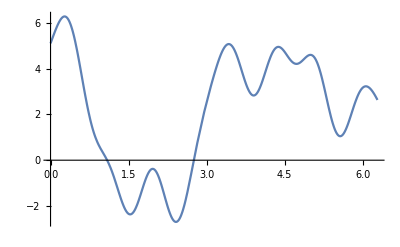

```mathematica
Plot[(2Cos[2x]^3+Sin[4x]^2+1.3Sin[4.3x]+2Sin[.3 x]+3.1Cos[1.4x]),{x,0,2π}]
```